# Redbot Servo Kinematics

This is a worksheet to analyze the output of the motors on the SparkFun RedBot.  The Redbot is an Arduino Controlled two wheel actuatted robot that is enabled with Hall probe magnetic encoders.  The intent is to devise an accurate measure of speed using the feedback from the encoders.  The RedBot has a magnetic disk connected directly to the shaft of the motors.  The motor drives the wheels with a 48:1 gear reduction to increase the available torque.  The disk is engineered with 4 pole shifts (4 North and 4 South Poles).  The Hall probes (one on each wheel) are arranged to pulse pins that are connected to interrupts on the Arduino board.  (Interrupts insure that no pulses are missed) They simply count the pulses in the current direction of travel.

In addition to recording the pulses, the time between each pulse and the overall running time is recorded.  Knowing details of the engineering of the wheel drive mechanism allows us to determine the distance and speed of the robot.

## Instantaneous vs Average Speed

Classic illustration of the speed of the motors.  We know the diameter of the wheel (6.5cm) and the number of pules per revolution (48*4) we can work out the distance per pulse.

```mathematica
wheelDiameter = Quantity[ 6.5, "cm"];
pulsesPerRev = 4*48;
```

#### Load data from a run and assign lists for easy manipulation in graphs.

Order of output: pulse_count, microseconds_betw_pulse, dist_trav, time, vi, va

```mathematica
(* This is using every pulse to calc, vi. *)
dataSet1={{1,18024,0.1,18020,5.9,5.9},{2,16152,0.2,34176,6.6,6.2},{3,18992,0.3,53172,5.6,6.0},{4,20944,0.4,74120,5.1,5.7},{5,15804,0.5,89928,6.7,5.9},{6,16092,0.6,106024,6.6,6.0},{7,12052,0.7,118080,8.8,6.3},{8,8900,0.9,126984,12.0,6.7},{9,8252,1.0,135240,12.9,7.1},{10,8632,1.1,143876,12.3,7.4},{11,7592,1.2,151472,14.0,7.7},{12,6512,1.3,157988,16.3,8.1},{13,6544,1.4,164536,16.3,8.4},{14,6980,1.5,171520,15.2,8.7},{15,6088,1.6,177612,17.5,9.0},{16,5208,1.7,182824,20.4,9.3},{17,5372,1.8,188200,19.8,9.6},{18,6080,1.9,194284,17.5,9.9},{19,5584,2.0,199872,19.0,10.1},{20,4848,2.1,204724,21.9,10.4},{21,4928,2.2,209656,21.6,10.7},{22,5360,2.3,215020,19.8,10.9},{23,4892,2.4,219916,21.7,11.1},{24,4328,2.6,224248,24.6,11.4},{25,4512,2.7,228764,23.6,11.6},{27,4640,2.9,238508,22.9,12.0},{28,4092,3.0,242604,26.0,12.3},{30,4744,3.2,251536,22.4,12.7},{31,4368,3.3,255908,24.3,12.9},{33,4064,3.5,263924,26.2,13.3},{34,4580,3.7,272644,23.2,13.5},{36,3688,3.8,276336,28.8,13.9},{38,4328,4.0,284476,24.6,14.2},{40,3604,4.3,292072,29.5,14.6},{41,3716,4.4,295792,28.6,14.7},{43,3928,4.6,303956,27.1,15.0},{45,3736,4.8,311252,28.5,15.4},{46,4172,4.9,315428,25.5,15.5},{48,3352,5.1,322604,31.7,15.8},{50,3928,5.3,330048,27.1,16.1},{52,3280,5.5,336992,32.4,16.4},{54,3892,5.7,344324,27.3,16.7},{56,3252,6.0,351168,32.7,17.0},{58,3888,6.2,358468,27.4,17.2},{60,3164,6.4,365212,33.6,17.5},{61,3292,6.5,368508,32.3,17.6},{64,3008,6.8,378564,35.4,18.0},{65,3144,7.0,385292,29.7,18.1},{68,2964,7.2,391544,35.9,18.5},{70,3552,7.4,398220,29.9,18.7},{72,2936,7.7,404484,36.2,18.9},{74,3444,7.9,411000,30.9,19.1},{76,2860,8.1,417032,37.2,19.4},{78,3416,8.3,423452,31.1,19.6},{80,2832,8.5,429476,37.6,19.8},{82,3424,8.7,435896,31.1,20.0},{84,2904,8.9,441996,36.6,20.2},{86,3412,9.3,451612,33.8,20.4},{89,2924,9.5,457332,36.4,20.7},{91,3092,9.7,463772,34.4,20.9},{93,2920,9.9,469472,36.4,21.1},{95,3080,10.1,475844,34.5,21.2},{98,3300,10.4,484820,32.2,21.5},{100,2700,10.6,490556,39.4,21.7},{102,3172,10.8,496556,33.5,21.8},{105,2780,11.2,504964,38.3,22.1},{107,2972,11.4,511120,35.8,22.3},{109,2856,11.6,516656,37.2,22.4},{112,2708,11.9,525652,39.3,22.7},{114,3164,12.1,531632,33.6,22.8},{117,2724,12.4,539888,39.0,23.0},{119,2832,12.7,545808,37.6,23.2},{122,3036,13.0,554064,35.0,23.4},{124,2576,13.2,559488,41.3,23.6},{127,2844,13.5,568084,37.4,23.8},{129,2668,13.7,573272,39.9,23.9},{132,2540,14.0,581704,41.9,24.1},{134,3036,14.3,587436,35.0,24.3},{137,2676,14.6,595512,39.7,24.5},{139,2800,14.8,601340,38.0,24.6},{142,2956,15.1,609396,36.0,24.8},{144,2436,15.4,617140,41.4,25.1},{147,2700,15.6,622756,39.4,25.1},{150,2928,16.0,630724,36.3,25.3},{152,2436,16.2,635892,43.7,25.4},{155,2692,16.5,644040,39.5,25.6},{158,2908,16.8,651928,36.6,25.8},{160,2416,17.0,657040,44.0,25.9},{163,2700,17.3,665220,39.4,26.1},{165,2528,17.5,670176,42.1,26.2},{168,2376,17.9,678072,44.8,26.4},{171,2628,18.2,686056,40.5,26.5},{174,2824,18.5,693704,37.7,26.7},{176,2356,18.7,698692,45.1,26.8},{179,2604,19.0,706608,40.8,26.9},{182,2824,19.4,714272,37.7,27.1},{184,2368,19.7,721768,44.9,27.2},{187,2668,19.9,727272,39.9,27.3},{190,2852,20.2,734980,37.3,27.5},{193,2496,20.5,742480,42.6,27.6},{195,2620,20.7,747928,40.6,27.7},{198,2796,21.1,755576,38.0,27.9},{201,2460,21.4,763000,43.2,28.0},{203,2608,21.6,768420,40.8,28.1},{206,2796,21.9,776008,38.0,28.2},{209,2472,22.2,783432,43.0,28.4},{212,2324,22.5,791144,45.8,28.5},{214,2796,22.8,796412,38.0,28.6},{217,2456,23.1,803820,43.3,28.7},{220,2312,23.4,811496,46.0,28.8},{222,2788,23.7,819328,40.9,28.9},{225,2464,23.9,824116,43.2,29.0},{228,2348,24.2,831928,45.3,29.1},{231,2592,24.6,839812,41.0,29.3},{233,2476,24.8,844636,43.0,29.3},{236,2376,25.1,852500,44.8,29.4},{239,2688,25.4,860556,39.6,29.5},{241,2560,25.6,865548,41.5,29.6},{244,2420,26.0,873600,43.9,29.7},{247,2712,26.3,881800,39.2,29.8},{249,2564,26.5,886816,41.5,29.9},{252,2452,26.8,894912,43.4,29.9},{254,2956,27.0,900456,36.0,30.0},{257,2568,27.3,908180,41.4,30.1},{260,2440,27.7,916236,43.6,30.2},{262,2908,27.9,921724,36.6,30.2},{265,2596,28.2,929512,41.0,30.3},{268,2436,28.5,937656,43.7,30.4},{270,2896,28.7,943112,36.7,30.4},{273,2544,29.0,950732,41.8,30.5},{275,2656,29.4,958684,44.2,30.6},{278,2908,29.6,964152,36.6,30.7},{281,2560,29.9,971920,41.5,30.7},{283,2696,30.1,977520,39.4,30.8}};
```

```mathematica
(* This counts every 4 pulses (one revolution) *)
dataSet2={{1,24248,0.1,24244,4.4,4.4},{2,24248,0.2,24244,4.4,8.8},{3,24248,0.3,24244,4.4,13.2},{4,24248,0.4,24244,4.4,17.5},{5,91956,0.5,116204,1.2,4.6},{6,91956,0.6,116204,1.2,5.5},{7,91956,0.7,116204,1.2,6.4},{8,91956,0.9,116204,1.2,7.3},{9,55296,1.0,171504,1.9,5.6},{10,55296,1.1,171504,1.9,6.2},{11,55296,1.2,171504,1.9,6.8},{12,55296,1.3,171504,1.9,7.4},{13,32000,1.4,203508,3.3,6.8},{14,32000,1.5,203508,3.3,7.3},{15,32000,1.6,203508,3.3,7.8},{16,32000,1.7,203508,3.3,8.4},{17,25552,1.8,229064,4.2,7.9},{18,25552,1.9,229064,4.2,8.4},{19,25552,2.0,229064,4.2,8.8},{20,25552,2.1,229064,4.2,9.3},{21,21876,2.2,250944,4.9,8.9},{22,21876,2.3,250944,4.9,9.3},{23,21876,2.4,250944,4.9,9.7},{24,21876,2.6,250944,4.9,10.2},{25,19672,2.7,270620,5.4,9.8},{26,19672,2.8,270620,5.4,10.2},{27,19672,2.9,270620,5.4,10.6},{29,18244,3.1,288868,5.8,10.7},{30,18244,3.2,288868,5.8,11.0},{32,18244,3.4,288868,5.8,11.8},{33,17332,3.5,306204,6.1,11.5},{35,17332,3.7,306204,6.1,12.2},{37,16220,3.9,322428,6.6,12.2},{38,16220,4.1,322428,6.6,12.5},{40,16220,4.3,322428,6.6,13.2},{42,15844,4.5,338276,6.7,13.2},{44,15844,4.7,338276,6.7,13.8},{45,15480,4.8,353760,6.9,13.5},{47,15480,5.0,353760,6.9,14.1},{49,14616,5.2,368380,7.3,14.1},{51,14616,5.4,368380,7.3,14.7},{53,14240,5.6,382624,7.5,14.7},{55,14240,5.8,382624,7.5,15.3},{56,14240,6.0,382624,7.5,15.6},{58,14092,6.2,396720,7.5,15.5},{60,14092,6.4,396720,7.5,16.1},{62,13584,6.6,410308,7.8,16.1},{64,13584,6.8,410308,7.8,16.6},{66,13272,7.0,423584,8.0,16.6},{68,13272,7.2,423584,8.0,17.1},{70,13256,7.4,436844,8.0,17.0},{72,13256,7.7,436844,8.0,17.5},{75,12896,8.0,449744,8.2,17.7},{77,12364,8.2,462112,8.6,17.7},{79,12364,8.4,462112,8.6,18.2},{81,12248,8.6,474364,8.7,18.2},{83,12248,8.8,474364,8.7,18.6},{85,12396,9.0,486764,8.6,18.6},{88,12396,9.4,486764,8.6,19.2},{90,12132,9.6,498900,8.8,19.2},{92,12132,9.8,498900,8.8,19.6},{94,12064,10.0,510968,8.8,19.6},{96,12064,10.2,510968,8.8,20.0},{99,12036,10.5,523008,8.8,20.1},{101,11748,10.7,534760,9.1,20.1},{103,11748,11.1,534760,9.1,20.5},{106,11520,11.3,546284,9.2,20.6},{108,11520,11.5,546284,9.2,21.0},{111,11548,11.8,557836,9.2,21.2},{113,11340,12.0,569180,9.4,21.1},{116,11340,12.3,569180,9.4,21.7},{118,11116,12.6,580300,9.6,21.6},{121,11128,12.9,591432,9.6,21.8},{123,11128,13.1,591432,9.6,22.1},{126,11052,13.4,602488,9.6,22.2},{128,11052,13.6,602488,9.6,22.6},{131,10804,13.9,613300,9.8,22.7},{133,10704,14.3,624008,9.9,22.8},{136,10704,14.5,624008,9.9,23.2},{139,10712,14.8,634724,9.9,23.3},{141,10568,15.0,645296,10.1,23.2},{144,10568,15.3,645296,10.1,23.7},{147,10568,15.6,655868,10.1,23.8},{149,10628,16.0,666500,10.0,23.8},{152,10628,16.2,666500,10.0,24.3},{155,10452,16.5,676956,10.2,24.4},{158,10364,16.8,687324,10.3,24.4},{160,10364,17.1,697684,10.3,24.8},{163,10356,17.3,697684,10.3,24.8},{166,10312,17.7,708000,10.3,24.9},{169,10296,18.0,718300,10.3,25.0},{172,10296,18.3,718300,10.3,25.5},{174,10320,18.5,728624,10.3,25.4},{177,10304,18.8,738932,10.3,25.5},{180,10304,19.1,738932,10.3,25.9},{183,10224,19.5,749160,10.4,26.0},{185,10168,19.8,759332,10.5,25.9},{188,10168,20.0,759332,10.5,26.3},{191,10232,20.3,769568,10.4,26.4},{194,10236,20.6,779808,10.4,26.5},{197,10224,21.0,790036,10.4,26.5},{200,10224,21.3,790036,10.4,26.9},{202,10172,21.5,800212,10.5,26.8},{205,10092,21.8,810308,10.5,26.9},{208,10092,22.1,810308,10.5,27.3},{211,10048,22.4,820360,10.6,27.4},{214,9992,22.8,830356,10.6,27.4},{216,9992,23.1,840328,10.7,27.7},{219,9968,23.3,840328,10.7,27.7},{222,10024,23.6,850356,10.6,27.8},{225,10052,23.9,860412,10.6,27.8},{228,10052,24.2,860412,10.6,28.2},{231,10048,24.6,870464,10.6,28.2},{233,10004,24.8,880472,10.6,28.1},{236,10004,25.1,880472,10.6,28.5},{239,10056,25.4,890532,10.6,28.5},{242,10100,25.7,900636,10.5,28.6},{245,10108,26.1,910748,10.5,28.6},{248,10108,26.4,910748,10.5,29.0},{250,10128,26.6,920880,10.5,28.9},{253,10276,26.9,931160,10.3,28.9},{256,10276,27.2,931160,10.3,29.2},{259,10256,27.5,941420,10.4,29.3},{261,10272,27.8,951696,10.4,29.2},{264,10272,28.1,951696,10.4,29.5},{267,10388,28.4,962088,10.2,29.5},{270,10228,28.7,972320,10.4,29.5},{273,10252,29.0,982576,10.4,29.6},{275,10252,29.2,982576,10.4,29.8},{278,10384,29.6,992968,10.2,29.8},{281,10348,29.9,1003320,10.3,29.8},{284,10348,30.2,1003320,10.3,30.1}};
```

```mathematica
(* This is using every pulse to calc, vi. Here we keep the total time dt is the rotational time. *)
dataSet3={{1,16604,0.1,16600,6.4,6.4},{2,16604,0.2,31300,6.4,6.8},{3,16604,0.3,49008,6.4,6.5},{4,16604,0.4,76628,6.4,5.6},{5,80320,0.5,156952,1.3,3.4},{6,80320,0.6,173312,1.3,3.7},{7,80320,0.7,186724,1.3,4.0},{8,80320,0.9,196880,1.3,4.3},{9,7928,1.0,204812,13.4,4.7},{10,7928,1.1,212260,13.4,5.0},{11,7928,1.2,220252,13.4,5.3},{12,7928,1.3,227388,13.4,5.6},{13,6200,1.4,233592,17.2,5.9},{14,6200,1.5,239848,17.2,6.2},{15,6200,1.6,246536,17.2,6.5},{16,6200,1.7,252392,17.2,6.7},{17,5112,1.8,257508,20.8,7.0},{18,5112,1.9,262756,20.8,7.3},{19,5112,2.0,268644,20.8,7.5},{20,5112,2.1,274064,20.8,7.8},{21,4720,2.2,278788,22.5,8.0},{22,4720,2.3,283576,22.5,8.3},{23,4720,2.4,288800,22.5,8.5},{24,4720,2.6,293520,22.5,8.7},{25,4208,2.7,297732,25.3,8.9},{26,4208,2.9,307088,25.3,9.2},{28,4208,3.0,311660,25.3,9.6},{29,4084,3.2,319956,26.0,9.8},{31,4084,3.3,324708,26.0,10.2},{33,3936,3.5,333012,27.0,10.5},{34,3936,3.6,337072,27.0,10.7},{36,3936,3.8,345732,27.0,11.1},{37,3680,3.9,349416,28.9,11.3},{39,3680,4.1,357560,28.9,11.6},{41,3636,4.4,365216,29.3,11.9},{42,3636,4.5,368980,29.3,12.1},{44,3636,4.7,377200,29.3,12.4},{46,3568,4.9,384500,29.8,12.7},{48,3568,5.1,392556,29.8,13.0},{49,3408,5.2,395968,31.2,13.2},{51,3408,5.4,403508,31.2,13.4},{53,3332,5.6,410564,31.9,13.7},{55,3332,5.8,418020,31.9,14.0},{57,3260,6.1,424920,32.6,14.3},{59,3260,6.3,432232,32.6,14.5},{61,3224,6.5,439052,33.0,14.8},{62,3224,6.6,442396,33.0,14.9},{64,3224,6.8,449616,33.0,15.1},{66,3080,7.0,455936,34.5,15.4},{68,3080,7.2,462988,34.5,15.6},{70,3032,7.4,469188,35.1,15.9},{72,3032,7.7,476212,35.1,16.1},{74,3052,7.9,482444,34.8,16.3},{76,3052,8.1,489336,34.8,16.5},{78,2968,8.3,495420,35.8,16.7},{81,2956,8.6,505216,36.0,17.1},{83,2956,8.8,511776,36.0,17.2},{85,2908,9.0,517932,36.6,17.5},{87,2908,9.3,524448,36.6,17.6},{89,2876,9.5,530512,37.0,17.8},{91,2876,9.7,536916,37.0,18.0},{93,2836,9.9,542952,37.5,18.2},{95,2836,10.1,549304,37.5,18.4},{98,2840,10.4,558264,37.4,18.7},{100,2840,10.6,564792,37.4,18.8},{102,2800,10.8,570524,38.0,19.0},{104,2800,11.1,576936,38.0,19.2},{107,2792,11.4,586008,38.1,19.4},{109,2796,11.6,591868,38.0,19.6},{111,2796,11.8,598188,38.0,19.7},{114,2788,12.1,607016,38.1,20.0},{116,2788,12.3,613292,38.1,20.1},{118,2696,12.6,618820,39.4,20.3},{121,2660,12.9,627684,40.0,20.5},{123,2660,13.1,633700,40.0,20.6},{125,2704,13.4,642200,39.3,20.8},{128,2704,13.6,648348,39.3,21.0},{130,2636,13.8,653756,40.3,21.1},{133,2628,14.1,662480,40.5,21.4},{135,2628,14.4,668388,40.5,21.5},{138,2632,14.7,676712,40.4,21.7},{140,2632,14.9,682720,40.4,21.8},{142,2572,15.1,687980,41.4,22.0},{145,2536,15.4,696408,41.9,22.1},{147,2536,15.7,704884,41.9,22.3},{150,2544,16.0,710104,41.8,22.5},{153,2512,16.3,718504,42.3,22.6},{155,2512,16.5,724152,42.3,22.8},{158,2532,16.8,732144,42.0,23.0},{160,2532,17.0,737976,42.0,23.1},{163,2540,17.3,746236,41.9,23.2},{165,2508,17.5,751576,42.4,23.3},{168,2508,17.9,759912,42.4,23.5},{170,2448,18.1,764944,43.4,23.6},{173,2452,18.4,773016,43.4,23.8},{176,2452,18.7,781344,43.4,24.0},{178,2504,18.9,786464,42.5,24.1},{181,2452,19.3,794632,43.4,24.2},{183,2452,19.5,800224,43.4,24.3},{186,2500,19.8,808128,42.5,24.5},{188,2500,20.1,816412,42.5,24.6},{191,2500,20.3,821992,42.5,24.7},{194,2488,20.6,829784,42.7,24.9},{196,2488,20.8,835480,42.7,25.0},{199,2464,21.2,843504,43.2,25.1},{201,2488,21.4,848744,42.7,25.2},{204,2488,21.7,857052,42.7,25.3},{207,2440,22.0,864992,43.6,25.5},{209,2424,22.2,870140,43.9,25.5},{212,2424,22.5,878328,43.9,25.7},{214,2444,22.8,883368,43.5,25.8},{217,2488,23.1,891588,42.7,25.9},{220,2488,23.4,899860,42.7,26.0},{222,2436,23.6,904884,43.7,26.1},{225,2440,23.9,912976,43.6,26.2},{227,2440,24.1,918496,43.6,26.3},{230,2504,24.5,926360,42.5,26.4},{233,2460,24.8,934540,43.2,26.5},{235,2460,25.0,940132,43.2,26.6},{238,2488,25.3,948020,42.7,26.7},{240,2488,25.5,953772,42.7,26.8},{243,2520,25.8,961916,42.2,26.9},{245,2488,26.2,969788,42.7,26.9},{248,2488,26.4,975564,42.7,27.0},{250,2496,26.7,983700,42.6,27.1},{253,2516,26.9,988996,42.3,27.2},{256,2516,27.2,997432,42.3,27.3},{258,2504,27.4,1002572,42.5,27.4},{261,2520,27.8,1010924,42.2,27.5},{263,2520,28.0,1016572,42.2,27.5},{266,2504,28.3,1024496,42.5,27.6},{269,2536,28.6,1032912,41.9,27.7},{271,2536,28.8,1038536,41.9,27.8},{274,2488,29.1,1046448,42.7,27.8},{276,2488,29.4,1052296,42.7,27.9},{279,2528,29.7,1060492,42.1,28.0},{282,2536,30.0,1068492,41.9,28.1}};
```

```mathematica
(* This is using every pulse to calc, vi. Here we keep the total time dt is the rotational time. Measured overall speed: 33 cm/s *)
dataSet4={{1,20432,0.1,20428,5.2,5.2},{2,20432,0.2,38032,5.2,5.6},{3,20432,0.3,58928,5.2,5.4},{4,20432,0.4,82176,5.2,5.2},{5,17268,0.5,99448,6.2,5.3},{6,17268,0.6,110820,6.2,5.8},{7,17268,0.7,120596,6.2,6.2},{8,17268,0.9,130560,6.2,6.5},{9,8624,1.0,139188,12.3,6.9},{10,8624,1.1,146472,12.3,7.3},{11,8624,1.2,153568,12.3,7.6},{12,8624,1.3,160960,12.3,7.9},{13,6336,1.4,167300,16.8,8.3},{14,6336,1.5,172820,16.8,8.6},{15,6336,1.6,178600,16.8,8.9},{16,6336,1.7,185068,16.8,9.2},{17,5856,1.8,190928,18.2,9.5},{18,5856,1.9,196004,18.2,9.8},{19,5856,2.0,201064,18.2,10.1},{20,5856,2.1,206588,18.2,10.3},{21,4972,2.2,211564,21.4,10.6},{22,4972,2.3,215976,21.4,10.8},{23,4972,2.4,220656,21.4,11.1},{24,4972,2.6,225956,21.4,11.3},{26,4812,2.8,235032,22.1,11.8},{27,4812,2.9,239468,22.1,12.0},{28,4812,3.0,244472,22.1,12.2},{30,4604,3.2,253184,23.1,12.6},{31,4604,3.3,257392,23.1,12.8},{33,4180,3.5,266240,25.4,13.2},{35,4180,3.7,273832,25.4,13.6},{36,4180,3.8,278256,25.4,13.8},{38,4112,4.0,286080,25.9,14.1},{40,4112,4.3,294272,25.9,14.5},{41,4028,4.4,298304,26.4,14.6},{43,4028,4.6,305704,26.4,15.0},{45,3848,4.8,313760,27.6,15.3},{47,3848,5.0,320636,27.6,15.6},{48,3848,5.1,324544,27.6,15.7},{50,3632,5.3,331420,29.3,16.0},{52,3632,5.5,338696,29.3,16.3},{54,3600,5.7,345584,29.5,16.6},{56,3600,6.0,352960,29.5,16.9},{58,3612,6.2,359772,29.4,17.1},{60,3612,6.4,366792,29.4,17.4},{62,3420,6.6,373260,31.1,17.7},{64,3420,6.8,380092,31.1,17.9},{66,3344,7.0,386476,31.8,18.2},{68,3344,7.2,393284,31.8,18.4},{70,3388,7.4,399692,31.4,18.6},{72,3388,7.7,406396,31.4,18.8},{74,3260,7.9,412580,32.6,19.1},{76,3260,8.1,419096,32.6,19.3},{78,3212,8.3,425168,33.1,19.5},{80,3212,8.5,431652,33.1,19.7},{82,3208,8.8,440800,33.2,19.9},{84,3208,9.0,447380,33.7,20.1},{87,3152,9.3,453128,33.7,20.4},{89,3092,9.5,459556,34.4,20.6},{91,3092,9.7,465248,34.4,20.8},{93,3068,9.9,471620,34.7,21.0},{95,3068,10.2,480580,34.7,21.2},{98,3040,10.4,486340,35.0,21.4},{100,3040,10.6,492384,35.0,21.6},{103,2996,11.0,500928,35.5,21.9},{105,2984,11.2,507152,35.6,22.0},{107,2984,11.4,512644,35.6,22.2},{110,2980,11.7,521500,35.7,22.4},{112,2980,11.9,527424,35.7,22.6},{115,2916,12.2,535728,36.5,22.8},{117,2884,12.4,541756,36.9,23.0},{119,2884,12.7,547100,36.9,23.1},{122,2908,13.0,555720,36.6,23.3},{124,2908,13.2,561548,36.6,23.5},{127,2856,13.5,569684,37.2,23.7},{129,2888,13.7,575688,36.8,23.8},{132,2888,14.0,584156,36.8,24.0},{134,2904,14.3,589668,36.6,24.2},{137,2872,14.6,598424,37.0,24.3},{139,2872,14.8,603720,37.0,24.5},{142,2860,15.1,612228,37.2,24.7},{144,2860,15.3,617956,37.2,24.8},{147,2836,15.6,626024,37.5,25.0},{149,2832,15.8,631932,37.6,25.1},{152,2832,16.2,640152,37.6,25.3},{154,2800,16.4,645496,38.0,25.4},{157,2812,16.7,653992,37.8,25.5},{159,2812,16.9,659164,37.8,25.7},{162,2796,17.2,667552,38.0,25.8},{164,2796,17.4,673196,38.0,25.9},{167,2760,17.8,681068,38.5,26.1},{169,2764,18.1,689256,38.5,26.2},{172,2764,18.3,694816,38.5,26.3},{175,2760,18.6,702656,38.5,26.5},{177,2724,18.8,708328,39.0,26.6},{180,2724,19.1,716336,39.0,26.7},{182,2760,19.5,724172,38.5,26.8},{185,2772,19.7,729916,38.4,27.0},{187,2772,20.0,738044,38.4,27.1},{190,2756,20.2,743264,38.6,27.2},{193,2732,20.5,751548,38.9,27.3},{195,2732,20.7,756580,38.9,27.4},{198,2708,21.1,764616,39.3,27.5},{201,2692,21.4,772792,39.5,27.7},{203,2692,21.6,777728,39.5,27.8},{206,2660,21.9,785672,40.0,27.9},{208,2660,22.2,793812,39.3,28.0},{211,2704,22.4,798800,39.3,28.1},{214,2716,22.8,806856,39.2,28.2},{216,2716,23.0,812256,39.2,28.3},{219,2644,23.3,819776,40.2,28.4},{222,2600,23.6,827548,40.9,28.5},{225,2632,23.9,835472,40.4,28.6},{227,2632,24.1,840348,40.4,28.7},{230,2628,24.5,848140,40.5,28.8},{233,2648,24.8,856140,40.2,28.9},{235,2648,25.0,861016,40.2,29.0},{238,2660,25.3,868956,40.0,29.1},{241,2652,25.6,877020,40.1,29.2},{243,2652,25.8,881864,40.1,29.3},{246,2620,26.2,889612,40.6,29.4},{249,2612,26.5,897476,40.7,29.5},{252,2612,26.8,905156,40.7,29.6},{254,2620,27.0,910116,40.6,29.7},{257,2580,27.3,917948,41.2,29.8},{260,2580,27.7,925476,41.2,29.9},{263,2592,28.0,932852,41.0,30.0},{265,2636,28.2,938316,40.3,30.0},{268,2636,28.5,945896,40.3,30.1},{271,2576,28.8,953208,41.3,30.2},{274,2552,29.1,960832,41.7,30.3},{276,2552,29.4,966048,41.7,30.4},{279,2596,29.7,973440,41.0,30.5},{282,2572,30.0,981072,41.4,30.6}};
```

```mathematica
dataSet5 = {{1,3426288,0.1,10224,0.0,10.4},{2,3426288,0.2,28428,0.0,7.5},{3,3426288,0.3,40796,0.0,7.8},{4,3426288,0.4,50236,0.0,8.5},{5,46500,0.5,57640,2.3,9.2},{6,46500,0.6,64636,2.3,9.9},{7,46500,0.7,71932,2.3,10.3},{8,46500,0.9,78204,2.3,10.9},{9,25308,1.0,83496,4.2,11.5},{10,25308,1.1,88760,4.2,12.0},{11,25308,1.2,94568,4.2,12.4},{12,25308,1.3,99708,4.2,12.8},{13,20332,1.4,104168,5.2,13.3},{14,20332,1.5,108732,5.2,13.7},{15,20332,1.6,113712,5.2,14.0},{16,20332,1.7,118224,5.2,14.4},{17,156,1.8,122220,681.8,14.8},{19,156,2.0,130968,681.8,15.4},{21,520,2.2,138816,204.5,16.1},{22,520,2.3,142624,204.5,16.4},{24,520,2.6,150728,204.5,16.9},{26,1088,2.8,157812,97.8,17.5},{28,1088,3.0,165528,97.8,18.0},{30,1748,3.2,172176,60.8,18.5},{31,1748,3.3,176040,60.8,18.7},{33,2396,3.5,182776,44.4,19.2},{35,2396,3.7,189744,44.4,19.6},{37,3088,3.9,196176,34.4,20.1},{39,3088,4.1,202988,34.4,20.4},{41,3988,4.4,209292,26.7,20.8},{43,3988,4.6,215872,26.7,21.2},{46,4844,4.9,225072,22.0,21.7},{48,4844,5.1,231604,22.0,22.0},{50,5744,5.3,237320,18.5,22.4},{52,5744,5.5,243724,18.5,22.7},{54,6680,5.7,249340,15.9,23.0},{57,7552,6.1,258256,14.1,23.5},{59,7552,6.3,264280,14.1,23.7},{61,8468,6.5,269884,12.6,24.0},{63,8468,6.7,275736,12.6,24.3},{66,9332,7.0,283900,11.4,24.7},{68,9332,7.2,289776,11.4,25.0},{71,144,7.6,297964,738.6,25.3},{73,1124,7.8,303240,94.6,25.6},{76,1124,8.1,311484,94.6,26.0},{78,2044,8.3,316464,52.0,26.2},{81,2940,8.6,324424,36.2,26.6},{83,2940,8.8,329788,36.2,26.8},{86,3832,9.1,337296,27.8,27.1},{88,3832,9.4,342716,27.8,27.3},{91,4664,9.7,350276,22.8,27.6},{94,5436,10.0,357576,19.6,28.0},{96,5436,10.2,362876,19.6,28.1},{99,6248,10.5,370324,17.0,28.4},{102,7108,10.8,377492,15.0,28.7},{105,7904,11.2,384908,13.5,29.0},{107,7904,11.5,392364,13.5,29.2},{110,8580,11.7,396900,12.4,29.5},{113,404,12.0,404188,263.3,29.7},{116,404,12.3,411544,263.3,30.0},{119,1060,12.7,418656,100.3,30.2},{122,1776,13.0,425536,59.9,30.5},{125,2408,13.3,432708,44.2,30.7},{128,2408,13.6,439932,44.2,30.9},{131,2968,13.9,446916,35.8,31.2},{134,3600,14.3,453724,29.5,31.4},{137,4252,14.6,460816,25.0,31.6},{140,4252,14.9,467992,25.0,31.8},{143,4884,15.2,474948,21.8,32.0},{146,5604,15.5,481728,19.0,32.2},{149,6404,15.8,488808,16.6,32.4},{152,6404,16.2,495996,16.6,32.6},{155,7204,16.5,502888,14.8,32.8},{158,7936,16.8,509608,13.4,33.0},{161,260,17.1,516604,409.1,33.1},{164,260,17.4,523664,409.1,33.3},{167,984,17.8,530460,108.1,33.5},{170,1692,18.1,537064,62.9,33.7},{173,2408,18.4,543960,44.2,33.8},{176,2408,18.7,550936,44.2,34.0},{179,3084,19.0,557660,34.5,34.1},{183,3764,19.5,566656,28.3,34.3},{186,4464,19.8,573168,23.8,34.5},{189,5160,20.1,579964,20.6,34.7},{192,5160,20.4,586844,20.6,34.8},{195,5844,20.7,593488,18.2,34.9},{198,6560,21.1,599948,16.2,35.1},{201,7296,21.4,606708,14.6,35.2},{204,7296,21.8,615600,13.3,35.4},{208,8016,22.1,622408,13.3,35.5},{211,560,22.4,629008,189.9,35.7},{214,1248,22.8,635448,85.2,35.8},{217,2072,23.1,642204,51.3,35.9},{220,2072,23.4,648992,51.3,36.1},{223,2828,23.7,655552,37.6,36.2},{226,3588,24.1,664396,29.6,36.3},{230,4452,24.5,670836,23.9,36.5},{233,5264,24.8,677508,20.2,36.6},{236,5264,25.1,684280,20.2,36.7},{239,6100,25.4,690848,17.4,36.8},{242,7008,25.7,697256,15.2,36.9},{246,64,26.2,706036,1661.8,37.1},{249,992,26.5,712736,107.2,37.2},{252,992,26.8,719532,107.2,37.2},{255,1948,27.1,726080,54.6,37.4},{258,2936,27.4,732416,36.2,37.5},{261,3828,27.9,741128,27.8,37.6},{265,4712,28.2,747712,22.6,37.7},{268,4712,28.5,754408,22.6,37.8},{271,5628,28.8,760864,18.9,37.9},{274,6472,29.1,767116,16.4,38.0},{278,7324,29.6,775680,14.5,38.1},{281,396,29.9,782160,268.6,38.2},{284,396,30.2,788724,268.6,38.3}};
```

```mathematica
dataSet6 = {{1,11244,0.1,20576,9.5,5.2},{2,11244,0.2,34584,9.5,6.2},{3,11244,0.3,44404,9.5,7.2},{4,11244,0.4,52024,9.5,8.2},{5,3608,0.5,59188,29.5,9.0},{6,3608,0.6,66608,29.5,9.6},{7,3608,0.7,73008,29.5,10.2},{8,3608,0.9,78496,29.5,10.8},{9,2428,1.0,84008,43.8,11.4},{10,2428,1.1,89964,43.8,11.8},{11,2428,1.2,95284,43.8,12.3},{12,2428,1.3,99860,43.8,12.8},{13,2216,1.4,104564,48.0,13.2},{14,2216,1.5,109776,48.0,13.6},{15,2216,1.6,114452,48.0,13.9},{16,2216,1.7,118568,48.0,14.4},{17,2432,1.8,122752,43.7,14.7},{19,2432,2.0,131568,43.7,15.4},{21,2456,2.2,139184,43.3,16.0},{22,2456,2.3,143484,43.3,16.3},{24,2456,2.6,150872,43.3,16.9},{26,2460,2.8,158504,43.2,17.4},{28,2460,3.0,165536,43.2,18.0},{30,2632,3.2,172900,40.4,18.5},{32,2632,3.4,179612,40.4,18.9},{34,2824,3.6,186576,37.7,19.4},{36,2824,3.8,193020,37.7,19.8},{38,3016,4.0,199788,35.3,20.2},{40,3016,4.3,206044,35.3,20.6},{42,3312,4.5,212680,32.1,21.0},{44,3312,4.7,218792,32.1,21.4},{46,3748,4.9,225168,28.4,21.7},{48,3748,5.1,231056,28.4,22.1},{50,4072,5.3,237268,26.1,22.4},{53,4540,5.6,245888,23.4,22.9},{55,4540,5.8,252136,23.4,23.2},{57,5120,6.1,257620,20.8,23.5},{59,5120,6.4,266276,20.8,23.8},{62,5624,6.6,272088,18.9,24.2},{64,5624,6.8,277496,18.9,24.5},{66,6108,7.1,286084,17.4,25.2},{69,6804,7.3,291296,15.6,25.2},{71,6804,7.6,297096,15.6,25.4},{74,7516,7.9,305156,14.2,25.8},{76,7516,8.1,310368,14.2,26.0},{79,8180,8.4,318644,13.0,26.4},{81,8984,8.6,323696,11.8,26.6},{84,8984,8.9,331712,11.8,26.9},{86,196,9.1,337144,542.6,27.1},{89,1268,9.5,344808,83.9,27.5},{91,1268,9.7,350320,83.9,27.6},{94,2356,10.0,358108,45.1,27.9},{97,3428,10.3,365612,31.0,28.2},{99,3428,10.5,371012,31.0,28.4},{102,4448,10.8,378624,23.9,28.7},{105,5436,11.2,385968,19.6,28.9},{107,5436,11.4,391280,19.6,29.1},{110,6404,11.7,398708,16.6,29.3},{113,7260,12.0,405880,14.6,29.6},{116,7260,12.3,413320,14.6,29.8},{119,8144,12.7,420860,13.1,30.1},{122,120,13.0,428112,886.3,30.3},{125,1008,13.3,435128,105.5,30.6},{127,1008,13.6,442376,105.5,30.7},{130,1776,13.8,447296,59.9,30.9},{133,2468,14.1,454204,43.1,31.1},{136,2468,14.5,461384,43.1,31.4},{139,3228,14.8,468632,32.9,31.5},{142,3948,15.1,475620,26.9,31.8},{145,4628,15.4,482388,23.0,32.0},{148,4628,15.7,489432,23.0,32.2},{151,5304,16.1,496544,20.1,32.3},{154,5968,16.4,503400,17.8,32.5},{157,6584,16.7,510056,16.2,32.7},{160,7268,17.1,519216,14.6,32.9},{164,7268,17.4,526108,14.6,33.2},{166,7888,17.8,533092,13.5,33.5},{170,112,18.1,539840,949.6,33.5},{173,772,18.4,546416,137.8,33.7},{176,772,18.7,553236,137.8,33.8},{179,1404,19.0,560212,75.8,34.0},{182,2068,19.4,566908,51.4,34.1},{185,2740,19.7,573448,38.8,34.3},{188,2740,20.0,580264,38.8,34.5},{191,3424,20.3,587180,31.1,34.6},{194,4152,20.6,593892,25.6,34.7},{197,4904,21.1,602876,21.7,34.9},{201,5664,21.4,609376,18.8,35.1},{204,5664,21.7,616144,18.8,35.2},{207,6384,22.0,623052,16.7,35.3},{210,7084,22.3,629684,15.0,35.5},{213,7752,22.7,636144,13.7,35.6},{216,7752,23.0,642852,13.7,35.7},{219,116,23.3,649700,916.9,35.9},{222,788,23.7,658560,135.0,36.0},{226,1456,24.0,665152,73.0,36.1},{229,2060,24.4,671564,51.6,36.3},{232,2060,24.7,678236,51.6,36.4},{235,2704,25.0,685024,39.3,36.5},{238,3408,25.3,691592,31.2,36.6},{241,4136,25.7,700400,25.7,36.7},{245,4872,26.1,706788,21.8,36.9},{248,4872,26.4,713468,21.8,37.0},{251,5672,26.7,720276,18.8,37.1},{254,6492,27.0,726828,16.4,37.2},{257,7272,27.3,733184,14.6,37.3},{261,112,27.8,741924,949.6,37.4},{264,112,28.1,748560,949.6,37.5},{267,936,28.4,755288,113.6,37.6},{270,1724,28.7,761764,61.7,37.7},{273,2532,29.0,768076,42.0,37.8},{277,3388,29.5,776808,31.4,37.9},{280,3388,29.8,783396,31.4,38.0},{283,4216,30.1,790108,25.2,38.1}};
```

```mathematica
dataSet7 = {{1,3658044,0.1,23460,0.0,4.5},{2,3658044,0.2,34972,0.0,6.1},{3,3658044,0.3,44416,0.0,7.2},{4,3658044,0.4,53452,0.0,8.0},{5,37456,0.5,60920,2.8,8.7},{6,37456,0.6,67100,2.8,9.5},{7,37456,0.7,73180,2.8,10.2},{8,37456,0.9,79596,2.8,10.7},{9,24316,1.0,85240,4.4,11.2},{10,24316,1.1,90104,4.4,11.8},{11,24316,1.2,94960,4.4,12.3},{12,24316,1.3,100308,4.4,12.7},{13,19864,1.4,105108,5.4,13.2},{14,19864,1.5,109312,5.4,13.6},{15,19864,1.6,113600,5.4,14.0},{16,19864,1.7,118352,5.4,14.4},{18,17552,1.9,126420,6.1,15.1},{19,17552,2.0,130304,6.1,15.5},{21,15984,2.2,138652,6.7,16.1},{23,15984,2.4,145804,6.7,16.8},{25,14948,2.7,153604,7.1,17.3},{27,14948,2.9,160344,7.1,17.9},{28,14948,3.0,164216,7.1,18.1},{30,14168,3.2,170916,7.5,18.7},{32,14168,3.4,177848,7.5,19.1},{34,13472,3.6,184272,7.9,19.6},{36,13472,3.8,191016,7.9,20.0},{39,13040,4.1,200252,8.2,20.7},{41,12572,4.4,206872,8.5,21.1},{43,12572,4.6,212688,8.5,21.5},{45,12284,4.8,219156,8.7,21.8},{47,12284,5.0,224828,8.7,22.2},{49,12032,5.2,231196,8.8,22.5},{52,12032,5.5,239968,8.8,23.0},{54,11744,5.7,245576,9.1,23.4},{56,11744,6.0,251524,9.1,23.7},{59,11500,6.3,259788,9.2,24.2},{61,11328,6.5,265780,9.4,24.4},{63,11328,6.7,271020,9.4,24.7},{66,11112,7.0,279408,9.6,25.1},{68,11112,7.2,285084,9.6,25.4},{71,10980,7.6,292988,9.7,25.8},{73,10808,7.8,298692,9.8,26.0},{75,10808,8.0,303720,9.8,26.3},{78,10628,8.3,311712,10.0,26.6},{81,10460,8.6,319788,10.2,26.9},{83,10460,8.8,324672,10.2,27.2},{86,10348,9.1,332488,10.3,27.5},{88,10200,9.5,340344,10.4,27.7},{91,10200,9.7,345088,10.4,28.0},{94,10104,10.0,352756,10.5,28.3},{97,10044,10.3,360500,10.6,28.6},{99,10044,10.6,365184,10.6,28.8},{102,9956,10.8,372736,10.7,29.1},{105,9892,11.2,380356,10.8,29.4},{108,9892,11.5,387688,10.8,29.6},{111,9888,11.8,394784,10.8,29.9},{114,9716,12.1,402196,10.9,30.1},{116,9748,12.4,409720,10.9,30.3},{119,9748,12.7,414292,10.9,30.5},{122,9724,13.0,421656,10.9,30.8},{125,9636,13.3,429088,11.0,31.0},{128,9636,13.6,436224,11.0,31.2},{131,9580,13.9,443152,11.1,31.4},{134,9520,14.3,450368,11.2,31.6},{137,9444,14.6,457644,11.3,31.8},{140,9444,14.9,464600,11.3,32.0},{143,9348,15.2,471364,11.4,32.3},{146,9328,15.5,478464,11.4,32.5},{149,9308,15.8,485640,11.4,32.6},{152,9308,16.2,492484,11.4,32.8},{155,9188,16.5,499176,11.6,33.0},{158,9172,16.8,506116,11.6,33.2},{161,9168,17.1,513180,11.6,33.4},{164,9168,17.4,519932,11.6,33.5},{167,9064,17.8,526488,11.7,33.7},{170,9024,18.1,533340,11.8,33.9},{173,9048,18.4,540328,11.8,34.1},{176,9048,18.7,547028,11.8,34.2},{180,8996,19.1,555956,11.8,34.4},{183,8904,19.5,562388,11.9,34.6},{186,8856,19.8,569112,12.0,34.8},{189,8836,20.1,575936,12.0,34.9},{192,8836,20.4,582496,12.0,35.1},{195,8808,20.7,588872,12.1,35.2},{199,8776,21.2,597656,12.1,35.4},{202,8764,21.5,604288,12.1,35.6},{205,8704,21.8,611008,12.2,35.7},{208,8704,22.1,617480,12.2,35.8},{211,8692,22.4,623792,12.2,36.0},{215,8680,22.9,632444,12.3,36.2},{218,8620,23.2,638988,12.3,36.3},{221,8640,23.5,645656,12.3,36.4},{224,8640,23.8,652084,12.3,36.5},{227,8632,24.1,658336,12.3,36.7},{231,8592,24.6,666920,12.4,36.8},{234,8568,24.9,673420,12.4,37.0},{237,8552,25.2,680016,12.4,37.1},{240,8540,25.5,686376,12.4,37.2},{244,8540,26.0,694916,12.5,37.3},{247,8544,26.3,701120,12.4,37.5},{250,8532,26.6,707596,12.5,37.6},{254,8540,27.0,716136,12.5,37.7},{257,8528,27.3,722720,12.5,37.8},{260,8528,27.7,729060,12.5,37.9},{263,8516,28.0,735248,12.5,38.0},{267,8536,28.4,743788,12.5,38.2},{270,8528,28.7,750260,12.5,38.3},{273,8528,29.0,756840,12.5,38.4},{276,8528,29.4,763200,12.5,38.5},{280,8544,29.8,771728,12.4,38.6},{283,8516,30.1,777904,12.5,38.7}};
```

```mathematica
dataSet8 ={{1,5124260,0.1,10072,0.1,10.6},{2,5124260,0.2,29100,0.1,7.3},{3,5124260,0.3,41744,0.1,7.6},{4,5124260,0.4,51152,0.1,8.3},{5,48452,0.5,58532,6.6,9.1},{6,48452,0.6,65488,6.6,9.7},{7,48452,0.7,72716,6.6,10.2},{8,48452,0.9,79008,6.6,10.8},{9,25880,1.0,84416,12.3,11.3},{10,25880,1.1,89796,12.3,11.8},{11,25880,1.2,95628,12.3,12.2},{12,25880,1.3,100828,12.3,12.7},{13,20900,1.4,105320,15.3,13.1},{14,20900,1.5,109880,15.3,13.6},{15,20900,1.6,114872,15.3,13.9},{16,20900,1.7,119468,15.3,14.2},{18,18160,1.9,127612,17.6,15.0},{19,18160,2.0,132168,17.6,15.3},{21,16484,2.2,139972,19.4,16.0},{23,16484,2.4,148060,19.4,16.5},{24,15448,2.7,155424,20.7,17.5},{26,15448,2.8,158996,20.7,17.4},{28,15448,3.0,166620,20.7,17.9},{30,14468,3.2,173280,22.1,18.4},{32,14468,3.4,180640,22.1,18.8},{34,13884,3.6,187024,23.0,19.3},{36,13884,3.8,194052,23.0,19.7},{38,13276,4.0,200208,24.0,20.2},{40,12800,4.4,209868,24.9,20.6},{43,12800,4.6,216268,24.9,21.1},{45,12380,4.8,222252,25.8,21.5},{47,12380,5.0,228536,25.8,21.9},{49,12124,5.2,234380,26.3,22.2},{52,12124,5.5,243556,26.3,22.7},{54,11860,5.7,249036,26.9,23.1},{56,11860,6.0,255116,26.9,23.3},{59,11504,6.3,263616,27.7,23.8},{61,11348,6.5,269104,28.1,24.1},{64,11348,6.8,277664,28.1,24.5},{66,11092,7.0,282848,28.8,24.8},{69,10900,7.3,291100,29.3,25.2},{71,10900,7.6,296636,29.3,25.5},{74,10712,7.9,304372,29.8,25.9},{76,10712,8.1,309976,29.8,26.1},{79,10572,8.4,317780,30.2,26.4},{82,10384,8.7,325264,30.7,26.8},{84,10384,8.9,330676,30.7,27.0},{87,10236,9.3,338232,31.2,27.4},{90,10088,9.6,345520,31.6,27.7},{92,10088,9.8,350796,31.6,27.9},{95,9960,10.1,358172,32.0,28.2},{98,9884,10.4,365336,32.3,28.5},{101,9808,10.7,372780,32.5,28.8},{103,9808,11.0,377804,32.5,29.0},{106,9724,11.3,384840,32.8,29.3},{109,9632,11.6,392144,33.1,29.6},{112,9632,11.9,399536,33.1,29.8},{115,9600,12.2,406660,33.2,30.1},{118,9560,12.6,413596,33.4,30.3},{121,9488,12.9,420800,33.6,30.6},{124,9488,13.2,428092,33.6,30.8},{127,9452,13.5,435104,33.8,31.0},{130,9396,13.8,441924,34.0,31.3},{133,9352,14.1,449012,34.1,31.5},{136,9352,14.5,456200,34.1,31.7},{139,9328,14.8,463148,34.2,31.9},{142,9320,15.1,469912,34.2,32.1},{145,9272,15.4,476948,34.4,32.3},{148,9272,15.7,484056,34.4,32.5},{151,9240,16.1,490948,34.5,32.7},{154,9236,16.4,497652,34.5,32.9},{157,9256,16.7,504692,34.5,33.1},{160,9256,17.0,511788,34.5,33.3},{163,9204,17.3,518656,34.7,33.4},{166,9212,17.7,525328,34.6,33.6},{169,9176,18.0,532296,34.8,33.8},{172,9176,18.3,539336,34.8,33.9},{175,9136,18.6,546128,34.9,34.1},{178,9092,18.9,552724,35.1,34.3},{181,9080,19.3,559612,35.1,34.4},{184,9080,19.6,566588,35.1,34.5},{187,9048,19.9,573300,35.3,34.7},{190,9004,20.2,579824,35.4,34.9},{194,8952,20.6,588792,35.6,35.0},{197,8984,21.0,595620,35.5,35.2},{200,8984,21.3,602492,35.5,35.3},{203,8912,21.6,609112,35.8,35.4},{206,8888,21.9,615580,35.9,35.6},{209,8936,22.2,622368,35.7,35.7},{212,8936,22.5,629224,35.7,35.8},{215,8884,22.9,635820,35.9,36.0},{219,8844,23.3,644680,36.1,36.1},{222,8888,23.6,651132,35.9,36.3},{225,8824,23.9,657824,36.2,36.4},{228,8824,24.2,664584,36.2,36.5},{231,8784,24.6,671156,36.3,36.6},{234,8832,24.9,677576,36.1,36.7},{238,8788,25.3,686348,36.3,36.9},{241,8756,25.6,693000,36.4,37.0},{244,8756,26.0,699740,36.4,37.1},{247,8756,26.3,706264,36.4,37.2},{250,8744,26.6,712592,36.5,37.3},{254,8676,27.0,721276,36.8,37.5},{257,8680,27.3,727872,36.8,37.6},{260,8680,27.7,734552,36.8,37.6},{263,8672,28.0,740988,36.8,37.7},{266,8620,28.3,747240,37.0,37.9},{270,8588,28.7,755816,37.2,38.0},{273,8556,29.0,762324,37.3,38.1},{276,8556,29.4,768896,37.3,38.2},{279,8524,29.7,775240,37.4,38.3},{283,8508,30.1,783736,37.5,38.4}};
```

```mathematica
dataSet9 = {{5,41736,0.5,62124,7.6,8.6},{6,41736,0.6,68588,7.6,9.3},{7,41736,0.7,74964,7.6,9.9},{8,41736,0.9,81756,7.6,10.4},{9,25620,1.0,87748,12.5,10.9},{10,25620,1.1,92836,12.5,11.5},{11,25620,1.2,97984,12.5,11.9},{12,25620,1.3,103576,12.5,12.3},{13,20800,1.4,108552,15.3,12.7},{14,20800,1.5,112896,15.3,13.2},{15,20800,1.6,117332,15.3,13.6},{16,20800,1.7,122284,15.3,13.9},{18,18208,1.9,130684,17.5,14.6},{19,18208,2.0,134716,17.5,15.0},{21,16536,2.2,143304,19.3,15.6},{23,16536,2.4,150704,19.3,16.2},{24,16536,2.6,154872,19.3,16.5},{26,15392,2.8,162104,20.7,17.1},{28,15392,3.0,169576,20.7,17.6},{30,14500,3.2,176420,22.0,18.1},{32,14500,3.4,183556,22.0,18.5},{34,13844,3.6,190144,23.0,19.0},{36,13844,3.8,197056,23.0,19.4},{38,13372,4.0,203436,23.9,19.9},{40,13372,4.3,210104,23.9,20.2},{43,12936,4.6,219300,24.7,20.9},{45,12548,4.8,225920,25.4,21.2},{47,12548,5.0,231764,25.4,21.6},{49,12388,5.2,238312,25.8,21.9},{51,12388,5.4,244060,25.8,22.2},{54,12152,5.7,253240,26.3,22.7},{56,12152,6.0,259468,26.3,23.0},{58,12088,6.2,265288,26.4,23.3},{60,12088,6.4,271420,26.4,23.5},{63,11868,6.7,279960,26.9,23.9},{65,11676,6.9,286112,27.3,24.2},{67,11676,7.1,291536,27.3,24.4},{70,11524,7.4,300276,27.7,24.8},{72,11524,7.7,306200,27.7,25.0},{75,11468,8.0,314492,27.8,25.4},{77,11328,8.2,320444,28.2,25.6},{79,11328,8.4,325712,28.2,25.8},{82,11172,8.7,334164,28.6,26.1},{84,11172,8.9,339916,28.6,26.3},{87,11112,9.3,347920,28.7,26.6},{89,10992,9.5,353732,29.0,26.8},{92,10992,9.8,361864,29.0,27.0},{94,10912,10.0,367128,29.2,27.2},{97,10828,10.3,375480,29.5,27.5},{99,10828,10.5,380544,29.5,27.7},{102,10748,10.8,388688,29.7,27.9},{105,10680,11.2,396916,29.9,28.1},{107,10680,11.4,401892,29.9,28.3},{110,10588,11.7,409924,30.1,28.5},{113,10536,12.0,418048,30.3,28.7},{115,10536,12.2,422980,30.3,28.9},{118,10460,12.6,430888,30.5,29.1},{121,10344,12.9,438860,30.8,29.3},{124,10344,13.2,446540,30.8,29.5},{127,10300,13.5,454024,31.0,29.7},{129,10304,13.7,459476,31.0,29.9},{132,10304,14.0,467100,31.0,30.1},{135,10232,14.4,474512,31.2,30.3},{138,10208,14.7,482248,31.3,30.4},{140,10208,14.9,487516,31.3,30.5},{143,10192,15.2,494900,31.3,30.7},{146,10120,15.5,502544,31.5,30.9},{149,10068,15.8,510312,31.7,31.1},{152,10068,16.2,517772,31.7,31.2},{155,10024,16.5,525064,31.8,31.4},{158,10028,16.8,532644,31.8,31.5},{160,10028,17.0,537788,31.8,31.6},{163,9960,17.3,545032,32.0,31.8},{166,9956,17.7,552580,32.0,32.0},{169,9944,18.0,560248,32.1,32.1},{172,9944,18.3,567600,32.1,32.2},{175,9880,18.6,574776,32.3,32.4},{177,9884,18.8,580020,32.3,32.5},{180,9884,19.1,587400,32.3,32.6},{183,9900,19.5,594556,32.2,32.7},{186,9832,19.8,601996,32.5,32.9},{189,9768,20.1,609532,32.7,33.0},{191,9768,20.3,614148,32.7,33.1},{194,9824,20.6,621600,32.5,33.2},{197,9772,21.0,629136,32.7,33.3},{200,9772,21.3,636340,32.7,33.4},{203,9696,21.6,643400,32.9,33.6},{206,9652,21.9,650704,33.1,33.7},{209,9652,22.2,658148,33.1,33.8},{212,9652,22.5,665280,33.1,33.9},{215,9564,22.9,672200,33.4,34.0},{217,9528,23.2,679436,33.5,34.1},{220,9528,23.4,684344,33.5,34.2},{223,9528,23.7,691236,33.5,34.3},{226,9464,24.0,698404,33.7,34.4},{229,9432,24.4,705684,33.8,34.5},{232,9432,24.7,712732,33.8,34.6},{235,9456,25.0,719572,33.7,34.7},{238,9376,25.3,726660,34.0,34.8},{241,9340,25.6,733868,34.2,34.9},{244,9340,26.0,740832,34.2,35.0},{247,9352,26.3,747624,34.1,35.1},{250,9356,26.6,754700,34.1,35.2},{253,9292,26.9,761880,34.3,35.3},{256,9292,27.2,768796,34.3,35.4},{259,9292,27.5,775536,34.3,35.5},{262,9280,27.9,782564,34.4,35.6},{265,9256,28.2,789720,34.5,35.7},{268,9256,28.5,796624,34.5,35.8},{271,9264,28.8,803348,34.4,35.9},{274,9280,29.1,810392,34.4,36.0},{277,9268,29.5,817544,34.4,36.0},{280,9268,29.8,824452,34.4,36.1},{283,9272,30.1,831184,34.4,36.2},{286,9292,30.4,838240,34.3,36.3},{289,9272,30.7,845392,34.4,36.4},{292,9272,31.1,852276,34.4,36.4},{295,9252,31.4,858984,34.5,36.5},{298,9240,31.7,866004,34.5,36.6},{301,9228,32.0,873124,34.6,36.7},{304,9228,32.3,879964,34.6,36.7},{307,9164,32.7,886592,34.8,36.8},{310,9124,33.0,893508,35.0,36.9},{313,9116,33.3,900540,35.0,37.0},{316,9116,33.6,907304,35.0,37.0},{319,9092,34.0,916420,35.1,37.1},{323,9116,34.4,923072,35.0,37.2},{326,9176,34.7,930032,34.8,37.3},{329,9168,35.0,937108,34.8,37.3},{332,9168,35.3,943972,34.8,37.4},{335,9224,35.6,950688,34.6,37.5},{338,9288,35.9,957744,34.4,37.5},{341,9264,36.3,964896,34.4,37.6},{344,9264,36.6,971800,34.4,37.6},{347,9272,36.9,978528,34.4,37.7},{350,9264,37.2,985560,34.4,37.8},{353,9236,37.5,992680,34.5,37.8},{356,9236,37.9,999512,34.5,37.9},{359,9176,38.2,1006172,34.8,37.9},{362,9196,38.5,1013176,34.7,38.0},{365,9244,38.8,1020304,34.5,38.0},{368,9244,39.1,1027140,34.5,38.1},{371,9180,39.5,1033800,34.8,38.2},{374,9192,39.8,1040804,34.7,38.2},{377,9280,40.1,1047972,34.4,38.3},{380,9280,40.4,1054832,34.4,38.3},{384,9208,40.8,1064024,34.7,38.4},{387,9192,41.2,1070740,34.7,38.4},{390,9272,41.5,1077772,34.4,38.5},{393,9216,41.8,1084876,34.6,38.5},{396,9216,42.1,1091688,34.6,38.6},{399,9148,42.4,1098332,34.9,38.6},{402,9188,42.8,1105324,34.7,38.7},{405,9192,43.1,1112416,34.7,38.7},{408,9192,43.4,1119216,34.7,38.8},{411,9136,43.8,1128368,34.9,38.8},{415,9168,44.1,1135044,34.8,38.9},{418,9184,44.5,1142000,34.7,38.9},{421,9152,44.8,1149068,34.9,39.0},{424,9152,45.1,1155896,34.9,39.0},{427,9164,45.4,1162572,34.8,39.1},{430,9196,45.7,1169528,34.7,39.1},{433,9128,46.1,1176572,35.0,39.1},{436,9128,46.4,1183396,35.0,39.2},{440,9164,46.8,1192556,34.8,39.2},{443,9152,47.1,1199180,34.9,39.3},{446,9108,47.4,1206088,35.0,39.3},{449,9088,47.8,1213096,35.1,39.4},{452,9088,48.1,1219836,35.1,39.4},{455,9056,48.4,1226400,35.2,39.5},{459,9028,48.8,1235432,35.3,39.5},{462,9028,49.1,1242284,35.3,39.6},{465,9036,49.5,1249264,35.3,39.6},{468,9036,49.8,1256016,35.3,39.6},{471,9064,50.1,1262592,35.2,39.7}};
```

```mathematica
dataSet10 = {{1,4536,0.1,4532,70.3,23.5},{2,4536,0.2,5252,70.3,40.5},{3,4536,0.3,12740,70.3,25.0},{4,4536,0.4,13176,70.3,32.3},{7,16444,0.7,22856,19.4,32.6},{8,16444,0.9,35476,19.4,24.0},{9,17412,1.0,38396,18.3,24.9},{10,17412,1.1,46304,18.3,23.0},{11,17412,1.2,54780,18.3,21.4},{12,17412,1.3,61300,18.3,20.8},{13,29240,1.4,67644,10.9,20.4},{14,29240,1.5,74440,10.9,20.0},{15,29240,1.6,80396,10.9,19.8},{16,29240,1.7,85344,10.9,19.9},{18,20884,1.9,90280,15.3,21.2},{19,20884,2.0,95756,15.3,21.1},{20,20884,2.1,100640,15.3,21.1},{22,16252,2.3,109072,19.6,21.5},{23,16252,2.4,113876,19.6,21.5},{25,17240,2.7,122032,18.5,21.8},{27,17240,2.9,130148,18.5,22.1},{29,15504,3.1,137540,20.6,22.4},{30,15504,3.2,141116,20.6,22.6},{32,15504,3.4,148876,20.6,22.9},{34,14564,3.6,155404,21.9,23.3},{36,14564,3.8,162668,21.9,23.5},{38,13584,4.0,168860,23.5,23.9},{40,13584,4.3,175800,23.5,24.2},{43,12992,4.6,185132,24.6,24.7},{45,12384,4.8,191076,25.8,25.0},{47,12384,5.0,197232,25.8,25.3},{49,11852,5.3,205684,26.9,25.9},{52,11852,5.5,211816,26.9,26.1},{54,11436,5.7,217056,27.9,26.5},{57,11124,6.1,225504,28.7,26.9},{59,11124,6.3,231120,28.7,27.2},{62,10844,6.6,238888,29.4,27.6},{64,10844,6.8,244548,29.4,27.8},{67,10568,7.1,252288,30.2,28.2},{70,10364,7.4,259744,30.8,28.7},{72,10364,7.7,265160,30.8,28.9},{75,10160,8.0,272560,31.4,29.3},{78,9896,8.3,279684,32.2,29.7},{80,9768,8.6,287128,32.7,30.2},{83,9768,8.8,292124,32.7,30.2},{86,9652,9.1,299056,33.1,30.6},{89,9472,9.5,306260,33.7,30.9},{92,9472,9.8,313504,33.7,31.2},{94,9372,10.0,317840,34.0,31.5},{98,9220,10.4,327040,34.6,31.9},{100,9068,10.7,333932,35.2,32.0},{103,9068,11.1,340844,35.2,32.4},{107,8952,11.4,347460,35.6,32.8},{110,8896,11.7,353896,35.9,33.1},{113,8808,12.0,360600,36.2,33.3},{116,8808,12.3,367316,36.2,33.6},{119,8692,12.7,373740,36.7,33.9},{123,8652,13.1,382388,36.9,34.2},{126,8608,13.4,388576,37.1,34.5},{129,8476,13.7,395044,37.6,34.7},{133,8432,14.1,403480,37.8,35.1},{136,8432,14.5,410016,37.8,35.3},{139,8436,14.8,416216,37.8,35.5},{142,8324,15.2,424544,38.3,36.0},{146,8228,15.5,430424,38.8,36.1},{149,8160,15.8,436644,39.1,36.3},{153,8080,16.3,444728,39.5,36.6},{156,8080,16.6,450932,39.5,36.8},{160,8028,17.0,458920,39.7,37.1},{163,7972,17.3,464812,40.0,37.3},{167,7912,17.8,472692,40.3,37.6},{170,7844,18.1,478364,40.7,37.8},{174,7816,18.5,486180,40.8,38.1},{178,7792,18.9,493964,40.9,38.3},{181,7720,19.3,499840,41.3,38.5},{185,7692,19.7,507536,41.5,38.8},{188,7676,20.1,513468,41.5,38.9},{192,7676,20.4,521100,41.6,39.2},{196,7612,20.8,528676,41.9,39.4},{199,7548,21.2,534256,42.3,39.6},{203,7572,21.6,541772,42.1,39.9},{207,7444,22.0,549244,42.9,40.1},{211,7444,22.4,556676,42.9,40.3},{214,7424,22.8,562048,43.0,40.5},{218,7408,23.2,569492,43.1,40.7},{222,7384,23.6,576840,43.2,40.9},{226,7348,24.0,584188,43.4,41.1},{230,7332,24.5,591516,43.5,41.4},{233,7308,24.9,598820,43.7,41.5},{237,7292,25.2,604380,43.8,41.7},{241,7284,25.6,611668,43.8,41.9},{245,7236,26.1,618908,44.1,42.1},{249,7272,26.5,626184,43.9,42.3},{253,7136,26.9,633324,44.7,42.5},{257,7164,27.3,640492,44.5,42.7},{260,7132,27.8,647628,44.5,42.8},{264,7132,28.1,653148,44.7,43.0},{268,7120,28.5,660248,44.8,43.2},{272,7100,28.9,667336,44.9,43.3},{276,7092,29.4,674432,45.0,43.5},{280,7100,29.8,681532,44.9,43.7},{284,7136,30.2,688600,44.7,43.9},{288,7016,30.6,695672,45.5,44.0},{292,7076,31.1,702740,45.1,44.2},{296,7048,31.5,709780,45.3,44.4},{300,7036,31.9,716788,45.3,44.5},{304,6992,32.3,723836,45.6,44.7},{308,7056,32.8,730776,45.2,44.8},{312,6920,33.2,737808,46.1,45.0},{316,6984,33.6,744752,45.7,45.1},{320,6988,34.0,751732,45.7,45.3},{324,6972,34.5,758688,45.8,45.4},{328,6944,34.9,765640,45.9,45.6},{332,6932,35.3,772568,46.0,45.7},{336,6936,35.7,779492,46.0,45.8},{340,6908,36.2,786388,46.2,46.0},{344,6880,36.6,793276,46.4,46.1},{348,6944,37.0,800144,45.9,46.3},{352,6816,37.4,806988,46.8,46.4},{356,6892,37.9,813812,46.3,46.5},{360,6756,38.3,820636,47.2,46.7},{364,6808,38.7,827444,46.9,46.8},{368,6796,39.2,835788,46.9,46.9},{373,6792,39.7,842584,47.0,47.1},{377,6760,40.1,849348,47.2,47.2},{381,6764,40.5,856116,47.2,47.3},{385,6772,40.9,862892,47.1,47.5},{389,6744,41.4,869640,47.3,47.6},{393,6728,41.8,876372,47.4,47.7},{397,6712,42.2,883088,47.5,47.8},{402,6688,42.8,891376,47.7,48.0},{406,6684,43.2,898056,47.7,48.1},{410,6688,43.6,904752,47.7,48.2},{414,6700,44.0,911452,47.6,48.3},{418,6692,44.5,918156,47.7,48.4},{422,6692,44.9,924852,47.7,48.5},{426,6688,45.4,933384,47.7,48.6},{431,6684,45.8,940068,47.7,48.8},{435,6672,46.3,946748,47.8,48.9},{439,6700,46.7,953424,47.6,49.0},{443,6624,47.1,960088,48.2,49.1},{447,6672,47.5,966756,47.8,49.2},{451,6680,48.1,975128,47.8,49.3},{456,6644,48.5,981772,48.0,49.4},{460,6632,48.9,988424,48.1,49.5},{464,6648,49.3,995068,48.0,49.6},{468,6628,49.8,1001696,48.1,49.7},{473,6632,50.3,1009836,48.1,49.8}};
```

```mathematica
dataSet11 = {{1,5318,0.1,5456,80.0,20.0},{3,5318,0.2,6640,80.0,36.0},{4,5318,0.2,13796,80.0,22.4},{6,7038,0.3,18300,60.4,27.2},{8,7038,0.4,22924,60.4,30.3},{9,10990,0.5,31164,38.7,18.1},{10,10990,0.6,34348,38.7,20.6},{11,10990,0.7,44600,38.7,17.7},{12,10990,0.9,52328,38.7,16.9},{13,39668,1.0,59484,10.7,16.5},{14,39668,1.1,66876,10.7,16.3},{15,39668,1.2,73252,10.7,16.3},{16,39668,1.3,78516,10.7,16.5},{17,24692,1.4,83728,17.2,16.8},{18,24692,1.5,89476,17.2,16.9},{19,24692,1.6,94648,17.2,16.7},{21,19818,1.8,103500,21.5,17.7},{22,19818,1.9,108484,21.5,17.5},{24,19818,2.1,116852,21.5,18.4},{25,17166,2.2,120852,24.8,18.4},{27,17166,2.4,129468,24.8,18.9},{29,15486,2.7,136680,27.5,19.4},{30,15486,2.9,144584,27.5,20.2},{32,14312,3.1,151304,29.7,20.6},{34,14312,3.3,155192,29.7,21.1},{36,13890,3.5,161884,30.6,21.6},{38,13474,3.7,168772,31.6,22.0},{41,12730,3.9,178208,33.4,22.2},{43,12428,4.3,184992,34.2,23.0},{45,12140,4.5,190744,35.0,23.4},{47,11920,4.7,197220,35.7,23.6},{49,11692,4.9,202820,36.4,24.0},{52,11490,5.2,211720,37.0,24.6},{54,11080,5.4,217620,38.4,24.9},{57,10910,5.7,225756,39.0,25.5},{59,10748,6.1,231632,39.6,26.1},{61,10460,6.3,239704,40.7,26.5},{64,10460,6.6,244876,40.7,26.9},{67,10162,6.9,252980,41.9,27.4},{69,9908,7.1,257784,42.9,27.6},{72,9824,7.4,265504,43.3,28.0},{75,9698,7.8,273220,43.9,28.4},{77,9488,8.1,277840,44.8,29.0},{80,9398,8.4,285244,45.3,29.4},{83,9222,8.7,292672,46.1,29.8},{86,9132,9.0,299716,46.6,30.2},{88,9004,9.4,306528,47.2,30.3},{91,8952,9.6,311508,47.5,30.7},{94,8838,9.9,318360,48.1,31.1},{97,8702,10.3,324960,48.9,31.7},{100,8702,10.6,331824,48.9,32.0},{103,8588,11.0,338808,49.5,32.3},{106,8520,11.3,345400,49.9,32.6},{109,8434,11.7,354228,50.4,32.9},{113,8318,12.0,360552,51.1,33.3},{116,8274,12.3,367124,51.4,33.6},{119,8194,12.8,373792,51.9,34.1},{122,8130,13.1,380148,52.3,34.3},{126,8066,13.5,388608,52.7,34.8},{129,7990,13.8,394700,53.2,35.0},{132,7974,14.3,401080,53.4,35.5},{136,7938,14.7,409412,53.6,35.6},{139,7852,15.0,415776,54.2,36.1},{142,7794,15.3,421868,54.6,36.3},{146,7758,15.7,430076,54.8,36.6},{149,7704,16.2,435968,55.2,37.0},{153,7640,16.6,444024,55.7,37.2},{156,7620,16.9,450080,55.8,37.6},{160,7554,17.3,458044,56.3,37.9},{163,7530,17.7,464148,56.5,38.0},{167,7498,18.1,471984,56.7,38.3},{170,7378,18.5,477764,57.7,38.7},{174,7352,18.9,485496,57.9,39.0},{178,7330,19.4,493152,58.0,39.3},{181,7286,19.7,498676,58.4,39.4},{185,7244,20.1,506280,58.7,39.7},{189,7208,20.5,513828,59.0,40.0},{193,7170,21.0,521336,59.3,40.2},{196,7146,21.4,527028,59.5,40.6},{200,7122,21.8,534492,59.7,40.8},{204,7124,22.2,541896,59.7,41.0},{207,7022,22.7,549284,60.6,41.3},{211,7024,23.1,554988,60.6,41.6},{215,6992,23.5,562312,60.8,41.8},{219,6944,23.9,569596,61.3,42.0},{223,6914,24.4,576868,61.5,42.2},{226,6902,24.8,584124,61.6,42.5},{230,6856,25.2,589540,62.1,42.7},{234,6842,25.6,596696,62.2,42.9},{238,6822,26.1,603888,62.4,43.1},{242,6790,26.6,611048,62.7,43.4},{246,6776,27.0,618192,62.8,43.7},{250,6758,27.4,625320,63.0,43.9},{254,6742,27.9,632432,63.1,44.0},{258,6750,28.3,639536,63.0,44.2},{262,6674,28.7,646616,63.7,44.4},{266,6680,29.2,653656,63.7,44.8},{270,6658,29.7,660660,63.9,44.9},{274,6614,30.1,667628,64.3,45.1},{278,6598,30.5,674588,64.5,45.3},{282,6588,31.1,681556,64.6,45.6},{286,6578,31.5,688448,64.7,45.8},{290,6566,31.9,695368,64.8,45.9},{294,6552,32.3,702264,64.9,46.1},{298,6558,32.9,709156,64.9,46.3},{302,6552,33.3,716064,64.9,46.5},{306,6530,33.7,722948,65.1,46.6},{310,6514,34.1,729824,65.3,46.8},{314,6502,34.7,736704,65.4,47.0},{318,6512,35.1,743572,65.3,47.2},{322,6478,35.5,750404,65.7,47.3},{326,6472,35.9,757232,65.7,47.5},{330,6476,36.5,764072,65.7,47.7},{334,6460,36.9,770896,65.8,47.9},{338,6476,37.3,777728,65.7,48.0},{342,6482,37.9,786320,65.6,48.1},{347,6458,38.3,793100,65.9,48.3},{351,6446,38.8,799868,66.0,48.5},{355,6456,39.2,806632,65.9,48.7},{359,6398,39.7,813384,66.5,48.8},{363,6406,40.1,820120,66.4,48.9},{367,6400,40.6,826828,66.5,49.1},{371,6396,41.2,835100,66.5,49.4},{376,6386,41.6,841716,66.6,49.4},{380,6376,42.0,848380,66.7,49.5},{384,6358,42.4,855036,66.9,49.6},{388,6342,43.0,861704,67.1,49.8},{392,6340,43.5,869976,67.1,49.9},{397,6308,43.9,876620,67.4,50.1},{401,6300,44.4,883248,67.5,50.2},{405,6292,44.9,889860,67.6,50.3},{409,6292,45.3,896476,67.6,50.5},{413,6282,45.7,903084,67.7,50.6},{418,6266,46.3,911496,67.9,50.8},{422,6252,46.7,918072,68.0,50.9},{426,6256,47.2,924640,68.0,51.1},{430,6270,47.6,931208,67.9,51.1},{435,6222,48.2,939480,68.4,51.3},{439,6238,48.6,946064,68.2,51.4},{443,6232,49.1,952628,68.3,51.6},{447,6222,49.6,959200,68.4,51.6},{452,6216,50.1,967228,68.4,51.8},{456,6226,50.5,973768,68.3,51.9},{460,6188,51.1,980308,68.7,52.1},{464,6194,51.6,988416,68.7,52.1},{469,6198,52.0,994960,68.6,52.3},{473,6220,52.4,1001536,68.4,52.4}};
```

```mathematica
dataSet12 = {{6,13562,0.3,26152,7.8,13.7},{7,11208,0.4,28048,9.5,17.5},{8,11374,0.5,37176,9.4,14.9},{9,9910,0.6,47204,10.7,14.0},{10,8412,0.7,55248,12.6,13.8},{11,7088,0.9,61720,15.0,13.9},{12,6258,1.0,67904,17.0,14.2},{13,6310,1.1,74692,16.9,14.4},{14,5980,1.2,80712,17.8,14.7},{15,5366,1.3,85736,19.8,15.0},{16,4972,1.4,90800,21.4,15.4},{17,5088,1.5,96304,20.9,15.7},{18,4928,1.6,101264,21.6,16.0},{19,4458,1.7,105452,23.9,16.3},{20,4236,1.8,109720,25.1,16.6},{21,4570,1.9,114556,23.3,16.6},{22,3978,2.1,122700,26.7,17.5},{24,3738,2.2,126556,28.5,17.6},{26,3884,2.4,134848,27.4,18.1},{28,3458,2.7,141848,30.8,18.7},{29,3804,2.9,145892,28.0,19.5},{31,3164,3.1,152820,33.6,20.0},{33,3556,3.3,159932,29.9,20.5},{35,2994,3.5,166444,35.5,21.0},{37,3410,3.7,173248,31.2,21.4},{39,2912,3.9,182496,37.4,21.9},{41,2966,4.3,185960,34.4,22.1},{44,2890,4.5,194864,36.8,22.9},{46,2842,4.7,201260,37.4,23.3},{48,2816,4.9,206724,37.8,23.6},{50,2558,5.2,215556,41.6,23.9},{53,2774,5.4,221364,38.3,24.5},{55,2568,5.6,226780,41.4,24.9},{58,2582,6.0,235256,41.2,25.4},{60,2454,6.3,240268,43.3,26.1},{63,2456,6.6,248296,43.3,26.5},{65,2542,6.8,253628,41.8,26.9},{68,2320,7.1,261044,45.8,27.3},{70,2510,7.3,266472,42.4,27.5},{73,2544,7.7,273868,41.8,28.0},{76,2226,8.0,280960,47.8,28.4},{79,2136,8.3,288280,49.8,28.8},{81,2456,8.6,293184,43.3,29.3},{84,2236,8.9,299984,47.6,29.8},{87,2066,9.3,307044,51.5,30.2},{90,2184,9.6,314140,48.7,30.5},{93,2248,9.9,320880,47.3,30.8},{96,2154,10.2,327396,49.4,31.2},{99,2064,10.5,334172,51.5,31.5},{102,2098,10.8,340964,50.7,31.9},{105,2164,11.3,347424,49.1,32.4},{108,1982,11.6,353680,53.7,32.8},{112,1954,12.0,362248,54.4,33.2},{115,1982,12.3,368716,53.7,33.5},{118,2112,12.7,375260,50.4,33.7},{121,2104,13.1,383688,50.5,34.3},{125,2128,13.4,389832,50.0,34.4},{128,1958,13.8,395804,54.3,34.9},{132,1948,14.3,404032,54.6,35.3},{135,1810,14.6,410272,58.8,35.5},{139,1796,15.0,418392,59.2,35.9},{142,1920,15.3,424640,55.4,36.1},{145,1982,15.7,430604,53.7,36.5},{149,1970,16.2,438600,54.0,36.7},{152,1954,16.5,444332,58.9,37.1},{156,1798,16.9,452216,59.2,37.4},{160,1786,17.3,460072,59.5,37.7},{163,1738,17.7,466008,61.2,37.9},{167,1730,18.1,473764,61.5,38.2},{170,1834,18.5,479736,58.0,38.5},{174,1820,18.9,487444,58.4,38.8},{178,1792,19.4,495084,59.4,39.1},{181,1878,19.7,500740,56.6,39.3},{185,1868,20.1,508300,56.9,39.5},{189,1860,20.5,515824,57.2,39.8},{192,1710,21.0,521228,62.2,40.2},{196,1698,21.4,528680,62.6,40.4},{200,1690,21.8,536108,62.9,40.7},{204,1682,22.2,543508,63.2,40.9},{208,1668,22.7,550876,63.5,41.2},{211,1626,23.1,556472,65.4,41.4},{215,1618,23.5,563832,65.7,41.7},{219,1604,23.9,571128,66.3,41.9},{223,1600,24.4,578408,66.5,42.1},{227,1652,24.8,585696,64.4,42.3},{230,1770,25.2,591304,60.1,42.6},{234,1770,25.6,598532,60.1,42.8},{238,1772,26.1,605768,60.0,43.0},{242,1770,26.5,612992,60.1,43.2},{246,1762,26.9,620168,60.4,43.4},{250,1760,27.3,627308,60.4,43.6},{254,1682,27.9,634456,63.2,43.9},{257,1678,28.3,641572,63.4,44.0},{261,1666,28.7,646828,61.3,44.3},{265,1722,29.1,653880,61.8,44.5},{269,1710,29.6,660904,62.2,44.7},{273,1770,30.0,667892,60.1,44.9},{277,1770,30.4,674848,60.1,45.1},{281,1786,30.9,681784,59.5,45.3},{285,1720,31.4,688696,59.8,45.5},{289,1640,31.9,697368,64.9,45.7},{294,1626,32.3,704240,65.4,45.9},{298,1616,32.8,711092,65.7,46.1},{302,1618,33.2,717936,65.7,46.2},{306,1614,33.6,724780,65.9,46.4},{310,1688,34.1,731580,63.0,46.7},{314,1670,34.6,738376,63.7,46.8},{318,1684,35.0,745184,63.2,46.9},{322,1684,35.4,751968,63.2,47.1},{326,1614,35.9,758756,65.9,47.4},{330,1506,36.5,767076,70.6,47.5},{335,1504,36.9,773832,70.7,47.7},{339,1560,37.3,780568,71.2,47.9},{343,1572,37.8,787332,67.7,48.0},{347,1554,38.2,794032,68.4,48.1},{351,1570,38.7,800768,67.7,48.3},{355,1494,39.1,807484,71.2,48.5},{359,1534,39.7,815800,69.3,48.7},{364,1522,40.1,822488,69.9,48.7},{368,1514,40.5,829156,70.2,48.9},{372,1574,41.1,835824,67.6,49.1},{376,1576,41.5,842484,67.5,49.2},{380,1594,41.9,849136,66.7,49.3},{384,1642,42.4,857612,64.8,49.5},{389,1636,42.9,864228,65.0,49.6},{393,1628,43.4,870828,65.3,49.8},{397,1626,43.8,877440,65.4,49.9},{401,1682,44.2,884040,63.2,50.0},{406,1646,44.8,892324,64.6,50.2},{410,1638,45.2,898936,64.9,50.3},{414,1564,45.7,905516,68.0,50.5},{418,1556,46.2,912104,68.4,50.6},{423,1448,46.7,920204,73.5,50.8},{427,1514,47.1,926784,70.2,50.8},{431,1526,47.6,933352,69.7,51.0},{435,1532,48.1,939940,69.4,51.1},{440,1494,48.6,948080,71.2,51.3},{444,1484,49.0,954620,71.7,51.4},{448,1540,49.6,961172,71.9,51.5},{452,1538,50.0,967700,69.2,51.6},{457,1678,50.5,976016,63.4,51.8},{461,1606,50.9,982520,66.2,51.8},{465,1602,51.4,989016,66.4,51.9},{469,1532,51.9,997164,66.8,52.1},{474,1588,52.4,1003612,67.0,52.2}};
```

```mathematica
dataSet13 = {{1,5804,0.0,11608,18.3,0.0},{2,17496,0.1,28876,6.1,4.6},{3,13696,0.3,45656,7.8,7.5},{4,8992,0.4,56344,11.8,7.6},{5,7084,0.5,63876,15.0,8.4},{6,6846,0.6,71084,15.5,9.1},{7,7002,0.7,78864,15.2,9.7},{8,6086,0.9,85496,17.5,10.2},{9,5364,1.0,90924,19.8,10.8},{10,5502,1.1,96404,19.3,11.3},{11,5404,1.3,102476,19.7,12.5},{12,4998,1.4,107956,21.3,12.9},{13,4692,1.5,112640,22.7,13.3},{14,4678,1.6,117416,22.7,13.7},{15,4648,1.7,122712,22.9,14.0},{16,4306,1.8,127436,24.7,14.4},{17,4086,1.9,131504,26.0,14.5},{18,3898,2.1,135724,27.3,15.5},{20,4120,2.3,144948,25.8,16.0},{22,3678,2.4,152632,28.9,16.2},{23,4032,2.7,157092,26.4,16.9},{25,3408,2.9,164764,31.2,17.5},{27,3802,3.1,172680,28.0,18.0},{29,3162,3.3,179772,33.6,18.5},{30,3346,3.4,183188,31.9,18.6},{32,3320,3.7,190856,32.0,19.4},{34,3270,3.9,197476,32.5,19.9},{36,3162,4.1,204860,33.6,20.3},{38,3126,4.4,211192,34.0,20.7},{40,3172,4.6,218372,33.5,20.9},{42,2902,4.8,224524,36.6,21.3},{44,3144,5.1,231516,33.8,21.7},{46,2872,5.3,237608,37.0,22.3},{48,3050,5.5,244420,34.9,22.6},{50,2848,5.7,250240,37.3,22.9},{52,2622,6.1,256872,37.7,23.5},{55,3026,6.3,265892,35.1,23.6},{57,2700,6.6,271696,39.4,24.2},{59,2894,6.8,277888,36.8,24.5},{61,2664,7.0,283616,39.9,24.7},{64,2686,7.3,292596,39.6,25.2},{66,2564,7.6,297976,41.5,25.3},{68,2768,7.9,304100,38.4,25.8},{70,2830,8.2,312568,38.9,26.1},{73,2422,8.4,318036,43.9,26.4},{75,2768,8.6,323724,38.4,26.6},{78,2522,8.9,331584,42.2,26.9},{80,2514,9.3,337340,42.3,27.4},{83,2738,9.5,345324,38.8,27.5},{85,2444,9.8,350596,43.5,27.9},{88,2468,10.1,358880,43.1,28.2},{90,2364,10.3,363820,45.0,28.3},{93,2396,10.6,371860,44.4,28.6},{95,2624,11.0,377276,40.5,29.0},{98,2326,11.3,384912,45.7,29.3},{101,2228,11.6,392796,47.7,29.6},{103,2574,11.8,398040,41.3,29.6},{106,2340,12.1,405312,45.5,29.9},{109,2274,12.6,412948,48.7,30.2},{112,2340,12.9,420796,45.5,30.6},{114,2226,13.1,425448,47.8,30.7},{117,2254,13.4,432972,47.2,30.9},{120,2358,13.7,440520,45.1,31.2},{123,2448,14.1,447748,43.4,31.6},{126,2168,14.5,454760,49.1,31.8},{129,2084,14.8,461988,51.0,32.0},{132,2316,15.1,469248,45.9,32.2},{135,2400,15.4,476164,44.3,32.4},{138,2190,15.7,482876,48.6,32.6},{141,2026,16.1,489880,52.5,32.8},{144,2154,16.5,496944,49.4,33.2},{147,2250,16.8,503708,47.3,33.4},{150,2088,17.1,510348,48.5,33.6},{153,2118,17.4,517308,50.2,33.7},{156,2230,17.8,524324,47.7,33.9},{159,2298,18.2,531032,46.3,34.2},{162,2042,18.5,537552,52.1,34.4},{165,1970,18.8,544392,54.0,34.5},{168,1964,19.3,553292,54.2,34.7},{172,2096,19.6,560120,48.6,35.0},{175,2266,19.9,566648,46.9,35.1},{178,2080,20.2,572972,51.6,35.3},{181,2006,20.6,579588,53.0,35.6},{184,2004,21.1,588228,49.7,35.7},{188,2060,21.4,594920,51.6,36.0},{191,2144,21.7,601404,49.6,36.1},{194,1992,22.0,607728,53.4,36.2},{197,1944,22.4,614416,54.7,36.5},{200,2166,22.8,621196,49.1,36.6},{203,2164,23.2,629976,49.1,36.7},{207,2216,23.5,636448,48.0,37.0},{210,2040,23.8,642724,52.1,37.0},{213,1894,24.1,649276,56.2,37.2},{216,1884,24.6,657872,56.5,37.4},{220,2018,25.0,664484,52.7,37.6},{223,2112,25.3,670872,50.4,37.7},{226,1952,25.6,677080,54.5,37.8},{229,2062,26.1,685732,51.6,37.9},{233,2004,26.4,692256,53.1,38.1},{236,2106,26.7,698852,50.5,38.2},{239,2172,27.1,705164,49.0,38.4},{242,2164,27.5,713660,52.4,38.5},{246,1930,27.9,719780,55.1,38.7},{249,1882,28.2,726236,56.5,38.8},{252,2016,28.6,732812,52.6,38.9},{256,2028,28.9,741364,52.4,39.0},{259,2096,29.4,747672,50.7,39.2},{262,2026,29.7,753800,52.5,39.4},{266,2028,30.1,762220,52.4,39.5},{269,1950,30.4,768596,54.5,39.6},{272,2070,30.7,775032,51.4,39.6},{275,2066,31.2,783316,51.5,39.8},{279,2060,31.5,789484,51.6,39.9},{282,1908,31.9,795500,55.7,40.1},{286,1908,32.2,803764,55.7,40.1},{289,1858,32.7,810048,57.2,40.3},{292,1998,33.0,816460,53.2,40.4},{296,2084,33.4,824768,51.0,40.5},{299,2150,33.7,830884,49.5,40.6},{302,2130,34.1,836860,53.8,40.7},{306,1988,34.5,845184,53.5,40.8},{309,1924,34.9,851540,55.3,40.9},{313,1836,35.2,859832,57.9,41.0},{316,1960,35.6,866208,54.3,41.1},{319,2036,35.9,872328,52.2,41.2},{323,2018,36.4,880520,52.7,41.3},{326,1874,36.7,886408,56.8,41.4},{330,1870,37.1,894504,56.9,41.5},{333,1818,37.5,900652,58.5,41.6},{337,1902,37.9,908684,55.9,41.7},{340,2024,38.3,914876,52.5,41.8},{343,2100,38.6,920824,50.6,41.9},{347,2078,39.0,928892,51.2,42.0},{350,1922,39.4,934704,55.3,42.1},{354,1914,39.8,942744,55.6,42.2},{357,1864,40.2,948864,57.1,42.3},{361,1792,40.5,956936,59.4,42.4},{364,1926,40.9,963144,55.2,42.5},{368,1922,41.4,971176,55.3,42.6},{371,2008,41.7,977160,53.0,42.7},{375,2016,42.1,985196,52.8,42.8},{378,1862,42.4,991008,57.1,42.8},{382,1854,42.9,999020,57.4,42.9},{385,1900,43.2,1005160,56.0,43.0},{389,1898,43.6,1013216,56.0,43.1},{392,2020,44.0,1019464,52.7,43.2},{396,2024,44.5,1027560,52.5,43.3},{399,2104,44.8,1033612,50.5,43.3},{403,2090,45.2,1041788,50.9,43.4},{406,1920,45.5,1047708,55.4,43.4},{410,1938,45.9,1055916,54.9,43.5},{413,1884,46.4,1062176,56.5,43.7},{417,1892,46.8,1070424,56.2,43.7},{420,2016,47.1,1076804,52.8,43.7},{423,2110,47.5,1082956,50.4,43.9},{427,2026,47.9,1091232,52.5,43.9},{430,1880,48.3,1097228,56.6,44.0},{434,1892,48.7,1105576,56.2,44.1},{437,1852,49.0,1111988,57.4,44.1},{441,1846,49.5,1120396,57.6,44.1},{444,1984,49.8,1126912,53.6,44.2},{447,2068,50.2,1133152,51.4,44.3},{451,2062,50.6,1141580,51.6,44.4},{454,1896,50.9,1147644,56.1,44.4},{458,1904,51.4,1156072,55.9,44.5},{461,1954,51.7,1162524,54.4,44.5},{464,2076,52.1,1169096,51.2,44.6},{468,2070,52.5,1177544,51.4,44.6},{471,2146,52.9,1183776,49.6,44.6}};
```

```mathematica
dataSet14 = {{1,9460,0.1,9868,11.2,11.2},{2,11094,0.2,20172,9.6,10.3},{3,7552,0.3,27456,14.1,11.3},{4,6218,0.4,34156,17.1,12.4},{5,5224,0.5,39608,20.4,13.4},{6,4612,0.6,43932,23.1,14.4},{7,4302,0.7,48048,24.7,15.4},{8,4164,0.9,52512,25.5,16.2},{9,3738,1.0,56380,28.5,17.0},{10,3504,1.1,59692,30.4,17.8},{12,3398,1.3,66668,31.3,19.1},{14,2954,1.5,72732,36.0,20.4},{16,2980,1.7,78772,35.7,21.6},{19,2700,2.0,86800,39.4,23.2},{21,2514,2.2,92336,42.3,24.2},{24,2462,2.6,99616,43.2,25.6},{27,2292,2.9,106416,46.4,27.0},{30,2122,3.2,113268,50.1,28.2},{33,2092,3.5,119948,50.8,29.3},{36,2090,3.8,126096,50.9,30.4},{39,1866,4.1,131900,57.0,31.3},{43,1894,4.6,139696,56.2,32.8},{46,1802,4.9,145464,59.0,33.5},{50,1744,5.3,152780,61.0,34.7},{54,1696,5.7,159844,63.2,36.1},{58,1650,6.2,166736,65.1,37.2},{62,1598,6.6,173464,66.6,38.2},{66,1564,7.0,180016,68.0,39.0},{70,1534,7.4,186424,69.3,40.0},{74,1500,7.9,192688,70.9,40.9},{79,1396,8.4,198828,76.2,42.2},{83,1396,8.8,206292,76.2,42.9},{88,1374,9.4,212204,77.4,44.1},{93,1522,9.9,219616,69.9,45.0},{97,1448,10.3,225300,71.4,45.8},{102,1362,10.8,232348,78.1,46.7},{107,1286,11.5,240452,84.8,47.5},{112,1422,12.0,247416,80.3,48.4},{118,1368,12.6,254188,77.7,49.5},{123,1212,13.1,260708,87.8,50.2},{128,1272,13.6,267220,83.6,50.9},{134,1260,14.3,275200,84.4,52.0},{139,1212,14.9,281516,87.8,52.6},{145,1338,15.4,289204,79.5,53.5},{151,1222,16.1,295524,87.0,54.3},{157,1228,16.7,302820,86.6,55.1},{162,1240,17.2,309100,85.8,55.7},{168,1164,17.9,316336,91.4,56.4},{174,1214,18.5,323644,87.6,57.2},{180,1140,19.1,330736,93.3,57.9},{186,1188,19.8,337916,89.5,58.6},{192,1124,20.4,344888,94.6,59.3},{198,1178,21.1,351956,90.3,60.0},{204,1104,21.7,358808,96.3,60.5},{211,1202,22.4,365768,88.5,61.4},{217,1036,23.1,372532,102.7,62.0},{223,1198,23.7,379432,89.5,62.5},{229,1022,24.4,386120,104.1,63.0},{235,1098,25.1,394092,96.9,63.6},{242,1082,25.7,400596,98.3,64.3},{249,1068,26.5,407400,99.6,65.0},{255,1160,27.1,413856,98.8,65.5},{262,1040,27.9,421576,102.3,66.1},{268,1090,28.5,428124,97.6,66.5},{275,1002,29.2,435548,106.1,67.2},{282,1022,30.0,443096,105.3,67.8},{288,1104,30.7,449568,100.3,68.1},{295,980,31.5,456876,108.5,68.7},{302,1002,32.1,464296,106.1,69.2},{309,1124,32.9,470660,94.6,69.8},{316,974,33.6,477832,109.2,70.3},{323,948,34.4,485176,112.2,70.8},{329,1058,35.1,492552,96.7,71.2},{336,990,35.7,498608,107.4,71.7},{343,926,36.5,505856,114.9,72.1},{350,988,37.3,513140,107.6,72.6},{357,1034,38.1,520264,102.9,73.0},{365,1010,38.8,527272,105.3,73.6},{372,962,39.6,534408,110.6,74.1},{378,980,40.3,541580,108.5,74.5},{385,1014,41.1,548592,104.9,74.8},{393,936,41.8,555528,113.6,75.2},{400,960,42.5,562572,110.8,75.6},{407,1012,43.3,569672,105.1,76.1},{415,1048,44.1,576616,101.5,76.5},{422,920,44.9,583468,115.6,76.9},{429,900,45.6,590472,118.2,77.3},{436,960,46.4,597532,110.8,77.6},{443,1050,47.1,604428,101.3,77.9},{450,970,48.0,611216,109.6,78.3},{458,954,48.7,618140,114.6,78.8},{465,922,49.5,625976,120.3,79.1},{472,942,50.3,632904,112.9,79.4}};
```

```mathematica
dataSet15 = {{1,11694,0.1,11694,9.1,9.1},{2,10698,0.2,22396,9.9,9.5},{3,7730,0.3,30132,13.8,10.6},{4,6262,0.4,36398,17.0,11.7},{5,5126,0.5,41528,20.7,12.8},{6,4532,0.6,46064,23.5,13.9},{7,4494,0.7,50562,23.7,14.7},{8,4218,0.9,54784,25.2,15.5},{9,3770,1.0,58556,28.2,16.3},{10,3496,1.1,62058,30.4,17.1},{11,3582,1.2,65644,29.7,17.8},{12,3468,1.3,69116,30.7,18.5},{13,3142,1.4,73718,33.8,18.8},{14,2950,1.5,75204,36.1,19.8},{15,3082,1.6,78286,34.5,20.4},{16,2774,1.7,82548,38.3,20.6},{17,2826,1.8,83876,37.6,21.6},{18,2804,1.9,88174,37.9,21.7},{19,2618,2.0,90796,38.7,22.6},{20,2442,2.1,91976,43.6,23.1},{21,2574,2.2,94554,41.3,23.6},{22,2558,2.3,97264,39.3,24.1},{23,2442,2.4,100912,43.6,24.5},{24,2272,2.6,102002,46.8,25.0},{25,2382,2.7,104390,44.6,25.5},{26,2530,2.8,106924,42.0,25.9},{27,2280,2.9,109226,46.2,26.3},{28,2120,3.0,111350,50.2,26.7},{29,2218,3.1,113574,48.0,27.2},{30,2384,3.2,115962,44.6,27.5},{31,2154,3.3,118138,48.9,27.9},{32,2000,3.4,120142,53.2,28.3},{33,2104,3.5,122254,50.5,28.7},{34,2264,3.6,124522,47.0,29.0},{35,2048,3.7,127572,51.5,29.4},{36,1904,3.8,128498,55.9,29.8},{37,2014,3.9,130516,52.8,30.2},{38,2172,4.0,132692,49.0,30.5},{39,1966,4.1,135620,54.1,30.8},{40,1894,4.3,137518,56.2,31.2},{41,1938,4.4,139460,54.9,31.5},{42,1982,4.5,141444,53.7,31.6},{43,1900,4.6,143350,56.0,31.9},{44,1820,4.7,145174,58.4,32.2},{45,1870,4.8,147046,56.9,32.5},{46,1912,4.9,148964,55.6,32.8},{47,1828,5.0,150794,58.2,33.1},{48,1774,5.1,152574,60.0,33.5},{49,1814,5.2,154392,58.6,33.8},{50,1846,5.4,157094,57.6,34.5},{52,1726,5.5,159754,61.6,34.6},{53,1766,5.6,161522,60.2,34.9},{54,1790,5.7,163318,59.4,35.2},{55,1714,5.8,165036,62.1,35.4},{56,1672,6.0,166712,63.6,35.7},{58,1636,6.2,169248,65.0,36.4},{59,1666,6.3,171872,63.8,36.5},{60,1630,6.4,173502,65.2,36.8},{61,1680,6.5,175190,63.3,37.0},{62,1714,6.7,177702,62.1,37.3},{64,1590,6.8,180148,66.9,37.9},{65,1642,6.9,181796,64.8,38.0},{66,1676,7.0,183472,63.5,38.3},{67,1660,7.2,185902,64.1,38.5},{69,1606,7.3,188248,66.2,39.1},{70,1630,7.4,189882,65.2,39.2},{71,1630,7.6,191452,67.9,39.4},{73,1540,7.8,193806,69.1,40.1},{74,1604,7.9,196172,66.3,40.1},{75,1532,8.0,197708,69.4,40.3},{77,1518,8.2,200028,70.1,40.9},{78,1586,8.3,202364,72.1,41.2},{79,1508,8.4,203876,70.5,41.2},{81,1480,8.6,206138,71.9,41.8},{82,1558,8.7,208430,68.3,42.0},{83,1550,8.9,210700,68.6,42.1},{85,1448,9.0,212152,73.5,42.6},{86,1524,9.1,214398,69.8,42.7},{88,1516,9.4,216614,70.2,43.2},{89,1472,9.5,218054,74.1,43.4},{90,1492,9.7,220954,71.3,43.5},{92,1486,9.8,222444,71.6,44.0},{93,1446,9.9,224552,73.6,44.0},{95,1478,10.1,226718,72.0,44.6},{96,1374,10.2,228840,77.4,44.7},{98,1356,10.4,230942,78.4,45.1},{99,1466,10.5,232414,72.5,45.3},{101,1380,10.7,235242,77.1,45.7},{102,1328,10.8,236582,79.6,45.9},{104,1432,11.1,239456,74.3,46.2},{105,1316,11.3,242148,80.8,46.4},{107,1420,11.4,243574,74.9,46.7},{109,1340,11.6,246336,79.4,47.1},{110,1298,11.7,247638,81.9,47.2},{112,1400,11.9,250444,76.0,47.6},{113,1256,12.0,252416,84.7,47.7},{115,1386,12.2,254464,76.7,48.1},{116,1306,12.4,257160,81.4,48.1},{118,1272,12.6,259072,83.6,48.6},{120,1370,12.8,261202,77.6,48.9},{121,1226,12.9,263120,86.8,48.9},{123,1402,13.1,265790,75.9,49.3},{124,1284,13.3,267768,82.8,49.6},{126,1246,13.4,269638,85.4,49.7},{128,1350,13.6,272388,78.8,50.1},{129,1242,13.8,274236,85.6,50.1},{131,1394,13.9,276240,76.3,50.4},{133,1194,14.1,278782,89.1,50.7},{134,1272,14.4,280658,87.0,50.9},{136,1328,14.5,282714,80.1,51.2},{138,1218,14.7,285128,87.3,51.5},{140,1372,14.9,287148,77.5,51.9},{141,1170,15.1,289582,90.6,51.9},{143,1356,15.2,291560,78.4,52.2},{145,1168,15.4,294046,91.1,52.6},{147,1240,15.6,295878,85.8,52.8},{148,1238,15.8,298472,85.9,52.8},{150,1184,16.0,300234,89.8,53.1},{152,1342,16.2,302214,79.3,53.5},{154,1144,16.4,304594,93.0,53.8},{156,1332,16.6,307156,79.8,54.0},{157,1138,16.8,309526,93.5,54.3},{159,1218,16.9,310748,87.3,54.4},{161,1206,17.1,313284,88.2,54.7},{163,1208,17.3,315624,88.0,54.9},{164,1204,17.5,318148,88.3,55.3},{166,1198,17.8,320478,91.1,55.2},{168,1244,17.9,322350,81.7,55.5},{170,1114,18.1,324098,95.5,55.8},{172,1300,18.3,326602,81.8,56.0},{173,1108,18.5,328902,96.0,56.0},{175,1196,18.6,330706,88.9,56.3},{177,1178,18.8,333120,90.3,56.5},{179,1192,19.0,335468,89.2,56.9},{181,1166,19.3,337862,91.2,57.1},{183,1170,19.5,339582,90.9,57.3},{184,1214,19.6,341410,87.6,57.3},{186,1132,19.8,343714,94.0,57.6},{188,1210,20.0,346106,87.9,57.8},{190,1124,20.2,348384,94.6,58.0},{192,1200,20.4,350756,88.6,58.2},{194,1116,20.6,353030,95.3,58.4},{196,1188,20.8,354740,96.0,58.8},{198,1184,21.1,357112,89.8,59.0},{199,1096,21.3,359340,97.0,59.2},{201,1180,21.5,361708,90.1,59.2},{203,1088,21.7,363916,97.8,59.4},{205,1174,21.9,366272,94.3,59.6},{207,1088,22.0,367942,93.5,59.8},{209,1126,22.2,370250,94.5,60.1},{211,1134,22.4,372482,93.8,60.2},{213,1166,22.7,374186,91.2,60.5},{215,1130,22.9,377008,96.5,60.7},{217,1158,23.1,378702,91.8,60.9},{219,1096,23.3,380962,97.0,61.1},{221,1152,23.5,383194,92.3,61.3},{223,1098,23.7,385452,96.9,61.5},{225,1148,23.9,387674,92.6,61.7},{227,1086,24.1,389914,97.9,61.9},{229,1148,24.4,392130,92.6,62.1},{231,1086,24.6,394372,97.9,62.3},{233,1140,24.8,396578,93.3,62.5},{235,1080,25.0,398802,98.5,62.7},{236,1142,25.2,401006,93.1,62.9},{239,1074,25.4,403226,99.0,63.0},{240,1134,25.6,405416,101.5,63.1},{242,1022,25.8,407626,99.0,63.5},{244,1172,26.1,410370,101.7,63.4},{246,1004,26.3,412526,105.9,63.8},{249,1156,26.5,414736,92.0,63.9},{251,1006,26.7,416884,105.7,64.0},{253,1164,26.9,419094,91.4,64.3},{255,1002,27.1,421230,106.1,64.4},{257,1158,27.3,423430,91.8,64.6},{259,1004,27.5,425562,105.9,64.7},{261,1158,27.8,427762,91.8,64.9},{263,1000,28.0,429884,106.4,65.1},{265,1162,28.2,432066,92.6,65.2},{268,996,28.5,434696,106.8,65.6},{270,1160,28.7,436926,91.7,65.7},{272,986,28.9,438980,107.9,65.9},{274,1162,29.1,441208,91.5,66.0},{276,986,29.4,443254,107.9,66.2},{278,1148,29.6,445466,92.6,66.4},{280,980,29.8,447506,108.5,66.5},{282,1146,30.0,449712,92.8,66.7},{284,1022,30.2,452286,108.7,66.9},{286,1082,30.4,454442,98.3,66.9},{288,1022,30.6,456514,104.1,67.1},{290,1086,30.8,458664,97.9,67.2},{292,1044,31.2,461238,104.9,67.4},{294,1040,31.4,463418,98.3,67.6},{297,1050,31.6,465972,102.5,67.9},{299,1034,31.8,468094,102.9,67.9},{301,1032,32.0,470154,103.1,68.1},{303,1028,32.2,472266,103.5,68.2},{305,992,32.4,474320,102.3,68.4},{307,1072,32.8,476956,99.2,68.7},{310,988,33.0,478962,107.6,68.8},{312,998,33.2,481578,100.5,69.0},{314,1068,33.4,483690,107.9,69.1},{316,998,33.6,485720,106.6,69.2},{319,1066,33.9,488306,99.8,69.5},{321,1006,34.1,490378,105.7,69.6},{323,1060,34.4,492424,100.3,69.8},{325,1010,34.6,494506,105.3,69.9},{327,1096,34.8,497054,97.0,70.0},{329,974,35.1,499578,109.2,70.1},{331,1056,35.3,501698,100.7,70.2},{334,974,35.5,503680,109.2,70.5},{336,1064,35.7,506320,101.1,70.7},{338,970,35.9,508240,109.6,70.7},{340,1066,36.2,510410,99.8,70.8},{342,968,36.4,512328,109.9,71.0},{344,934,36.7,515428,100.0,71.1},{347,1084,36.9,517490,98.1,71.4},{349,940,37.1,519498,113.1,71.5},{351,1082,37.3,521550,98.3,71.6},{353,928,37.7,524014,113.9,71.7},{355,1098,37.9,526126,96.9,72.0},{358,928,38.1,528062,114.6,72.1},{360,1092,38.3,530164,97.4,72.2},{362,1000,38.5,532588,111.3,72.3},{365,994,38.8,535194,107.0,72.5},{367,998,39.0,537124,106.6,72.7},{369,984,39.2,539210,108.1,72.8},{371,1006,39.5,541140,106.6,72.9},{373,924,39.8,544154,115.1,73.1},{376,1082,40.0,546234,98.3,73.2},{378,918,40.2,548148,115.9,73.3},{380,1032,40.4,550696,103.1,73.5},{382,958,40.6,552650,111.0,73.5},{384,986,40.9,555204,103.7,73.6},{387,996,41.2,557628,107.9,73.9},{389,980,41.4,559642,108.5,73.9},{391,994,41.6,561602,107.0,74.0},{393,970,41.8,563606,109.6,74.2},{396,1024,42.1,566592,103.9,74.4},{398,956,42.3,568532,111.3,74.5},{400,1018,42.5,570550,104.5,74.6},{403,964,42.9,572996,110.3,74.8},{405,972,43.1,575474,105.1,74.9},{407,990,43.3,577424,107.4,75.0},{409,1012,43.6,579918,105.1,75.1},{412,936,43.8,581820,113.6,75.3},{414,948,44.0,584302,105.1,75.4},{416,1012,44.4,586770,105.1,75.5},{419,946,44.6,588742,112.4,75.7},{421,1006,44.8,590694,105.7,75.8},{423,924,45.1,593618,115.1,75.9},{425,1008,45.3,595640,105.5,76.1},{428,932,45.5,597536,114.1,76.2},{430,1022,45.7,600066,104.1,76.3},{432,1006,46.1,602460,114.9,76.3},{435,954,46.3,604428,111.5,76.5},{437,1044,46.5,606866,101.9,76.6},{439,928,46.8,609270,117.4,76.7},{441,1006,47.0,611286,105.7,76.8},{444,920,47.2,613624,115.6,77.0},{446,1014,47.4,615692,104.9,77.0},{448,1048,47.6,617524,115.6,77.2},{451,912,48.0,620510,116.6,77.3},{453,1040,48.2,622462,102.3,77.4},{455,920,48.5,624832,119.5,77.7},{458,1016,48.7,627366,100.7,77.7},{460,920,48.9,629190,115.6,77.8},{462,956,49.2,631698,111.3,78.0},{465,958,49.5,633554,111.0,78.1},{467,886,49.7,636016,119.0,78.1},{470,1050,50.0,638476,101.3,78.3}};
```

```mathematica
(* Note that this table has an additional entity, the accumulated time *)
dataSet20 = {{1,7308,0.1,7310,7308,14.6,14.5},{2,12992,0.2,20308,20300,8.2,10.5},{3,7622,0.3,27932,27922,14.0,11.4},{4,5816,0.4,33754,33738,18.3,12.6},{5,5346,0.5,39102,39084,19.9,13.6},{6,5156,0.6,44262,44240,20.6,14.4},{7,4372,0.7,48638,48612,24.3,15.3},{8,3766,0.9,52410,52378,28.2,16.2},{9,3826,1.0,56240,56204,27.8,17.0},{10,3878,1.1,60122,60082,27.4,17.7},{11,3432,1.2,63556,63514,31.0,18.4},{12,3102,1.3,66664,66616,34.3,19.1},{13,3178,1.4,69846,69794,33.5,19.8},{14,3356,1.5,73206,73150,31.7,20.3},{15,2960,1.6,76168,76110,35.9,20.9},{16,2688,1.7,78864,78798,39.6,21.6},{17,2826,1.8,81694,81624,37.6,22.1},{18,2952,1.9,84650,84576,36.0,22.6},{19,2652,2.0,87306,87228,40.1,23.1},{20,2450,2.1,89760,89678,43.4,23.7},{21,2552,2.2,92316,92230,41.7,24.2},{22,2696,2.3,95016,94926,39.4,24.6},{23,2448,2.4,97468,97374,43.4,25.1},{24,2244,2.6,99716,99618,47.4,25.6},{25,2348,2.7,102066,101966,45.3,26.1},{26,2514,2.8,104588,104480,42.3,26.4},{27,2288,2.9,106876,106768,46.5,26.9},{28,2098,3.0,108982,108866,50.7,27.3},{29,2208,3.1,111194,111074,48.2,27.7},{30,2284,3.2,114698,113454,44.7,28.1},{31,2014,3.3,116716,115468,52.8,28.2},{32,2020,3.4,118740,117488,52.7,28.7},{33,2248,3.5,120990,119736,47.3,29.0},{34,2176,3.6,123172,121912,48.9,29.4},{36,1886,3.8,126050,125684,56.4,30.4},{37,2140,3.9,129148,127682,49.7,30.7},{38,2068,4.0,131224,129750,51.4,30.8},{39,1834,4.1,133060,131584,58.0,31.2},{40,1918,4.4,135910,133426,57.7,31.5},{42,1996,4.5,138970,137570,53.3,32.4},{43,1776,4.6,140750,139346,59.9,32.5},{44,1790,4.7,142542,141136,59.4,32.8},{45,2006,4.9,145522,143126,53.0,33.6},{47,1712,5.0,148190,146550,62.1,33.7},{48,1730,5.1,149924,148280,61.5,34.1},{50,1860,5.3,153708,152140,55.1,34.8},{51,1654,5.4,155366,153794,64.3,34.9},{52,1680,5.5,157048,155474,63.3,35.2},{54,1802,5.7,160724,159078,59.0,35.7},{55,1618,5.8,162346,160696,65.7,36.0},{56,1816,6.1,165814,162404,58.6,36.8},{58,1766,6.2,167584,165936,60.2,36.8},{59,1594,6.4,170750,167502,66.7,37.1},{61,1784,6.5,172538,171070,59.6,37.6},{62,1738,6.6,174282,172808,61.2,37.8},{64,1546,6.8,177346,175900,68.8,38.4},{65,1734,6.9,179086,177634,61.3,38.6},{67,1496,7.1,182274,180626,71.1,39.1},{68,1512,7.2,183790,182138,70.3,39.4},{70,1638,7.4,187136,185414,64.9,39.8},{72,1502,7.7,190120,188434,70.8,40.4},{73,1670,7.8,191794,190104,63.7,40.5},{75,1442,8.0,194858,192988,73.8,40.9},{76,1470,8.1,196334,194458,72.4,41.2},{78,1592,8.3,199576,197642,66.8,41.6},{79,1450,8.5,201722,199058,73.3,42.3},{81,1612,8.6,204062,202282,66.0,42.2},{83,1400,8.8,207040,205082,76.0,42.6},{84,1428,8.9,208472,206510,74.5,42.9},{86,1544,9.1,211612,209598,68.9,43.2},{88,1412,9.4,214414,212422,75.3,43.7},{89,1566,9.5,215984,213988,67.9,43.8},{91,1352,9.7,218864,216692,78.7,44.2},{93,1540,9.9,221800,219772,69.1,44.6},{94,1412,10.0,223306,221278,70.6,44.8},{96,1360,10.2,226014,223998,78.2,45.2},{98,1484,10.4,229026,226966,71.7,45.5},{100,1350,10.6,231706,229666,78.8,45.9},{101,1444,10.8,233214,231168,70.8,46.1},{103,1330,11.0,235974,233760,82.1,46.4},{105,1486,11.2,238792,236732,71.6,46.8},{107,1288,11.4,241532,239308,82.6,47.1},{109,1460,11.6,244304,242228,72.8,47.5},{111,1272,11.8,247008,244772,83.6,47.8},{113,1442,12.0,249764,247656,73.8,48.1},{115,1252,12.2,252428,250296,84.9,48.6},{116,1434,12.4,254452,251572,83.4,48.6},{118,1310,12.7,257148,254356,76.4,48.9},{120,1270,12.8,259060,256896,83.7,49.3},{122,1374,13.0,261850,259644,77.4,49.6},{124,1262,13.2,264350,262168,84.3,49.9},{126,1360,13.4,267122,264888,78.2,50.2},{128,1240,13.6,269584,267368,85.8,50.5},{130,1344,13.8,272332,270056,79.1,50.8},{132,1230,14.0,274776,272516,86.5,51.1},{134,1342,14.3,277506,275200,79.3,51.4},{136,1222,14.5,279916,277644,87.0,51.7},{138,1328,14.7,282624,280300,80.1,51.9},{140,1212,14.9,285030,282724,87.8,52.2},{142,1312,15.1,287688,285348,81.1,52.5},{144,1200,15.3,290072,287748,88.6,52.8},{146,1300,15.5,292722,290348,81.8,53.0},{148,1242,15.8,295726,292728,85.6,53.3},{150,1158,16.1,298886,295324,91.8,53.9},{153,1318,16.3,301394,299020,80.7,54.1},{155,1142,16.5,303828,301304,93.1,54.3},{157,1318,16.7,306328,303940,80.7,54.5},{159,1132,16.9,308740,306204,94.0,54.8},{161,1294,17.1,311206,308792,82.2,55.0},{163,1132,17.3,313612,311056,94.0,55.3},{165,1296,17.5,316068,313648,82.1,55.5},{168,1108,17.9,319008,316972,96.0,56.0},{170,1292,18.1,321506,319556,82.3,56.2},{172,1142,18.3,324386,321840,93.1,56.4},{174,1236,18.5,326902,324312,86.0,56.6},{176,1134,18.7,329150,326580,93.8,56.9},{178,1176,19.0,332228,329052,90.4,57.1},{181,1168,19.3,334498,332556,91.1,57.6},{183,1092,19.5,337478,334880,97.4,57.8},{185,1256,19.7,339862,337392,84.7,57.9},{187,1080,20.0,342722,339564,97.9,58.1},{190,1258,20.2,345142,343338,84.5,58.5},{192,1072,20.4,347376,345482,99.2,58.8},{194,1196,20.6,350386,347970,85.5,59.0},{196,1144,21.0,353148,350166,96.9,59.1},{199,1140,21.2,355538,353586,93.3,59.5},{201,1142,21.4,357750,355870,93.1,59.8},{203,1056,21.6,360648,358134,100.7,60.0},{205,1234,21.9,363562,360570,86.2,60.1},{208,1050,22.1,365750,363720,101.3,60.5},{210,1220,22.3,368108,366160,87.2,60.7},{212,1120,22.7,371406,368400,95.0,61.0},{215,1112,22.9,373752,371736,95.6,61.2},{217,1114,23.1,375916,373964,95.5,61.4},{220,1028,23.4,379280,377048,103.5,61.7},{222,1212,23.6,381610,379472,87.8,61.9},{224,1032,23.8,383748,381536,103.1,62.1},{227,1096,24.1,387162,384824,97.0,62.4},{229,1110,24.4,389310,387044,95.8,62.6},{231,1092,24.6,392128,389240,97.4,62.7},{234,1192,24.9,394920,392816,89.2,63.0},{236,1024,25.1,397042,394864,103.9,63.2},{238,1132,25.3,399852,397240,94.0,63.3},{241,1088,25.6,402528,400504,97.8,63.7},{243,1082,25.8,404802,402672,98.1,63.8},{245,1176,26.2,408086,404864,90.4,63.9},{248,1002,26.4,410174,407870,106.1,64.3},{250,1126,26.6,412956,410122,94.5,64.4},{253,1076,26.9,415598,413350,98.8,64.7},{255,1066,27.1,418358,415490,99.8,64.9},{257,1166,27.4,421088,417658,91.2,65.0},{260,1000,27.7,423158,420658,106.4,65.3},{262,1060,28.0,425902,422866,96.3,65.4},{265,1060,28.2,428512,426046,100.3,65.8},{267,988,28.5,431728,428154,100.9,65.8},{270,1150,28.7,433946,431604,92.5,66.2},{272,1022,28.9,436534,433648,104.1,66.3},{275,1058,29.2,439260,436822,100.5,66.6},{277,1066,29.5,441858,438954,99.8,66.7},{280,978,29.8,444478,441888,108.7,67.0},{282,1088,30.0,447182,444064,97.8,67.1},{285,1048,30.3,449764,447208,101.5,67.4},{287,1038,30.5,452444,449284,102.5,67.5},{290,1082,30.8,455610,452686,93.8,67.8},{292,1042,31.2,458174,454718,104.7,67.9},{295,1032,31.4,460844,457820,103.1,68.2},{297,1126,31.7,463490,459912,94.5,68.2},{300,1004,31.9,466034,462924,105.9,68.5},{302,1030,32.2,468696,465064,103.3,68.6},{305,1044,32.4,471246,468196,101.9,68.8},{308,1006,32.8,474362,471082,110.6,69.1},{310,1066,33.0,476474,473214,99.8,69.2},{313,1036,33.3,479540,476280,102.7,69.5},{315,954,33.6,482104,478324,111.5,69.6},{318,1060,33.8,484736,481504,100.3,69.8},{321,1018,34.1,487244,484558,104.5,70.1},{323,1014,34.4,489868,486586,104.9,70.1},{326,1054,34.7,492950,489748,100.9,70.3},{328,1012,35.0,495444,491724,105.1,70.5},{331,1028,35.2,498072,494808,103.5,70.7},{334,1046,35.5,501126,498102,101.7,70.9},{336,982,35.7,503122,500066,108.3,71.0},{339,990,36.1,506208,503036,107.4,71.2},{341,1040,36.4,508702,505072,104.5,71.4},{344,986,36.6,511262,508030,107.9,71.6},{347,1000,36.9,514326,511030,106.4,71.8},{349,958,37.2,516804,513062,104.7,71.9},{352,974,37.4,519346,515984,109.2,72.1},{355,996,37.8,522402,519068,103.5,72.3},{357,1008,38.0,524392,521084,105.5,72.4},{360,968,38.3,527400,523988,109.9,72.6},{363,1028,38.6,529920,527072,103.5,72.9},{365,1006,38.8,532424,529084,105.7,72.9},{368,962,39.1,535416,531970,110.6,73.1},{371,1024,39.5,537926,535042,103.9,73.4},{373,950,39.8,540896,537050,105.9,73.4},{376,960,40.0,543404,539930,110.8,73.6},{379,1020,40.3,545904,542990,104.3,73.8},{381,944,40.6,548860,544990,112.7,73.9},{384,962,40.8,551368,547876,110.6,74.1},{387,1018,41.2,553856,550930,104.5,74.3},{389,946,41.5,556806,552822,112.4,74.5},{392,958,41.7,559304,555696,111.0,74.5},{395,1014,42.0,561778,558738,104.9,74.8},{398,942,42.3,564716,561564,112.9,75.0},{400,950,42.5,567200,563600,112.0,75.1},{403,1018,42.9,569686,566654,104.5,75.2},{406,944,43.2,572606,569486,112.7,75.4},{408,960,43.5,575600,571386,110.8,75.5},{411,1008,43.7,577550,574410,105.5,75.7},{414,936,44.0,580474,577218,113.6,75.9},{417,970,44.4,583476,580128,109.6,76.0},{419,1034,44.6,585908,582112,107.2,76.1},{422,932,44.9,588314,584908,114.1,76.3},{425,954,45.2,591292,587770,111.5,76.4},{427,1002,45.4,593730,589850,102.3,76.5},{430,922,45.7,596584,592634,115.4,76.7},{433,958,46.1,599100,595508,111.0,76.9},{435,1002,46.4,602032,597584,106.1,76.9},{438,918,46.6,604376,600338,115.9,77.1},{441,898,46.9,606884,603194,111.7,77.3},{444,1000,47.2,609812,606194,106.4,77.4},{446,992,47.5,612688,608030,107.2,77.5},{449,900,47.8,615112,610730,118.2,77.6},{452,996,48.1,617572,613718,106.8,77.8},{455,996,48.4,620446,616706,106.8,78.0},{457,918,48.7,623318,618486,119.5,78.0},{460,1006,48.9,625822,621468,105.7,78.2},{463,1032,49.2,628670,624438,107.4,78.4},{466,918,49.6,631038,627192,115.9,78.5},{468,936,49.9,633970,629192,113.6,78.6},{471,1028,50.1,636374,632276,103.5,78.7}};
```

#### Make sure the internal calculation of inst. speed is same as report.

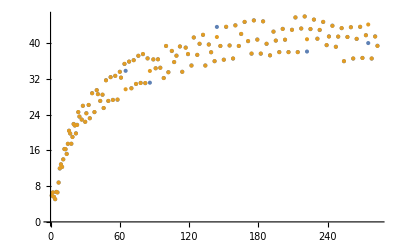

```mathematica
ListPlot[{
{pulseCount,1*^6 wheelDiameter π / pulsesPerRev /micSecPulse}ᵀ,
{pulseCount,speedInst}ᵀ
}] (* Exact Match *)
```

#### Examine the relationship between avg and inst. speed.

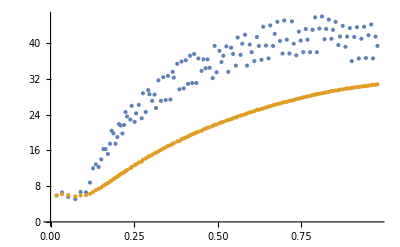

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet1ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

What we see, aside from what appears to be a clear accceleration of the speed as the engine winds up, is that the instantanaeous speed has a quite a bit more variation. This is probably because the magnetic locatoins and subsequent triggering is not uniform on the disk.  We can examine the correlation by picking out every nth point.

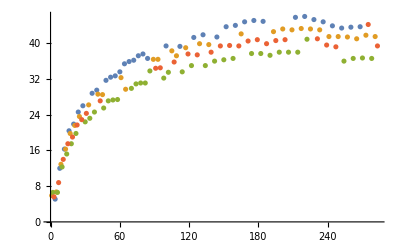

```mathematica
ListPlot[{
Select[{pulseCount,speedInst}ᵀ,(Mod[#⟦1⟧,4]==0)&],
Select[{pulseCount,speedInst}ᵀ,(Mod[#⟦1⟧,4]==1)&],
Select[{pulseCount,speedInst}ᵀ,(Mod[#⟦1⟧,4]==2)&],
Select[{pulseCount,speedInst}ᵀ,(Mod[#⟦1⟧,4]==3)&]
}]
```

As we can see. the spacing of the poles on the disks are not uniform.  Timing every 4th tick is a better way to go.

The total time is only accumulated every 4 ticks (one magnetic wheel rotation)

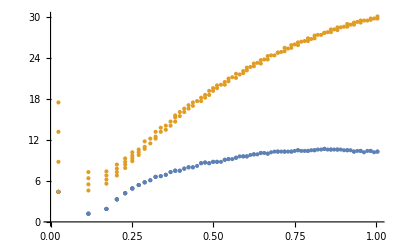

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet2ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

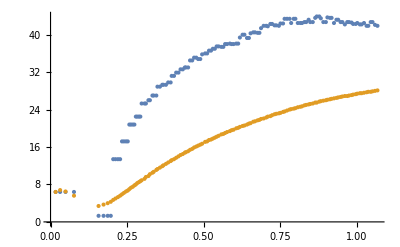

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet3ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

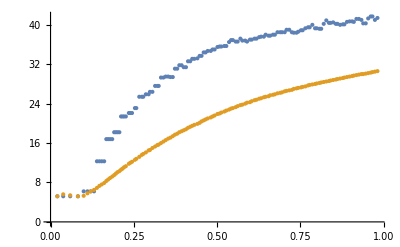

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet4ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

Results of many tests reveal that Inst. Speed overestimates the average. The average speed is closer but underestimates the actual average speed.

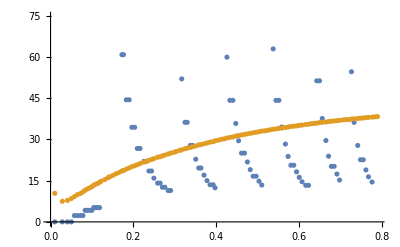

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet5ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

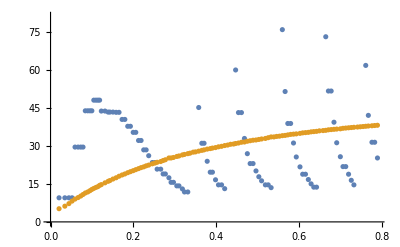

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet6ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ}]
```

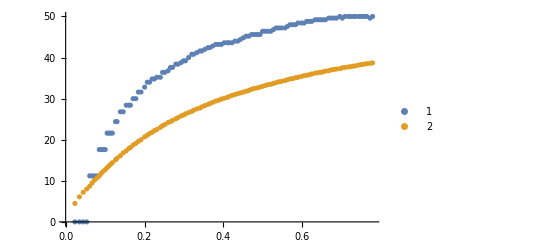

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet7ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst 4}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

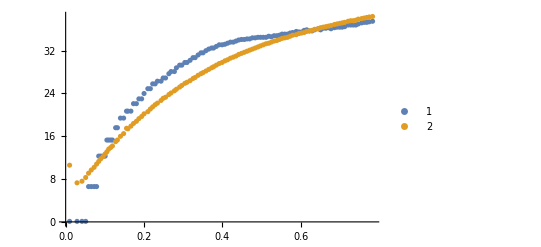

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet8ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

I discovered a small bug where the initial time on the pulse timers weren’t getting zeroed. This led to a slight offset in the instantaneous readings relative to the average.  This seems to have fixed the problem…  NO, I still have the kludge factor in.

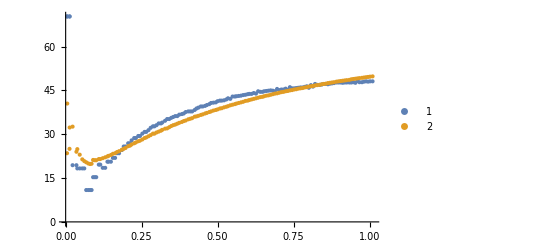

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet10ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

Take the kludge factor out and we have a large discrepancy in the inst. spd and average.

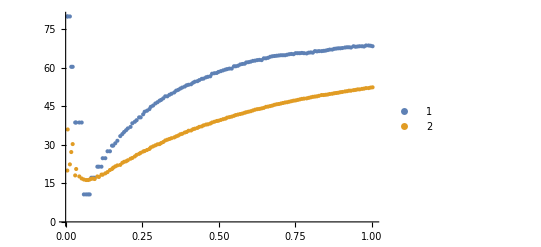

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet11ᵀ;ListPlot[{{timeStamp 1*^-6 ,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
measure = Import["/Users/pbeeken/Google Drive/dev/Arduino/PhysBot/Kinematics13.txt","tsv"];
velGr = Drop[Drop[measureᵀ⟦{1,3}⟧ᵀ,39],-40];
velGr={velGrᵀ⟦1⟧-Min[velGrᵀ⟦1⟧],velGrᵀ⟦2⟧ 100}ᵀ;
```

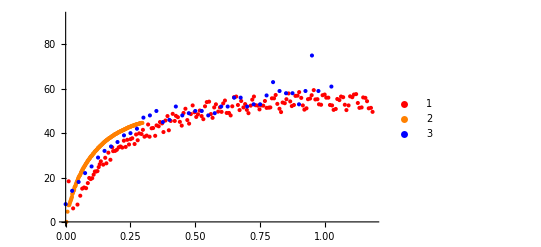

```mathematica
(*  We adjust the time marker to try to figure out what is going wrong *)
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet13ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6/4,speedAvg}ᵀ,velGr},PlotStyle->{Red,Orange,Blue}, PlotLegends->Automatic]
```

The modulo arithmetic is out. (We can see how the magnetic poles are not evenly spaced.) I shift the time values so we can see that the ‘average speed’ measurement is the one that is off.  Something is wrong with the way time is calculated.  Lets look at the difference between the ‘total time’ and accumulated time of the pulses.  They should agree.  CORRECTION: They should not.  I am not reporting every pulse in the output. I start out reporting every tick but the output can’t keep up so I start dropping the values which explains what we are seeing here.

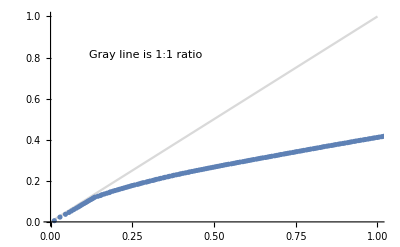

```mathematica
(* Plotting time vs accumulated time to see if the timer is the problem *)
Show[{
Plot[ x,{x,0,1.0},PlotStyle->LightGray],
ListPlot[{timeStamp 1*^-6 ,Accumulate[micSecPulse 1*^-6]}ᵀ],
Graphics[Text["Gray line is 1:1 ratio",Scaled[{0.3,0.8}]]]
}]
```

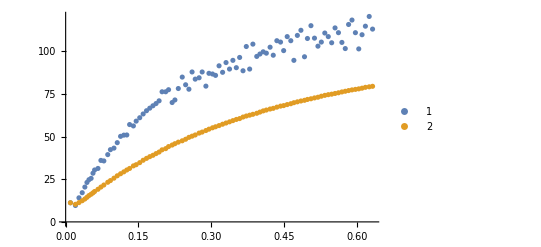

```mathematica
(* Another run after cleaning up some code to see if that fixes the problem *)
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet14ᵀ;ListPlot[{{timeStamp 1*^-6 ,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

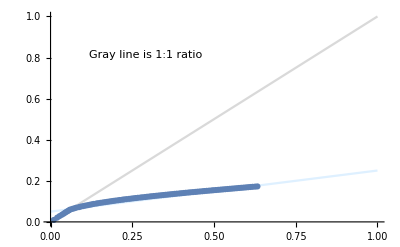

```mathematica
(* We now know that the accumulated time and actual time don't add up because we are not getting every point *)
Show[{
Plot[ x,{x,0,1.0},PlotStyle->LightGray],
Plot[ 0.05+x/5,{x,0,1.0},PlotStyle->LightBlue],
ListPlot[{timeStamp 1*^-6 ,Accumulate[micSecPulse 1*^-6]}ᵀ],
Graphics[Text["Gray line is 1:1 ratio",Scaled[{0.3,0.8}]]]
}]
```

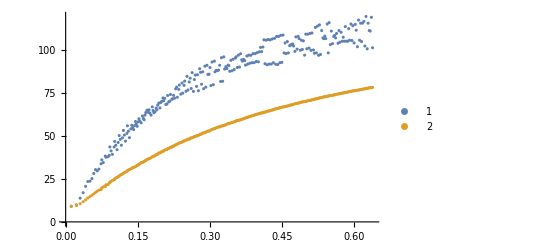

```mathematica
(* We tried, and failed, to get every point (not enough memory) but we increased the serial speed to see if we can compensate *)
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet15ᵀ;ListPlot[{{timeStamp 1*^-6 ,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

Well, that didn’t make the problem clear.

```mathematica
Differences[pulseCount]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,2,1,1,2,1,2,1,2,1,2,1,2,1,2,2,1,2,1,2,1,2,2,1,2,1,2,2,1,2,2,1,2,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,1,2,2,2,3,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,3,2,2,2,2,2,3,2,2,2,2,3,2,2,3,2,2,2,2,3,2,2,2,2,3,2,2,2,3,2,2,3,2,2,2,3,2,2,3,2,2,2,3,2,2,3,2,2,2,3,2,2,3,2,2,3,2,2,3,2,3}

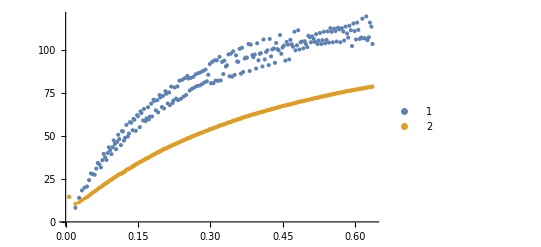

```mathematica
(* There is a new field: Accumulated time which is calculated in the robot. *)
{pulseCount,micSecPulse,distTrav, timeStamp,accumTime, speedInst, speedAvg} =dataSet20ᵀ;ListPlot[{{timeStamp 1*^-6 ,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

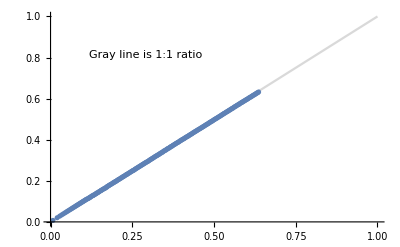

```mathematica
(* We now know that the accumulated time and actual time don't add up because we are not getting every point *)
Show[{
Plot[ x,{x,0,1.0},PlotStyle->LightGray],
ListPlot[{timeStamp 1*^-6 ,accumTime 1*^-6}ᵀ],
Graphics[Text["Gray line is 1:1 ratio",Scaled[{0.3,0.8}]]]
}]
```

Sanity check complete.  Accumulated time and elapsed time agree exactly!

### Begin servo tests:

#### Datasets

```mathematica
servoSet1 = {
{1,0,75,0.1,23148,4.6,4.6},{2,0,75,0.2,39748,4.6,5.4},{3,0,75,0.3,72612,4.6,4.4},{4,15,90,0.4,97020,4.6,4.4},{5,12,102,0.5,111412,7.4,4.8},{6,12,114,0.6,122668,7.4,5.2},{7,12,126,0.7,133464,7.4,5.6},{8,12,138,0.9,142756,7.4,6.0},{9,6,144,1.0,150620,13.5,6.4},{10,6,150,1.1,158328,13.5,6.7},{11,6,156,1.2,166384,13.5,7.0},{12,6,162,1.3,173296,13.5,7.4},{13,1,163,1.4,179068,18.4,7.7},{14,1,164,1.5,184744,18.4,8.1},{15,1,165,1.6,190952,18.4,8.4},{16,1,166,1.7,196660,18.4,8.7},{17,-1,165,1.8,201728,21.0,9.0},{18,-1,164,1.9,207028,21.0,9.2},{19,-1,163,2.0,212908,21.0,9.5},{20,-1,162,2.1,218128,21.0,9.8},{21,-3,159,2.2,222700,23.3,10.0},{22,-3,156,2.3,227376,23.3,10.3},{24,-3,153,2.6,237328,23.3,10.8},{26,-5,148,2.8,245824,25.5,11.2},{27,-5,143,2.9,250596,25.5,11.5},{29,-7,136,3.1,258816,27.5,11.9},{30,-7,129,3.3,267484,27.5,12.1},{32,-7,122,3.4,271772,27.5,12.5},{34,-8,114,3.6,279528,28.1,12.9},{36,-8,106,3.8,288148,28.1,13.3},{38,-8,98,4.0,295788,28.6,13.7},{39,-8,90,4.1,300180,28.6,13.8},{41,-9,81,4.4,307836,29.5,14.2},{43,-9,72,4.6,315888,29.5,14.5},{45,-9,63,4.8,323520,29.4,14.8},{46,-9,54,4.9,327308,29.4,14.9},{48,-9,45,5.1,335688,29.4,15.2},{50,-8,37,5.3,343352,28.7,15.5},{51,-8,29,5.4,347908,28.7,15.6},{53,-7,22,5.6,356108,27.3,15.8},{55,-7,15,5.8,365088,27.3,16.0},{56,-7,10,6.0,369668,27.3,16.1},{58,-5,10,6.2,378468,25.2,16.3},{59,-5,10,6.3,383856,25.2,16.3},{60,-5,10,6.4,389044,25.2,16.4},{62,-2,10,6.6,399112,22.0,16.5},{63,-2,10,6.7,405236,22.0,16.5},{64,-2,10,6.8,411068,22.0,16.6},{65,0,10,6.9,416400,20.0,16.6},{66,0,10,7.0,422024,20.0,16.6},{68,0,10,7.2,434856,20.0,16.6},{69,1,11,7.3,440744,18.1,16.7},{70,1,12,7.4,447184,18.1,16.6},{71,1,13,7.6,454820,18.1,16.6},{72,1,14,7.7,462264,18.1,16.6},{73,4,18,7.8,469252,15.2,16.5},{74,4,22,7.9,476832,15.2,16.5},{75,4,26,8.0,485688,15.2,16.4},{76,4,30,8.1,494096,15.2,16.4},{77,6,36,8.2,501824,13.8,16.3},{78,6,42,8.3,510048,13.8,16.3},{79,6,48,8.4,519608,13.8,16.2},{80,6,54,8.5,528624,13.8,16.1},{81,6,60,8.6,536564,13.4,16.1},{82,6,66,8.7,544560,13.4,16.0},{83,6,72,8.8,553160,13.4,16.0},{84,6,78,8.9,560676,13.4,15.9},{85,3,81,9.0,567100,16.6,15.9},{86,3,84,9.1,573716,16.6,15.9},{87,3,87,9.3,581320,16.6,15.9},{88,3,90,9.4,588524,16.6,15.9},{89,3,93,9.5,594860,16.8,15.9},{90,3,96,9.6,601188,16.8,15.9},{91,3,99,9.7,607980,16.8,15.9},{92,3,102,9.8,614000,16.8,15.9},{93,0,102,9.9,619228,20.4,16.0},{94,0,102,10.0,624640,20.4,16.0},{95,0,102,10.1,630796,20.4,16.0},{96,0,102,10.2,636552,20.4,16.0},{97,0,102,10.3,641696,20.7,16.1},{98,0,102,10.4,647016,20.7,16.1},{99,0,102,10.5,652936,20.7,16.1},{100,0,102,10.6,658376,20.7,16.2},{102,-1,101,10.8,668244,21.9,16.2},{103,-1,100,11.0,673880,21.9,16.3},{105,-3,97,11.2,683448,23.8,16.3},{106,-3,94,11.3,688136,23.8,16.4},{108,-3,91,11.5,698464,23.8,16.4},{109,-3,88,11.6,703024,23.3,16.5},{111,-3,85,11.8,713152,23.3,16.6},{112,-3,82,11.9,718044,23.3,16.6},{114,-4,78,12.1,727000,24.2,16.7},{115,-4,74,12.2,732152,24.2,16.7},{117,-5,69,12.4,741164,25.0,16.8},{118,-5,64,12.6,745568,25.0,16.8},{120,-5,59,12.8,755144,25.0,16.9},{122,-5,54,13.0,763768,25.5,17.0},{123,-5,49,13.1,768820,25.5,17.0},{125,-5,44,13.3,777792,25.0,17.1},{126,-5,39,13.4,782292,25.0,17.1},{128,-5,34,13.6,792340,25.0,17.2},{129,-3,31,13.7,796788,23.9,17.2},{131,-3,28,13.9,806836,23.9,17.3},{132,-3,25,14.0,811880,23.9,17.3},{134,-3,22,14.3,821356,23.2,17.4},{135,-3,19,14.4,827024,23.2,17.4},{137,-1,18,14.6,837384,21.4,17.4},{138,-1,17,14.7,842712,21.4,17.4},{139,-1,16,14.8,848980,21.4,17.4},{140,-1,15,14.9,855060,21.4,17.4},{141,1,16,15.1,866972,18.6,17.4},{142,1,17,15.1,866972,18.6,17.4},{143,1,18,15.3,881264,18.6,17.4},{145,3,21,15.4,887752,16.4,17.4},{146,3,24,15.5,894748,16.4,17.4},{147,3,27,15.6,902936,16.4,17.3},{148,3,30,15.7,910808,16.4,17.3},{149,5,35,15.8,917988,14.8,17.3},{150,5,40,16.0,925600,14.8,17.2},{151,5,45,16.1,934396,14.8,17.2},{152,5,50,16.2,942724,14.8,17.1},{153,5,55,16.3,950204,14.2,17.1},{154,5,60,16.4,957952,14.2,17.1},{155,5,65,16.5,966416,14.2,17.1},{156,5,70,16.6,973872,14.2,17.0},{157,3,73,16.7,980332,16.5,17.0},{158,3,76,16.8,987040,16.5,17.0},{159,3,79,16.9,994672,16.5,17.0},{160,3,82,17.0,1001760,16.5,17.0},{161,3,85,17.1,1008076,16.8,17.0},{162,3,88,17.2,1014500,16.8,17.0},{163,3,91,17.3,1021496,16.8,17.0},{164,3,94,17.4,1027868,16.8,17.0},{165,1,95,17.5,1033548,18.7,17.0},{166,1,96,17.7,1039520,18.7,17.0},{167,1,97,17.8,1046208,18.7,17.0},{168,1,98,17.9,1052236,18.7,17.0},{169,0,98,18.0,1057460,20.4,17.0},{170,0,98,18.1,1062764,20.4,17.0},{172,0,98,18.3,1074208,20.4,17.0},{173,-1,97,18.4,1079236,21.2,17.0},{175,-1,96,18.6,1090280,21.2,17.1},{176,-1,95,18.7,1095668,21.2,17.1},{177,-1,94,18.9,1100532,21.9,17.1},{179,-1,93,19.0,1111604,21.9,17.1},{180,-1,92,19.1,1117048,21.9,17.1},{182,-1,91,19.4,1126836,22.0,17.2},{183,-1,90,19.5,1132336,22.0,17.2},{185,-3,87,19.7,1141944,23.3,17.2},{186,-3,84,19.8,1146796,23.3,17.2},{188,-3,81,20.0,1157496,23.3,17.3},{189,-3,78,20.1,1162104,23.1,17.3},{191,-3,75,20.3,1172428,23.1,17.3},{192,-3,72,20.4,1177548,23.1,17.3},{194,-3,69,20.6,1186976,23.1,17.4},{195,-3,66,20.7,1192360,23.1,17.4},{197,-4,62,21.0,1201680,24.2,17.4},{198,-4,58,21.1,1206296,24.2,17.5},{200,-4,54,21.3,1216424,24.2,17.5},{201,-4,50,21.4,1220840,24.1,17.5},{203,-4,46,21.6,1230716,24.1,17.5},{204,-4,42,21.8,1240184,23.5,17.6},{206,-3,39,21.9,1245008,23.5,17.6},{207,-3,36,22.0,1250512,23.5,17.6},{209,-3,33,22.2,1260272,23.0,17.6},{210,-3,30,22.3,1265164,23.0,17.7},{212,-3,27,22.5,1276176,23.0,17.7},{213,-1,26,22.7,1281176,21.3,17.7},{214,-1,25,22.8,1286552,21.3,17.7},{216,-1,24,23.0,1298776,21.3,17.7},{217,0,24,23.1,1304312,19.2,17.7},{218,0,24,23.2,1310320,19.2,17.7},{219,0,24,23.3,1317416,19.2,17.7},{220,0,24,23.4,1324196,19.2,17.7},{221,2,26,23.5,1330384,17.2,17.7},{222,2,28,23.6,1336956,17.2,17.7},{223,2,30,23.7,1344532,17.2,17.6},{225,4,34,23.9,1358552,15.7,17.6},{226,4,38,24.0,1365992,15.7,17.6},{227,4,42,24.1,1374612,15.7,17.6},{228,4,46,24.2,1382516,15.7,17.5},{229,4,50,24.4,1389564,15.1,17.5},{230,4,54,24.5,1397200,15.1,17.5},{231,4,58,24.6,1406028,15.1,17.5},{232,4,62,24.7,1414124,15.1,17.4},{233,5,67,24.8,1421252,14.9,17.4},{234,5,72,24.9,1428480,14.9,17.4},{235,5,77,25.0,1436528,14.9,17.4},{236,5,82,25.1,1443948,14.9,17.4},{237,3,85,25.2,1450512,16.2,17.4},{238,3,88,25.3,1457348,16.2,17.4},{239,3,91,25.4,1465020,16.2,17.4},{240,3,94,25.5,1471940,16.2,17.3},{241,2,96,25.6,1477944,17.7,17.3},{242,2,98,25.7,1484156,17.7,17.3},{243,2,100,25.8,1491200,17.7,17.3},{244,2,102,26.0,1497572,17.7,17.3},{245,1,103,26.1,1503216,18.9,17.3},{246,1,104,26.2,1509104,18.9,17.3},{247,1,105,26.3,1515680,18.9,17.3},{249,0,105,26.5,1527108,19.7,17.3},{250,0,105,26.6,1532688,19.7,17.3},{251,0,105,26.7,1538952,19.7,17.3},{253,0,105,26.9,1549788,21.0,17.4},{254,0,105,27.0,1555052,21.0,17.4},{255,0,105,27.1,1561012,21.0,17.4},{257,-1,104,27.3,1571660,21.3,17.4},{258,-1,103,27.4,1576788,21.3,17.4},{259,-1,102,27.7,1587912,21.3,17.4},{261,-2,100,27.8,1592692,22.3,17.4},{262,-2,98,27.9,1597720,22.3,17.4},{264,-2,96,28.1,1608528,22.3,17.5},{265,-2,94,28.3,1618116,22.5,17.5},{267,-2,92,28.4,1623600,22.5,17.5},{268,-2,90,28.5,1628684,22.5,17.5},{270,-3,87,28.7,1638236,23.0,17.5},{271,-3,84,28.8,1643848,23.0,17.5},{273,-3,81,29.0,1653636,23.2,17.6},{274,-3,78,29.1,1658392,23.2,17.6},{276,-3,75,29.4,1668872,23.2,17.6},{277,-3,72,29.5,1673480,23.1,17.6},{279,-3,69,29.7,1683756,23.1,17.6},{280,-3,66,29.8,1688856,23.1,17.6},{282,-3,63,30.0,1698428,23.0,17.7} };
```

```mathematica
servoSet2 = {{1,0,75,0.1,22144,4.8,4.8},{2,0,75,0.2,40152,4.8,5.3},{3,0,75,0.3,77012,4.8,4.1},{4,15,82,0.4,104524,4.8,4.1},{5,13,88,0.5,120832,6.5,4.4},{6,13,94,0.6,133264,6.5,4.8},{7,13,100,0.7,144688,6.5,5.1},{8,13,106,0.9,156352,6.5,5.4},{9,9,110,1.0,166060,11.0,5.8},{10,9,114,1.1,173908,11.0,6.1},{11,9,118,1.2,181496,11.0,6.4},{12,9,122,1.3,189764,11.0,6.7},{13,5,124,1.4,197280,14.2,7.0},{14,5,126,1.5,203864,14.2,7.3},{15,5,128,1.6,210552,14.2,7.6},{16,5,130,1.7,217664,14.2,7.8},{17,2,131,1.8,223828,17.3,8.1},{18,2,132,1.9,229060,17.3,8.4},{19,2,133,2.0,234436,17.3,8.6},{20,2,134,2.1,240384,17.3,8.8},{21,0,134,2.2,245900,19.3,9.1},{22,0,134,2.3,250864,19.3,9.3},{23,0,134,2.4,255932,19.3,9.6},{24,0,134,2.6,261492,19.3,9.8},{25,-1,134,2.7,266528,21.2,10.0},{26,-1,134,2.8,270944,21.2,10.2},{28,-1,134,3.0,280728,21.2,10.6},{30,-2,133,3.2,289572,22.6,11.0},{31,-2,132,3.3,293836,22.6,11.2},{33,-4,130,3.5,302812,24.7,11.6},{35,-4,128,3.7,310756,24.7,12.0},{36,-4,126,3.8,315392,24.7,12.1},{38,-5,124,4.0,323368,25.4,12.5},{40,-5,122,4.3,331900,25.4,12.8},{41,-5,120,4.4,336116,25.3,13.0},{43,-5,118,4.6,343724,25.3,13.3},{45,-6,115,4.8,352016,26.8,13.6},{47,-6,112,5.0,359304,26.8,13.9},{49,-6,109,5.2,367584,26.6,14.2},{51,-6,106,5.4,374912,26.6,14.5},{52,-6,103,5.5,379176,26.6,14.6},{54,-6,100,5.7,386768,26.6,14.8},{56,-6,97,6.0,394740,26.6,15.1},{58,-7,94,6.2,402060,27.5,15.3},{60,-7,91,6.4,409732,27.5,15.6},{62,-8,87,6.6,416912,28.2,15.8},{63,-8,83,6.8,424592,28.2,16.0},{65,-7,80,6.9,428464,27.5,16.1},{67,-7,77,7.1,435720,27.5,16.4},{69,-7,74,7.3,443860,27.2,16.5},{71,-7,71,7.6,450996,27.2,16.7},{73,-7,68,7.8,458912,27.9,16.9},{75,-7,65,8.0,465920,27.9,17.1},{76,-7,62,8.1,469988,27.9,17.2},{78,-7,59,8.3,477268,27.9,17.4},{80,-7,56,8.5,485228,27.9,17.5},{82,-6,53,8.7,492820,26.6,17.7},{84,-6,50,8.9,500836,26.6,17.8},{85,-6,47,9.1,508388,26.8,17.9},{87,-6,44,9.3,512156,26.8,18.1},{89,-6,41,9.5,520472,26.4,18.2},{91,-6,38,9.7,527968,26.4,18.3},{92,-6,35,9.8,532396,26.4,18.4},{94,-5,33,10.0,540384,25.4,18.5},{96,-5,31,10.2,549060,25.4,18.6},{97,-4,29,10.4,557452,24.3,18.6},{99,-4,27,10.5,561740,24.3,18.7},{101,-2,26,10.7,571416,22.6,18.8},{102,-2,25,10.8,575716,22.6,18.8},{104,-2,24,11.1,585632,22.6,18.9},{105,-1,24,11.2,590692,21.0,18.9},{107,-1,24,11.4,600292,21.0,19.0},{108,-1,24,11.5,605988,21.0,19.0},{109,0,24,11.6,611364,19.8,19.0},{111,0,24,11.8,621508,19.8,19.0},{112,0,24,11.9,627532,19.8,19.0},{113,1,24,12.0,633264,18.6,19.0},{114,1,24,12.2,644072,18.6,19.0},{116,1,24,12.3,650520,18.6,19.0},{117,2,25,12.4,656640,17.4,19.0},{118,2,26,12.6,662256,17.4,19.0},{119,2,27,12.7,668272,17.4,18.9},{120,2,28,12.8,675204,17.4,18.9},{121,3,29,12.9,681744,16.3,18.9},{122,3,30,13.1,694040,16.3,18.8},{123,3,31,13.1,694040,16.3,18.8},{124,3,32,13.2,701440,16.3,18.8},{126,5,34,13.4,715064,15.0,18.7},{127,5,36,13.5,721996,15.0,18.7},{128,5,38,13.6,729812,15.0,18.7},{129,5,40,13.7,737060,14.7,18.6},{130,5,42,13.8,743648,14.7,18.6},{131,5,44,13.9,750684,14.7,18.6},{132,5,46,14.0,758768,14.7,18.5},{133,5,48,14.1,766192,14.3,18.5},{134,5,50,14.3,772696,14.3,18.4},{135,5,52,14.4,779376,14.3,18.4},{136,5,54,14.5,786860,14.3,18.4},{137,4,56,14.6,793880,15.2,18.4},{138,4,58,14.7,800256,15.2,18.3},{139,4,60,14.8,806984,15.2,18.3},{140,4,62,14.9,814444,15.2,18.3},{141,4,64,15.0,821148,15.9,18.3},{142,4,66,15.1,826992,15.9,18.3},{143,4,68,15.2,833164,15.9,18.3},{144,4,70,15.3,840296,15.9,18.2},{145,4,72,15.4,846988,15.9,18.2},{146,4,74,15.5,852884,15.9,18.2},{147,4,76,15.7,865468,15.9,18.2},{149,2,77,15.8,871516,17.6,18.2},{150,2,78,16.0,876928,17.6,18.2},{151,2,79,16.1,882632,17.6,18.2},{152,2,80,16.2,889108,17.6,18.2},{154,2,81,16.4,900224,17.9,18.2},{155,2,82,16.5,905520,17.9,18.2},{156,2,83,16.6,911496,17.9,18.2},{158,1,83,16.8,922180,19.0,18.2},{159,1,83,16.9,927536,19.0,18.2},{160,1,83,17.0,933460,19.0,18.2},{162,0,83,17.2,943568,19.9,18.3},{163,0,83,17.3,948488,19.9,18.3},{164,0,83,17.4,954076,19.9,18.3},{166,0,83,17.7,963892,20.5,18.3},{167,0,83,17.8,968720,20.5,18.3},{169,-1,83,18.0,979232,21.0,18.4},{170,-1,83,18.1,983824,21.0,18.4},{172,-1,83,18.3,994176,21.0,18.4},{173,-1,83,18.4,999192,21.2,18.4},{175,-1,83,18.6,1008280,21.2,18.5},{176,-1,83,18.7,1013512,21.2,18.5},{178,-1,83,18.9,1022832,21.7,18.5},{179,-1,83,19.0,1027484,21.7,18.5},{181,-2,82,19.3,1037516,22.2,18.6},{182,-2,81,19.5,1046396,22.2,18.6},{184,-2,80,19.6,1051636,22.2,18.6},{186,-1,80,19.8,1060828,21.9,18.6},{187,-1,80,19.9,1065316,21.9,18.7},{189,-2,79,20.1,1075080,22.6,18.7},{190,-2,78,20.3,1083796,22.6,18.7},{192,-2,77,20.4,1088892,22.6,18.8},{194,-2,76,20.6,1097832,22.6,18.8},{195,-2,75,20.7,1102340,22.6,18.8},{197,-1,75,21.0,1112348,21.9,18.8},{198,-1,75,21.2,1121240,21.9,18.9},{200,-1,75,21.3,1126336,21.9,18.9},{202,-2,74,21.5,1135404,22.5,18.9},{203,-2,73,21.6,1140012,22.5,18.9},{205,-1,73,21.8,1150212,21.7,19.0},{206,-1,73,21.9,1154596,21.7,19.0},{208,-1,73,22.1,1164292,21.7,19.0},{209,-1,73,22.2,1169220,21.6,19.0},{211,-1,73,22.4,1178460,21.6,19.0},{212,-1,73,22.5,1183804,21.6,19.0},{214,-1,73,22.8,1193120,21.7,19.1},{216,-1,73,23.0,1203000,21.7,19.1},{217,-1,73,23.1,1207948,21.5,19.1},{219,-1,73,23.3,1217036,21.5,19.1},{220,-1,73,23.4,1222304,21.5,19.1},{222,-1,73,23.6,1231784,21.4,19.2},{223,-1,73,23.7,1236588,21.4,19.2},{225,-1,73,23.9,1246964,21.5,19.2},{226,-1,73,24.1,1255900,21.5,19.2},{228,-1,73,24.2,1261056,21.5,19.2},{230,-2,72,24.5,1270300,22.1,19.3},{231,-2,71,24.6,1274892,22.1,19.3},{233,-1,71,24.8,1285164,21.3,19.3},{234,-1,71,24.9,1289736,21.3,19.3},{236,-1,71,25.1,1300248,21.3,19.3},{237,0,71,25.2,1305384,20.7,19.3},{239,0,71,25.4,1314556,20.7,19.3},{240,0,71,25.5,1319752,20.7,19.3},{242,-2,70,25.7,1328980,22.0,19.4},{243,-2,69,25.8,1333720,22.0,19.4},{245,0,69,26.1,1344244,20.9,19.4},{246,0,69,26.2,1348840,20.9,19.4},{248,0,69,26.4,1359380,20.9,19.4},{249,0,69,26.5,1364616,20.3,19.4},{251,0,69,26.7,1374064,20.3,19.4},{252,0,69,26.8,1379380,20.3,19.4},{254,-1,69,27.0,1388648,21.8,19.5},{255,-1,69,27.1,1393284,21.8,19.5},{257,-1,69,27.3,1403584,21.3,19.5},{258,-1,69,27.4,1408128,21.3,19.5},{260,-1,69,27.7,1418584,21.3,19.5},{261,0,69,27.8,1423816,20.3,19.5},{263,0,69,28.0,1433500,20.3,19.5},{264,0,69,28.1,1439012,20.3,19.5},{265,-1,69,28.2,1444052,21.1,19.5},{267,-1,69,28.4,1453220,21.1,19.5},{268,-1,69,28.5,1458640,21.1,19.5},{270,0,69,28.7,1468328,20.9,19.6},{271,0,69,28.8,1473172,20.9,19.6},{273,0,69,29.0,1483872,20.5,19.6},{274,0,69,29.1,1488528,20.5,19.6},{276,0,69,29.4,1498964,20.5,19.6},{277,-1,69,29.5,1504032,21.0,19.6},{279,-1,69,29.7,1513172,21.0,19.6},{280,-1,69,29.8,1518460,21.0,19.6},{282,-1,69,30.0,1527912,21.5,19.6}};
```

```mathematica
servoSet3 = {{1,0,75,0.1,18388,5.8,5.8},{2,0,75,0.2,37256,5.8,5.7},{3,0,75,0.3,54564,5.8,5.8},{4,14,78,0.4,71700,5.8,5.9},{5,11,80,0.5,84632,8.2,6.3},{6,11,82,0.6,96220,8.2,6.6},{7,11,84,0.7,106244,8.2,7.0},{8,11,86,0.9,115040,8.2,7.4},{9,7,87,1.0,123868,12.1,7.7},{10,7,88,1.1,133216,12.1,8.0},{11,7,89,1.2,141196,12.1,8.3},{12,7,90,1.3,147912,12.1,8.6},{13,4,91,1.4,154724,15.6,8.9},{14,4,92,1.5,162420,15.6,9.2},{15,4,93,1.6,169596,15.6,9.4},{16,4,94,1.7,175968,15.6,9.7},{17,3,94,1.8,182412,16.5,9.9},{18,3,94,1.9,189304,16.5,10.1},{19,3,94,2.0,195408,16.5,10.3},{20,3,94,2.1,200732,16.5,10.6},{21,0,94,2.2,206216,19.4,10.8},{22,0,94,2.3,212424,19.4,11.0},{23,0,94,2.4,218196,19.4,11.2},{24,0,94,2.6,223256,19.4,11.4},{25,0,94,2.7,228444,20.5,11.6},{26,0,94,2.8,234188,20.5,11.8},{27,0,94,2.9,239452,20.5,12.0},{28,0,94,3.0,244196,20.5,12.2},{29,-1,94,3.1,249172,21.4,12.4},{31,-1,94,3.3,259804,21.4,12.7},{32,-1,94,3.4,264252,21.4,12.9},{34,-2,94,3.6,274168,22.8,13.2},{35,-2,94,3.7,279036,22.8,13.3},{37,-3,94,3.9,287964,23.4,13.7},{38,-3,94,4.0,293056,23.4,13.8},{40,-3,94,4.3,301936,23.4,14.1},{41,-3,94,4.4,306376,24.0,14.2},{43,-3,94,4.6,316168,24.0,14.5},{44,-3,94,4.7,320356,24.0,14.6},{46,-4,93,4.9,329448,24.8,14.9},{47,-4,92,5.0,333888,24.8,15.0},{49,-5,91,5.2,342080,25.3,15.2},{50,-5,90,5.4,351244,25.3,15.4},{52,-5,89,5.5,355148,25.3,15.6},{54,-5,88,5.7,363924,25.9,15.8},{55,-5,87,6.0,372224,25.9,15.9},{57,-5,86,6.1,376320,26.0,16.1},{59,-5,85,6.3,385168,26.0,16.3},{60,-6,84,6.5,392984,26.5,16.5},{62,-6,83,6.6,397508,26.5,16.6},{64,-6,82,6.8,405472,26.5,16.8},{66,-6,81,7.0,413872,27.0,17.0},{67,-6,80,7.1,418048,27.0,17.0},{69,-6,79,7.3,425804,26.7,17.2},{71,-6,78,7.6,434460,26.7,17.4},{72,-6,77,7.7,438192,26.7,17.5},{74,-6,76,7.9,446652,26.9,17.6},{76,-6,75,8.1,454724,26.9,17.8},{77,-6,74,8.2,458732,26.6,17.9},{79,-6,73,8.4,467456,26.6,18.0},{81,-6,72,8.6,475236,26.6,18.1},{82,-6,71,8.7,479788,26.6,18.2},{84,-6,70,8.9,487764,26.6,18.3},{86,-6,69,9.1,496244,26.8,18.4},{88,-6,68,9.4,504344,26.8,18.6},{89,-6,67,9.5,508428,26.1,18.6},{91,-6,66,9.7,517340,26.1,18.7},{93,-5,65,9.9,525340,25.8,18.8},{94,-5,64,10.0,530012,25.8,18.9},{96,-5,63,10.2,538252,25.8,19.0},{97,-6,62,10.3,542320,26.2,19.0},{99,-6,61,10.5,551200,26.2,19.1},{101,-6,60,10.7,559164,26.0,19.2},{103,-6,59,11.0,568144,26.0,19.3},{104,-6,58,11.1,572048,26.0,19.3},{106,-5,57,11.3,580948,25.7,19.4},{108,-5,56,11.5,589520,25.7,19.5},{109,-4,55,11.6,593796,24.9,19.5},{111,-4,54,11.8,603044,24.9,19.6},{113,-5,53,12.0,611280,25.2,19.7},{114,-5,52,12.1,616096,25.2,19.7},{116,-5,51,12.3,624608,25.2,19.8},{118,-4,50,12.6,633852,24.8,19.8},{119,-4,49,12.7,638528,24.8,19.8},{121,-3,49,12.9,647312,23.6,19.9},{122,-3,49,13.0,652412,23.6,19.9},{124,-3,49,13.2,661392,23.6,19.9},{125,-3,49,13.3,665868,23.8,20.0},{127,-3,49,13.5,675800,23.8,20.0},{129,-3,49,13.7,684724,23.2,20.0},{130,-3,49,13.8,689984,23.2,20.0},{132,-3,49,14.0,699668,23.2,20.1},{133,-1,49,14.1,704632,21.4,20.1},{134,-1,49,14.3,710292,21.4,20.1},{136,-1,49,14.5,720176,21.4,20.1},{137,-1,49,14.6,725056,21.8,20.1},{139,-1,49,14.8,735760,21.8,20.1},{140,-1,49,14.9,740504,21.8,20.1},{141,-1,49,15.0,745560,21.1,20.1},{143,-1,49,15.2,756864,21.1,20.1},{144,-1,49,15.3,761924,21.1,20.1},{145,0,49,15.4,767340,19.7,20.1},{147,0,49,15.6,779244,19.7,20.1},{148,0,49,15.7,784296,19.7,20.1},{149,0,49,15.8,789500,20.5,20.1},{151,0,49,16.1,800664,20.5,20.1},{152,0,49,16.2,805496,20.5,20.1},{153,0,49,16.3,810640,20.7,20.1},{155,0,49,16.5,822112,20.7,20.1},{156,0,49,16.6,827192,20.7,20.1},{157,0,49,16.7,832620,19.6,20.1},{158,0,49,16.8,838860,19.6,20.0},{160,0,49,17.0,849964,19.6,20.0},{161,0,49,17.1,855380,19.7,20.0},{162,0,49,17.2,861428,19.7,20.0},{164,0,49,17.4,871996,19.7,20.0},{165,0,49,17.5,877332,19.9,20.0},{166,0,49,17.7,883516,19.9,20.0},{167,0,49,17.8,889364,19.9,20.0},{169,1,49,18.0,900272,19.0,20.0},{170,1,49,18.1,906676,19.0,19.9},{171,1,49,18.2,912652,19.0,19.9},{172,1,49,18.3,918008,19.0,19.9},{174,0,49,18.5,929816,19.1,19.9},{175,0,49,18.6,935544,19.1,19.9},{176,0,49,18.7,940640,19.1,19.9},{177,0,49,18.8,945980,19.9,19.9},{179,0,49,19.0,957776,19.9,19.9},{180,0,49,19.1,962896,19.9,19.9},{181,0,49,19.3,968268,19.8,19.9},{182,0,49,19.5,980104,19.8,19.9},{184,0,49,19.6,985340,19.8,19.9},{185,0,49,19.7,990920,19.1,19.9},{186,0,49,19.8,997252,19.1,19.8},{188,0,49,20.0,1008236,19.1,19.8},{189,0,49,20.1,1013612,19.8,19.8},{190,0,49,20.2,1019692,19.8,19.8},{191,0,49,20.4,1030580,19.8,19.9},{193,0,49,20.5,1036096,19.3,19.8},{194,0,49,20.6,1042344,19.3,19.8},{195,0,49,20.7,1048208,19.3,19.8},{197,1,49,21.0,1059312,18.6,19.8},{198,1,49,21.1,1065804,18.6,19.8},{199,1,49,21.2,1071784,18.6,19.7},{200,1,49,21.3,1077096,18.6,19.7},{202,0,49,21.5,1088708,19.4,19.7},{203,0,49,21.6,1094400,19.4,19.7},{204,0,49,21.7,1099584,19.4,19.7},{205,1,49,21.8,1105188,19.0,19.7},{207,1,49,22.0,1117696,19.0,19.7},{208,1,49,22.1,1123116,19.0,19.7},{209,1,49,22.2,1128880,18.5,19.7},{210,1,49,22.3,1135456,18.5,19.7},{212,1,49,22.5,1147040,18.5,19.7},{213,1,49,22.7,1152724,18.7,19.7},{214,1,49,22.8,1159108,18.7,19.6},{215,1,49,22.9,1165092,18.7,19.6},{217,1,49,23.1,1176476,18.0,19.6},{218,1,49,23.2,1183332,18.0,19.6},{219,1,49,23.3,1189732,18.0,19.6},{220,1,49,23.4,1195412,18.0,19.6},{221,2,49,23.5,1201356,17.9,19.6},{222,2,49,23.6,1208136,17.9,19.5},{224,2,49,23.8,1220468,17.9,19.5},{225,2,49,23.9,1226648,17.2,19.5},{226,2,49,24.0,1233556,17.2,19.5},{227,2,49,24.1,1239908,17.2,19.5},{228,2,49,24.2,1245652,17.2,19.5},{229,2,49,24.4,1251816,17.3,19.5},{230,2,49,24.5,1258988,17.3,19.4},{231,2,49,24.7,1271960,17.3,19.4},{233,3,49,24.8,1278280,16.8,19.4},{234,3,49,24.9,1285384,16.8,19.4},{235,3,49,25.0,1292032,16.8,19.3},{236,3,49,25.1,1298104,16.8,19.3},{237,3,49,25.2,1304640,16.3,19.3},{238,3,49,25.3,1312056,16.3,19.3},{239,3,49,25.4,1318788,16.3,19.3},{240,3,49,25.5,1324760,16.3,19.3},{241,3,49,25.6,1331080,16.8,19.3},{242,3,49,25.7,1338412,16.8,19.2},{244,3,49,26.0,1351848,16.8,19.2},{245,4,50,26.1,1358540,15.9,19.2},{246,4,51,26.2,1365932,15.9,19.2},{247,4,52,26.3,1372676,15.9,19.1},{248,4,53,26.4,1378724,15.9,19.1},{249,3,53,26.5,1385136,16.6,19.1},{250,3,53,26.6,1392500,16.6,19.1},{251,3,53,26.7,1399340,16.6,19.1},{252,3,53,26.8,1405412,16.6,19.1},{253,3,53,26.9,1411712,16.9,19.1},{254,3,53,27.1,1425412,16.9,19.0},{256,3,53,27.2,1431472,16.9,19.0},{257,3,53,27.3,1437972,16.4,19.0},{258,3,53,27.4,1445324,16.4,19.0},{259,3,53,27.5,1451992,16.4,19.0},{260,3,53,27.7,1457872,16.4,19.0},{261,2,53,27.8,1464080,17.1,19.0},{262,2,53,27.9,1471300,17.1,18.9},{263,2,53,28.0,1478208,17.1,18.9},{265,3,53,28.2,1490884,16.5,18.9},{266,3,53,28.3,1498056,16.5,18.9},{267,3,53,28.4,1504768,16.5,18.9},{268,3,53,28.5,1510944,16.5,18.9},{269,3,53,28.6,1517584,16.0,18.9},{270,3,53,28.7,1525192,16.0,18.8},{271,3,53,28.8,1532148,16.0,18.8},{272,3,53,28.9,1538224,16.0,18.8},{273,3,53,29.0,1544532,16.9,18.8},{274,3,53,29.1,1551792,16.9,18.8},{275,3,53,29.2,1558800,16.9,18.8},{276,3,53,29.4,1565232,16.9,18.8},{277,4,54,29.5,1572008,15.7,18.7},{278,4,55,29.6,1579572,15.7,18.7},{280,4,56,29.8,1592728,15.7,18.7},{281,3,56,29.9,1599360,16.0,18.7},{282,3,56,30.0,1606992,16.0,18.7}};
```

```mathematica
servoSet4 = {{1,0,75,0.1,27604,3.9,3.9},{2,0,75,0.2,43108,3.9,4.9},{3,0,75,0.3,78512,3.9,4.1},{4,36,84,0.4,107820,3.9,3.9},{5,33,92,0.5,125476,6.0,4.2},{6,33,100,0.6,138416,6.0,4.6},{7,33,108,0.7,150860,6.0,4.9},{8,33,116,0.9,161932,6.0,5.3},{9,28,123,1.0,171404,11.2,5.6},{10,28,130,1.1,180448,11.2,5.9},{11,28,137,1.2,189572,11.2,6.2},{12,28,144,1.3,197156,11.2,6.5},{13,23,149,1.4,203464,16.9,6.8},{14,23,154,1.5,209804,16.9,7.1},{15,23,159,1.6,216788,16.9,7.4},{16,23,164,1.7,223144,16.9,7.6},{17,20,169,1.8,228696,19.2,7.9},{18,20,174,1.9,234392,19.2,8.2},{19,20,179,2.0,240492,19.2,8.4},{20,20,184,2.1,245864,19.2,8.7},{21,17,188,2.2,250620,22.4,8.9},{22,17,192,2.3,255512,22.4,9.2},{23,17,196,2.4,261040,22.4,9.4},{24,17,200,2.6,266104,22.4,9.6},{26,15,203,2.8,274972,24.3,10.1},{27,15,206,3.0,284228,24.3,10.5},{29,12,209,3.1,288124,27.3,10.7},{31,12,212,3.3,296812,27.3,11.1},{33,11,214,3.5,304796,28.5,11.5},{34,11,216,3.6,308740,28.5,11.7},{36,11,218,3.8,317300,28.5,12.1},{38,11,220,4.0,324816,29.0,12.4},{40,11,222,4.3,332908,29.0,12.8},{42,8,224,4.5,339856,31.3,13.1},{44,8,226,4.7,347568,31.3,13.5},{46,7,227,4.9,354284,32.2,13.8},{48,7,228,5.1,361756,32.2,14.1},{50,7,229,5.3,368376,32.8,14.4},{52,7,230,5.5,375684,32.8,14.7},{54,5,231,5.7,381932,34.8,15.0},{56,5,232,6.0,388780,34.8,15.3},{58,4,233,6.2,394812,35.8,15.6},{60,4,234,6.4,401576,35.8,15.9},{62,3,234,6.7,411024,36.7,16.3},{65,2,234,6.9,417104,37.1,16.6},{67,2,234,7.1,423352,37.1,16.8},{69,0,234,7.4,431944,39.4,17.2},{72,0,234,7.7,438104,39.4,17.5},{74,0,234,7.9,443552,39.9,17.7},{77,0,234,8.2,452352,40.2,18.1},{79,0,234,8.4,458256,40.2,18.3},{82,-1,234,8.7,466368,41.5,18.7},{84,-1,234,8.9,472228,41.5,18.9},{87,-2,234,9.3,480404,42.0,19.3},{89,-2,234,9.6,488360,42.5,19.5},{92,-2,234,9.8,494084,42.5,19.8},{95,-3,234,10.1,501980,43.7,20.1},{98,-4,233,10.4,509584,44.0,20.5},{100,-4,232,10.6,515088,44.0,20.6},{103,-4,231,11.0,522840,44.6,21.0},{106,-5,230,11.3,530296,45.5,21.3},{109,-5,229,11.6,538024,45.7,21.5},{112,-5,228,11.9,545808,45.7,21.8},{115,-6,227,12.2,553292,46.1,22.1},{118,-6,226,12.6,560560,46.1,22.4},{121,-7,225,12.9,568068,47.1,22.7},{124,-7,224,13.2,575660,47.1,22.9},{127,-7,223,13.5,582956,47.6,23.2},{130,-7,222,13.8,590080,47.3,23.4},{133,-7,221,14.1,597476,47.3,23.7},{136,-7,220,14.5,604884,47.3,23.9},{139,-7,219,14.9,614492,47.9,24.2},{143,-8,217,15.2,621656,48.2,24.5},{146,-8,215,15.5,628572,48.7,24.7},{149,-9,213,15.8,635796,49.1,24.9},{152,-9,211,16.2,643084,49.1,25.1},{155,-9,209,16.5,650136,49.5,25.4},{158,-9,207,16.8,656940,49.8,25.6},{162,-9,205,17.2,666280,49.6,25.9},{165,-10,203,17.5,673324,50.1,26.1},{168,-10,201,17.9,680468,50.1,26.3},{171,-10,199,18.3,689648,50.1,26.5},{175,-10,197,18.6,696452,50.8,26.7},{178,-11,195,18.9,703056,51.0,26.9},{182,-10,193,19.4,712208,50.7,27.2},{185,-11,191,19.7,719104,51.3,27.4},{188,-11,189,20.0,726136,51.3,27.5},{192,-11,187,20.4,735280,51.0,27.8},{195,-10,185,20.7,742160,50.3,27.9},{198,-10,183,21.1,748816,50.7,28.1},{202,-10,181,21.5,757948,50.9,28.3},{205,-10,179,21.8,764840,50.9,28.5},{208,-10,177,22.1,771888,50.9,28.7},{212,-10,175,22.5,781020,50.6,28.9},{215,-10,173,22.9,787828,50.5,29.0},{218,-10,171,23.2,794524,50.3,29.2},{222,-9,169,23.6,803824,50.0,29.4},{225,-10,167,23.9,810800,50.8,29.5},{228,-10,165,24.2,817840,50.8,29.7},{232,-11,163,24.7,826972,51.3,29.8},{235,-10,161,25.0,833844,50.5,30.0},{238,-10,159,25.3,840520,50.6,30.1},{242,-9,157,25.7,849812,49.8,30.3},{245,-9,155,26.1,856932,49.1,30.4},{248,-9,153,26.4,864188,49.1,30.5},{251,-9,151,26.7,871132,49.7,30.6},{254,-9,149,27.0,877888,49.8,30.8},{258,-9,147,27.4,887240,49.4,30.9},{261,-9,145,27.8,894416,49.6,31.0},{264,-9,143,28.1,901656,49.6,31.1},{267,-9,141,28.4,908648,49.6,31.3},{270,-8,139,28.7,915480,48.4,31.4},{273,-8,137,29.0,922688,48.8,31.5},{277,-9,135,29.5,932148,49.1,31.6},{280,-9,133,29.8,939396,49.1,31.7},{283,-9,131,30.1,946416,49.3,31.8}};
```

```mathematica
servoSet5 = {{1,0,75,0.1,23828,4.5,4.5},{2,0,75,0.2,72624,4.5,2.9},{3,0,75,0.3,145584,4.5,2.2},{4,35,92,0.4,164012,4.5,2.6},{5,33,108,0.5,179404,6.9,3.0},{6,33,124,0.6,192672,6.9,3.3},{7,33,140,0.7,202664,6.9,3.7},{8,33,156,0.9,210832,6.9,4.0},{9,27,169,1.0,219172,12.8,4.4},{10,27,182,1.1,227976,12.8,4.7},{11,27,195,1.2,235512,12.8,5.0},{12,27,208,1.3,241760,12.8,5.3},{13,22,219,1.4,247856,17.5,5.6},{14,22,230,1.5,254368,17.5,5.9},{15,22,240,1.6,260360,17.5,6.1},{16,22,240,1.7,265588,17.5,6.4},{17,-1,240,2.0,268488,41.4,7.1},{20,-1,240,2.1,271064,41.4,7.8},{21,22,240,2.2,277300,17.1,8.1},{23,22,240,2.4,287356,17.1,8.5},{26,-29,226,2.8,293700,70.0,9.4},{27,-29,212,2.9,297252,70.0,9.7},{29,14,219,3.1,306256,25.2,10.1},{31,14,226,3.3,315572,25.2,10.4},{32,14,233,3.4,319936,25.2,10.6},{34,12,239,3.6,327860,27.1,11.0},{36,12,240,3.8,336568,27.1,11.4},{38,11,240,4.0,344080,28.6,11.7},{39,11,240,4.1,348348,28.6,11.9},{41,9,240,4.4,355796,30.2,12.3},{43,9,240,4.6,363644,30.2,12.6},{45,7,240,4.8,370744,32.0,12.9},{47,7,240,5.0,378084,32.0,13.2},{49,7,240,5.2,384940,32.9,13.5},{51,7,240,5.4,392096,32.9,13.8},{53,6,240,5.6,398740,33.7,14.1},{55,6,240,5.8,405768,33.7,14.4},{57,5,240,6.1,412268,34.8,14.7},{59,5,240,6.3,419016,34.8,15.0},{62,3,240,6.6,428264,36.4,15.4},{64,3,240,6.8,434884,36.4,15.7},{66,2,240,7.0,440712,37.5,15.9},{68,2,240,7.2,447304,37.5,16.2},{70,2,240,7.6,456484,37.3,16.4},{73,1,240,7.8,462284,38.8,16.8},{75,1,240,8.0,468412,38.8,17.0},{78,0,240,8.3,476884,39.7,17.4},{80,0,240,8.5,483048,39.7,17.6},{82,0,240,8.7,488572,39.7,17.9},{85,0,240,9.0,497360,40.2,18.2},{87,0,240,9.3,503224,40.2,18.4},{90,-1,240,9.6,511376,41.5,18.7},{92,-1,240,9.8,517236,41.5,18.9},{95,-2,239,10.1,525448,42.2,19.2},{98,-2,238,10.4,533288,42.7,19.5},{100,-2,237,10.6,538920,42.7,19.7},{103,-3,236,11.0,546796,43.7,20.0},{106,-4,234,11.3,554444,44.2,20.3},{109,-3,233,11.6,562488,43.9,20.6},{112,-3,232,11.9,570508,43.9,20.9},{115,-5,230,12.2,578128,45.6,21.2},{118,-5,228,12.6,585504,45.7,21.4},{121,-6,225,12.9,593196,46.0,21.7},{123,-6,222,13.2,600896,46.0,21.9},{127,-7,219,13.5,608288,47.1,22.2},{130,-6,216,13.8,615492,46.6,22.5},{133,-5,214,14.1,623100,45.8,22.7},{135,-5,212,14.5,630820,45.8,22.9},{139,-7,209,14.8,638100,47.1,23.2},{142,-8,205,15.1,645084,48.3,23.4},{145,-8,201,15.4,652340,48.6,23.6},{148,-8,197,15.7,659732,48.6,23.9},{151,-8,193,16.1,666792,48.9,24.1},{154,-9,189,16.4,673628,49.1,24.3},{158,-9,185,16.8,682992,49.4,24.6},{161,-9,181,17.1,690112,49.5,24.8},{164,-9,177,17.4,697240,49.5,25.0},{167,-10,172,17.8,704104,50.3,25.2},{170,-10,167,18.2,713296,50.6,25.5},{174,-9,163,18.5,720028,50.0,25.7},{177,-9,159,18.8,727100,49.2,25.9},{180,-9,155,19.1,734200,49.2,26.1},{183,-10,150,19.6,743504,50.1,26.3},{187,-9,146,19.9,750476,49.8,26.5},{190,-9,142,20.2,757228,49.8,26.7},{193,-9,138,20.5,764292,49.9,26.9},{196,-9,134,21.0,773640,49.4,27.0},{199,-9,130,21.3,780888,49.4,27.2},{203,-9,126,21.6,787896,49.2,27.4},{206,-8,122,21.9,794828,48.6,27.6},{209,-8,118,22.2,802144,48.2,27.7},{212,-8,114,22.5,809696,48.2,27.8},{215,-7,111,22.9,817056,47.1,28.0},{218,-6,108,23.2,824260,46.6,28.1},{221,-6,105,23.5,831832,46.5,28.3},{224,-6,102,23.8,839644,46.5,28.4},{227,-4,100,24.1,847360,45.0,28.5},{230,-4,98,24.5,854964,44.5,28.6},{232,-4,96,24.8,863088,43.2,28.7},{235,-3,95,25.0,868624,43.2,28.8},{238,-2,94,25.3,876532,42.5,28.9},{241,-2,93,25.6,884880,42.1,29.0},{243,-2,92,25.8,890588,42.1,29.0},{246,-1,92,26.2,898656,41.7,29.1},{248,-1,92,26.4,904540,41.7,29.2},{251,-1,92,26.7,912928,41.4,29.2},{254,-1,92,27.0,921092,41.2,29.3},{256,-1,92,27.2,927116,41.2,29.4},{259,0,92,27.5,935676,40.5,29.4},{261,0,92,27.8,941296,39.9,29.5},{263,0,92,28.1,950364,39.9,29.5},{266,0,92,28.3,955864,39.7,29.6},{268,0,92,28.6,964716,39.6,29.7},{271,0,92,28.8,970752,39.6,29.7},{273,0,92,29.0,976432,39.6,29.7},{276,0,92,29.4,985616,39.6,29.8},{278,1,92,29.6,991332,38.3,29.8},{280,1,92,29.9,1000504,38.4,29.8},{283,1,92,30.1,1006752,38.4,29.9}};
```

```mathematica
servoSet6 = {{1,0,75,0.1,29624,0.1,3.6},{2,0,75,0.2,43720,0.1,4.9},{3,0,75,0.3,53848,0.1,5.9},{4,39,94,0.4,63132,0.1,6.7},{5,37,112,0.5,72344,2.5,7.4},{6,37,130,0.6,80004,2.5,8.0},{7,37,148,0.7,86300,2.5,8.6},{8,37,166,0.9,92428,2.5,9.2},{9,35,183,1.0,98868,4.5,9.7},{10,35,200,1.1,104488,4.5,10.2},{11,35,217,1.2,109304,4.5,10.7},{12,35,234,1.3,114172,4.5,11.2},{13,33,240,1.4,119440,6.5,11.6},{14,33,240,1.5,124116,6.5,12.0},{15,33,240,1.6,128200,6.5,12.4},{18,26,240,1.9,136932,13.0,14.0},{19,26,240,2.0,141096,13.0,14.3},{21,23,240,2.2,148592,16.1,15.0},{23,23,240,2.4,156620,16.1,15.6},{25,21,240,2.7,163468,19.0,16.3},{27,21,240,2.9,170968,19.0,16.8},{29,18,240,3.1,177424,21.1,17.4},{31,18,240,3.3,184388,21.1,17.9},{34,15,240,3.6,193900,24.3,18.6},{36,15,240,3.8,199916,24.3,19.2},{38,13,240,4.0,206200,26.6,19.6},{41,10,240,4.4,214836,29.2,20.3},{43,10,240,4.6,221004,29.2,20.7},{46,9,240,4.9,229464,30.5,21.3},{48,9,240,5.1,234876,30.5,21.7},{51,8,240,5.4,243352,31.5,22.3},{53,8,240,5.6,248464,31.8,22.7},{56,8,240,6.0,256564,31.8,23.2},{59,9,240,6.3,264604,30.6,23.7},{61,10,240,6.5,269476,29.4,24.1},{64,10,240,6.8,277220,29.4,24.6},{67,12,240,7.1,285012,27.8,25.0},{70,14,240,7.4,292404,25.9,25.5},{73,16,240,7.8,299480,24.0,25.9},{76,16,240,8.1,306784,24.0,26.3},{79,18,240,8.4,314148,21.9,26.7},{82,20,240,8.7,321172,19.9,27.2},{85,21,240,9.0,327892,18.3,27.6},{88,21,240,9.4,334804,18.3,28.0},{91,23,240,9.7,341788,17.0,28.3},{94,24,240,10.0,348480,15.7,28.7},{98,25,240,10.4,357328,14.6,29.2},{101,26,240,10.7,363700,13.6,29.5},{104,26,240,11.2,372412,241.7,29.9},{108,-201,140,11.5,378964,241.7,30.3},{112,-49,116,11.9,387540,89.2,30.7},{115,-15,109,12.2,394192,55.2,31.0},{119,0,109,12.7,402896,39.1,31.4},{122,10,114,13.0,409428,29.9,31.7},{125,15,121,13.4,418168,24.5,32.0},{129,19,130,13.7,424528,20.8,32.3},{132,19,139,14.0,431172,20.8,32.6},{136,21,149,14.5,439936,18.1,32.9},{139,23,160,14.8,446696,16.1,33.1},{142,25,172,15.2,455484,14.4,33.4},{146,-525,-90,15.5,461924,565.7,33.6},{143,-94,-137,15.1,471004,134.3,32.5},{139,-16,-145,14.8,478428,56.7,30.9},{137,9,-141,14.6,484440,30.2,30.1},{133,-1,-141,14.1,493996,41.8,28.6},{129,29,-127,13.7,501224,10.9,27.4},{128,29,-113,13.6,505240,10.9,26.9},{126,29,-99,13.4,515528,10.9,26.0},{125,-70,-134,13.3,520952,110.8,25.5},{124,-70,-169,13.2,527768,110.8,25.0},{122,-70,-204,12.9,540740,110.8,24.0},{119,34,-187,12.7,548420,5.1,23.1},{118,34,-170,12.6,549376,5.1,22.8},{116,29,-156,12.3,557500,10.6,22.1},{115,29,-142,12.2,572312,10.6,21.4},{114,29,-128,12.1,590168,10.6,20.5},{113,38,-109,12.0,601764,1.9,20.0},{112,38,-90,11.9,610180,1.9,19.5},{111,38,-71,11.8,618024,1.9,19.1},{110,38,-52,11.7,626264,1.9,18.7},{109,33,-36,11.6,634132,6.7,18.3},{108,33,-20,11.5,640956,6.7,17.9},{107,33,-4,11.4,647964,6.7,17.6},{106,33,12,11.3,656448,6.7,17.2},{107,33,28,11.4,666232,6.7,17.1},{108,33,44,11.5,677716,6.7,16.9},{109,38,63,11.6,712240,1.8,16.3},{110,38,82,11.7,731172,1.8,16.0},{111,38,101,11.8,744380,1.8,15.9},{112,38,120,11.9,755948,1.8,15.8},{113,36,138,12.0,764908,3.9,15.7},{114,36,156,12.1,772016,3.9,15.7},{115,36,174,12.2,778792,3.9,15.7},{116,36,192,12.3,785840,3.9,15.7},{117,32,208,12.4,791924,7.0,15.7},{118,32,224,12.6,797080,7.0,15.7},{119,32,240,12.7,802244,7.0,15.8},{120,32,240,12.8,807808,7.0,15.8},{121,30,240,12.9,812700,9.0,15.8},{122,30,240,13.0,816944,9.0,15.9},{124,30,240,13.2,826224,9.0,16.0},{126,29,240,13.4,834352,10.3,16.1},{127,29,240,13.5,838244,10.3,16.1},{129,28,240,13.7,846408,11.2,16.2},{131,28,240,13.9,853444,11.2,16.3},{134,28,240,14.3,864240,11.6,16.5},{136,28,240,14.5,871268,11.6,16.6},{138,27,240,14.7,877712,12.0,16.7},{140,27,240,14.9,884372,12.0,16.8},{143,27,240,15.2,893500,12.1,17.0},{145,28,240,15.4,900012,12.0,17.1},{148,28,240,15.7,908952,12.0,17.3},{150,28,240,16.0,914680,11.8,17.4},{153,28,240,16.3,923596,11.4,17.6},{155,28,240,16.6,931964,11.4,17.7},{158,28,240,16.8,937352,11.2,17.9},{161,29,240,17.1,945788,10.9,18.1},{164,29,240,17.4,953772,10.9,18.3},{167,29,240,17.8,961396,10.6,18.5},{170,-177,152,18.1,969188,217.9,18.7},{173,-65,120,18.4,977024,105.5,18.8},{176,-65,88,18.7,984568,105.5,19.0},{179,-24,76,19.0,991952,64.9,19.2},{182,-6,73,19.4,999728,46.7,19.4},{184,-6,70,19.7,1007708,46.7,19.5},{187,2,71,19.9,1012636,37.2,19.6},{190,10,76,20.2,1020752,29.9,19.8},{193,15,83,20.5,1029092,24.5,19.9},{196,15,90,20.8,1037172,24.5,20.1},{198,19,99,21.1,1042448,21.0,20.2},{201,21,109,21.4,1050916,18.1,20.3},{204,21,119,21.7,1059124,18.1,20.5},{207,24,131,22.0,1067044,15.8,20.6},{209,25,143,22.3,1075360,14.1,20.7},{212,25,155,22.5,1080896,14.1,20.9},{215,27,168,22.9,1088748,12.7,21.0},{218,28,182,23.2,1096872,11.5,21.1},{221,-133,116,23.5,1104948,173.8,21.3},{224,-133,50,23.8,1112688,173.8,21.4},{227,-24,38,24.1,1120292,64.5,21.6},{230,2,39,24.5,1128516,37.9,21.7},{232,2,40,24.7,1134248,37.9,21.8},{235,13,46,25.0,1142512,26.5,21.9},{238,19,55,25.3,1151408,20.1,22.0},{240,19,64,25.5,1157620,20.1,22.0},{243,24,76,25.8,1166424,15.9,22.2},{245,26,89,26.1,1172876,13.4,22.2},{247,26,102,26.3,1178580,13.4,22.3},{250,28,116,26.6,1187752,11.8,22.4},{252,28,130,26.9,1196980,10.6,22.5},{255,29,144,27.1,1202544,10.6,22.6},{258,-481,-96,27.4,1211384,521.4,22.7},{256,-641,-240,27.2,1217540,681.8,22.4},{251,29,-226,26.7,1227456,10.3,21.7},{247,24,-214,26.3,1235888,15.7,21.3},{244,-142,-240,26.0,1241384,182.1,20.9},{238,28,-226,25.3,1251028,12.0,20.2},{234,33,-210,24.9,1259164,6.7,19.8},{230,20,-200,24.5,1267292,19.2,19.3},{226,32,-184,24.0,1275444,7.6,18.8},{224,35,-167,23.8,1283004,4.6,18.6},{223,35,-150,23.7,1291696,4.6,18.4},{222,35,-133,23.6,1307032,4.6,18.1},{221,38,-114,23.5,1324468,1.6,17.7},{220,38,-95,23.4,1334792,1.6,17.5},{219,38,-76,23.3,1343776,1.6,17.3},{218,38,-57,23.2,1352836,1.6,17.1},{217,36,-39,23.1,1361176,3.6,17.0},{216,36,-21,23.0,1368304,3.6,16.8},{215,36,-3,22.9,1375644,3.6,16.6},{214,36,15,22.8,1384512,3.6,16.4},{215,36,33,22.9,1394724,3.6,16.4},{216,36,51,23.0,1407516,3.6,16.3},{217,37,69,23.1,1436584,2.3,16.1},{218,37,87,23.2,1457636,2.3,15.9},{219,37,105,23.3,1470408,2.3,15.8},{220,37,123,23.4,1481512,2.3,15.8},{221,32,139,23.5,1490164,8.0,15.8},{222,32,155,23.6,1497004,8.0,15.8},{223,32,171,23.7,1503524,8.0,15.8},{224,32,187,23.8,1510292,8.0,15.8},{225,28,201,23.9,1516140,11.7,15.8},{226,28,215,24.0,1521084,11.7,15.8},{227,28,229,24.1,1525980,11.7,15.8},{228,28,240,24.2,1531360,11.7,15.8},{229,25,240,24.4,1536148,14.5,15.9},{231,25,240,24.6,1544508,14.5,15.9},{233,23,240,24.8,1553308,16.5,16.0},{235,23,240,25.0,1560720,16.5,16.0},{237,22,240,25.2,1568740,17.5,16.1},{239,22,240,25.4,1575544,17.5,16.1},{241,21,240,25.7,1586036,18.3,16.2},{244,21,240,26.0,1592916,18.3,16.3},{246,21,240,26.2,1599200,18.6,16.4},{248,21,240,26.5,1608876,18.5,16.5},{251,21,240,26.7,1614656,18.5,16.5},{254,22,240,27.0,1623660,17.8,16.6},{256,22,240,27.2,1629660,17.8,16.7},{259,22,240,27.5,1637936,17.3,16.8},{262,23,240,27.9,1646392,16.6,16.9},{264,23,240,28.2,1654864,15.5,17.0},{267,24,240,28.4,1659892,15.5,17.1},{270,25,240,28.7,1667916,14.8,17.2},{273,26,240,29.0,1675968,13.9,17.3},{276,26,240,29.4,1683600,13.9,17.4},{279,26,240,29.7,1690912,13.0,17.5},{282,27,240,30.1,1700784,12.5,17.7}};
```

```mathematica
servoSet7 = {{1,0,75,0.1,17876,0.2,5.9},{2,0,75,0.2,37692,0.2,5.6},{3,0,75,0.3,49836,0.2,6.4},{4,29,89,0.4,60616,0.2,7.0},{5,23,100,0.5,71000,6.0,7.5},{6,23,111,0.6,79496,6.0,8.0},{7,23,122,0.7,86512,6.0,8.6},{8,23,133,0.9,93300,6.0,9.1},{9,19,142,1.0,100376,10.9,9.5},{10,19,151,1.1,106548,10.9,10.0},{11,19,160,1.2,111800,10.9,10.5},{12,19,169,1.3,117084,10.9,10.9},{13,15,176,1.4,122772,14.2,11.3},{14,15,183,1.5,127832,14.2,11.6},{15,15,190,1.6,132224,14.2,12.1},{16,15,197,1.7,136648,14.2,12.5},{18,13,203,1.9,146000,17.0,13.1},{19,13,209,2.0,149928,17.0,13.5},{21,10,214,2.2,158324,19.1,14.1},{23,10,219,2.4,165780,19.1,14.8},{25,8,223,2.7,173460,21.1,15.3},{27,8,227,2.9,180412,21.1,15.9},{29,7,230,3.1,187604,22.6,16.4},{31,7,233,3.3,194184,22.6,17.0},{33,6,236,3.5,201048,23.7,17.5},{35,6,239,3.7,207284,23.7,18.0},{37,4,240,4.0,216856,25.2,18.6},{40,4,240,4.3,222536,25.2,19.1},{42,3,240,4.5,228776,26.4,19.5},{45,2,240,4.8,237360,27.6,20.2},{47,2,240,5.0,242832,27.6,20.6},{50,1,240,5.3,251332,28.5,21.2},{52,1,240,5.5,256412,28.5,21.6},{55,0,240,5.8,264464,29.6,22.1},{58,0,240,6.2,272500,30.4,22.6},{60,0,240,6.4,277356,30.4,23.0},{63,0,240,6.7,285044,31.0,23.5},{66,-1,240,7.0,292696,31.8,24.0},{69,-2,239,7.3,300040,32.4,24.5},{72,-2,238,7.7,307080,32.4,24.9},{75,-2,237,8.0,314344,32.9,25.4},{78,-3,236,8.3,321620,33.6,25.8},{81,-3,235,8.6,328620,34.0,26.2},{84,-3,234,8.9,335396,34.0,26.6},{87,-4,232,9.3,342408,34.2,27.0},{90,-4,230,9.6,349424,34.8,27.4},{93,-5,228,9.9,356148,35.3,27.8},{96,-5,226,10.3,365140,35.5,28.2},{100,-5,224,10.6,371508,35.5,28.6},{103,-6,221,11.0,378140,36.3,29.0},{107,-6,218,11.4,386784,36.7,29.4},{110,-7,215,11.7,393400,37.1,29.7},{114,-7,212,12.1,401880,37.4,30.2},{117,-8,208,12.4,408128,38.1,30.5},{121,-8,204,12.9,416424,38.5,30.9},{124,-8,200,13.3,424656,38.8,31.3},{128,-8,196,13.6,430568,38.8,31.6},{132,-9,192,14.0,438676,39.1,32.0},{136,-9,188,14.5,446728,39.4,32.4},{139,-9,184,14.9,454724,39.7,32.6},{143,-10,179,15.2,460768,40.0,33.0},{147,-10,174,15.6,468672,40.2,33.4},{151,-10,169,16.1,476584,40.4,33.7},{155,-10,164,16.5,484472,40.4,34.0},{159,-10,159,16.9,492324,40.6,34.3},{163,-10,154,17.3,500196,40.7,34.7},{166,-10,149,17.8,508092,40.4,34.9},{170,-10,144,18.1,514188,40.4,35.2},{174,-9,140,18.5,522144,39.9,35.4},{178,-10,135,18.9,530132,40.3,35.7},{182,-9,131,19.4,538132,39.9,36.0},{185,-9,127,19.7,544152,39.6,36.2},{189,-9,123,20.1,552256,39.4,36.4},{193,-9,119,20.5,560400,39.2,36.6},{196,-9,115,20.8,566332,39.2,36.8},{200,-8,111,21.3,574564,39.0,37.0},{204,-8,107,21.7,582836,38.7,37.2},{207,-8,103,22.0,589128,38.6,37.4},{211,-8,99,22.4,597496,38.3,37.6},{214,-7,96,22.8,604012,37.9,37.7},{218,-7,93,23.2,612520,37.6,37.9},{221,-7,90,23.5,618912,37.3,38.0},{224,-7,87,23.9,627580,36.8,38.1},{228,-6,84,24.2,633952,36.8,38.3},{231,-6,81,24.6,640652,36.3,38.3},{234,-5,79,24.9,647532,35.9,38.4},{238,-5,77,25.3,656604,35.4,38.6},{241,-4,75,25.6,663504,34.6,38.6},{244,-4,73,26.0,670300,34.6,38.7},{247,-3,72,26.3,677496,34.0,38.8},{250,-3,71,26.6,684884,33.5,38.8},{253,-2,70,26.9,692112,33.0,38.9},{256,-2,69,27.2,699236,33.0,38.9},{259,-2,68,27.5,706804,32.4,39.0},{262,-1,68,27.9,714636,31.7,39.0},{265,0,68,28.2,722356,30.9,39.0},{267,0,68,28.4,727460,30.9,39.0},{270,0,68,28.7,735688,30.1,39.0},{273,0,68,29.0,743772,29.5,39.0},{275,0,68,29.2,749096,29.5,39.0},{278,1,68,29.6,757716,28.9,39.0},{280,1,68,29.8,763020,28.9,39.0},{283,1,68,30.1,771660,28.2,39.0},{285,2,69,30.3,777576,27.9,39.0},{288,2,70,30.6,786016,27.9,39.0},{290,2,71,30.8,792208,27.4,38.9},{292,2,72,31.2,801032,27.0,38.9},{295,2,73,31.4,806776,27.0,38.9},{297,3,74,31.6,812916,26.9,38.9},{300,3,75,31.9,821592,26.9,38.8},{302,3,76,32.1,827932,26.7,38.8},{304,3,77,32.4,836892,26.7,38.8},{307,3,78,32.7,842712,26.6,38.7},{309,3,79,32.9,848904,26.6,38.7},{312,3,80,33.2,857616,26.6,38.7},{314,3,81,33.4,863972,26.6,38.7},{316,3,82,33.6,869656,26.6,38.6},{319,3,83,33.9,878816,26.5,38.6},{321,3,84,34.1,885052,26.4,38.6},{324,3,85,34.5,893752,26.4,38.6},{326,3,86,34.7,900076,26.6,38.5},{328,3,87,34.9,905700,26.6,38.5},{331,3,88,35.2,914792,26.7,38.5},{333,3,89,35.4,920972,26.6,38.5},{335,3,90,35.7,929564,26.6,38.4},{338,3,91,35.9,935816,26.9,38.4},{340,3,92,36.2,941388,26.9,38.4},{343,2,93,36.5,950312,27.0,38.4},{345,2,94,36.7,956368,27.2,38.4},{348,2,95,37.0,964876,27.2,38.4},{350,2,96,37.2,971044,27.2,38.3},{352,2,97,37.4,976528,27.2,38.3},{355,2,98,37.8,985336,27.4,38.3},{357,2,99,38.0,991308,27.5,38.3},{360,2,100,38.3,999700,27.5,38.3},{362,2,101,38.6,1008420,27.6,38.3},{365,2,102,38.8,1014392,27.7,38.3},{368,2,103,39.1,1022740,27.7,38.3},{370,2,104,39.4,1028824,27.7,38.2},{373,2,105,39.7,1037420,27.7,38.2},{375,2,106,40.0,1045728,27.7,38.2},{378,2,107,40.2,1051812,27.8,38.2},{381,2,108,40.5,1060328,27.9,38.2},{383,2,109,40.7,1065820,27.9,38.2},{386,1,109,41.1,1074548,28.1,38.2},{389,1,109,41.4,1082904,28.4,38.2},{391,1,109,41.6,1088316,28.4,38.2},{394,1,109,41.9,1096928,28.5,38.2},{397,1,109,42.2,1105232,28.7,38.2},{399,1,109,42.4,1110564,28.7,38.2},{402,1,109,42.8,1119028,29.0,38.2},{405,0,109,43.1,1127232,29.0,38.2},{408,0,109,43.4,1135168,29.0,38.2},{410,0,109,43.6,1140904,29.3,38.2},{413,0,109,43.9,1148956,29.5,38.2},{416,0,109,44.2,1156760,29.5,38.2},{419,0,109,44.6,1164912,29.6,38.3},{421,0,109,44.8,1170460,29.7,38.3},{424,0,109,45.1,1178224,29.7,38.3},{427,0,109,45.4,1186284,29.9,38.3},{430,0,109,45.7,1194480,30.0,38.3},{433,0,109,46.1,1202380,30.1,38.3},{436,0,109,46.4,1210052,30.1,38.3},{438,0,109,46.6,1215640,30.2,38.3},{441,0,109,46.9,1223484,30.3,38.3},{444,0,109,47.2,1231136,30.3,38.4},{447,0,109,47.5,1239136,30.2,38.4},{450,0,109,47.9,1247280,30.2,38.4},{452,0,109,48.2,1255116,30.4,38.4},{455,0,109,48.4,1260208,30.4,38.4},{458,0,109,48.7,1268348,30.3,38.4},{461,0,109,49.0,1276216,30.2,38.4},{464,0,109,49.3,1283856,30.2,38.4},{467,0,109,49.7,1291836,30.3,38.4},{469,0,109,50.0,1300020,30.2,38.5},{472,0,109,50.2,1305004,30.2,38.5}};
```

#### Plots

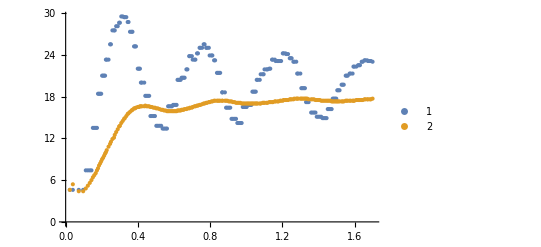

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet1ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

Classic servo oscillation.  We will increase the dr/dt to dampen the ringing.

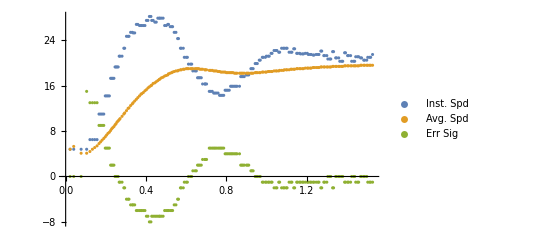

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet2ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

This control is dividing the error signal by 2.

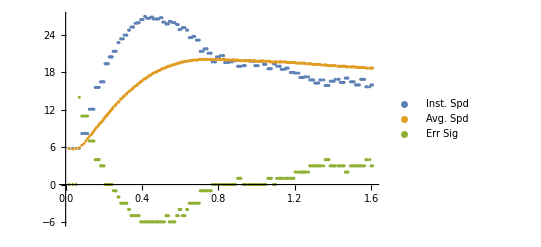

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet3ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

This control is dividing the error signal by 4.

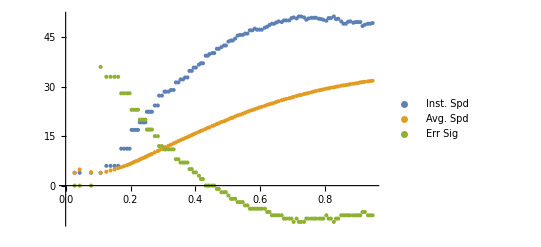

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet4ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

Target speed is 40.0 keeping dv/dt at 4

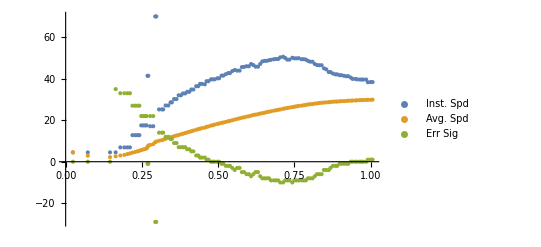

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet5ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

Target speed is 40.0 and dv/dt is 2

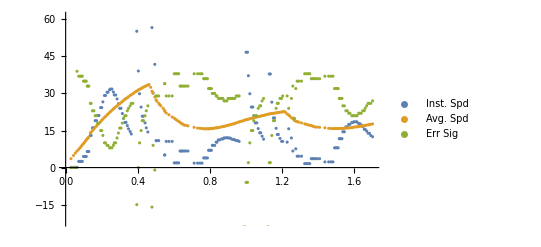

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet6ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

This is with servo control

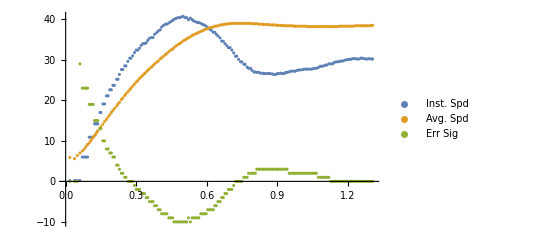

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet7ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ,{timeStamp 1*^-6,errSignal}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd", "Err Sig"}]
```

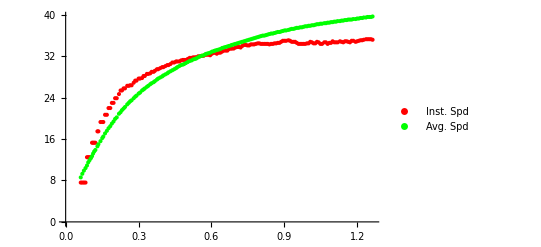

```mathematica
{pulseCount,micSecPulse,distTrav, timeStamp, speedInst, speedAvg} =dataSet9ᵀ;ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->{"Inst. Spd", "Avg. Spd"},PlotStyle->{Red,Green}]
```

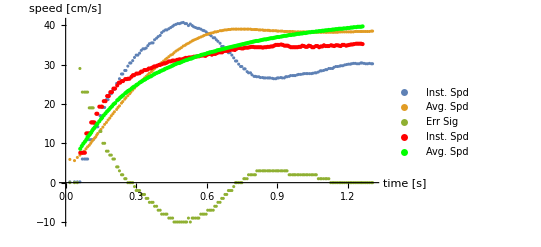

```mathematica
Show[{%88,%95},AxesLabel->{"time [s]","speed [cm/s]"}]
```

This shows that servoing the speed might not be worth the effort.  The rise time on the average speed is faster than the non-servo case but it doesn’t seem justified by the effort.  We shall revisit this as we implement the acceleration algorithm.

## Asynchronous Tests

#### Datasets

```mathematica
out01 = {{4548,0.11,0.14},{9652,0.21,0.14},{14500,0.32,0.14},{19110,0.43,0.14},{23906,0.53,16.49},{28488,0.64,16.49},{32828,0.74,16.49},{36934,0.85,16.49},{41196,0.96,18.46},{45320,1.06,18.46},{49248,1.17,18.46},{52996,1.28,18.46},{56906,1.38,20.32},{60672,1.49,20.32},{64432,1.60,20.32},{68224,1.70,20.32},{72286,1.81,20.75},{76330,1.91,20.75},{80246,2.02,20.75},{84076,2.13,20.75},{88106,2.23,20.18},{92056,2.34,20.18},{95820,2.45,20.18},{99462,2.55,20.18},{103260,2.66,21.06},{106966,2.77,21.06},{110478,2.87,21.06},{115558,2.98,21.06},{119188,3.08,21.71},{122712,3.19,22.45},{125838,3.30,22.45},{127362,3.40,23.24},{130664,3.51,23.24},{134336,3.62,23.78},{137778,3.72,23.78},{141054,3.83,23.50},{144536,3.94,23.50},{148314,4.04,23.03},{151768,4.15,23.03},{155014,4.25,22.87},{158434,4.36,22.87},{162090,4.47,23.02},{167002,4.57,23.02},{170194,4.68,23.37},{175340,4.89,23.80},{178522,5.00,23.80},{183036,5.11,24.35},{187914,5.32,25.06},{190940,5.42,25.06},{196718,5.53,25.69},{199908,5.74,26.35},{202796,5.85,26.35},{208592,6.06,26.79},{211924,6.17,26.76},{215050,6.28,26.76},{219630,6.38,26.13},{224694,6.59,26.13},{227890,6.70,25.29},{232522,6.81,24.86},{235772,6.91,24.86},{239092,7.02,24.81},{243696,7.23,24.85},{248472,7.34,24.85},{251696,7.44,25.11},{256192,7.66,25.43},{260780,7.76,25.43},{263900,7.87,25.75},{269668,8.08,26.27},{272626,8.19,26.27},{276934,8.40,27.41},{281162,8.51,27.41},{285290,8.61,27.41},{289564,8.83,28.51},{293558,9.04,28.51},{297712,9.15,28.91},{301820,9.36,29.41},{304612,9.47,29.41},{310386,9.68,27.99},{313376,9.78,27.99},{317788,9.89,27.99},{322254,10.10,26.89},{325290,10.21,26.89},{331112,10.42,26.89},{334166,10.53,26.79},{338680,10.64,26.79},{342906,10.85,26.79},{347336,10.95,27.21},{351690,11.17,27.21},{355808,11.27,27.42},{358830,11.38,27.67},{364380,11.59,27.67},{368386,11.81,28.12},{372792,11.91,28.56},{377938,12.12,29.00},{380786,12.23,29.39},{386022,12.44,29.39},{389840,12.66,29.75},{395196,12.87,30.18},{397622,12.98,30.61},{403064,13.19,30.69},{407010,13.29,30.22},{411100,13.51,30.22},{415458,13.61,29.22},{419664,13.83,28.51},{424020,13.93,28.51},{427050,14.04,27.88},{432778,14.25,27.49},{435738,14.36,27.49},{440088,14.57,27.26},{444430,14.68,27.26},{448666,14.89,27.26},{454534,15.10,27.70},{457298,15.21,27.70},{462910,15.42,28.25},{465752,15.53,28.25},{471138,15.74,28.25},{475256,15.85,28.91},{479340,16.06,28.91},{483158,16.17,29.35},{487242,16.38,29.81},{492272,16.59,30.17},{496316,16.70,30.66},{500116,16.91,30.66},{504964,17.12,31.04},{508794,17.23,31.53},{512526,17.44,31.75},{517950,17.66,31.34},{521822,17.76,30.56},{525850,17.97,30.56},{530086,18.08,29.72},{535486,18.29,29.18},{538298,18.40,29.18},{542446,18.61,28.72},{546614,18.72,28.72},{550698,18.93,28.72},{556398,19.14,28.73},{559110,19.25,28.73},{564608,19.46,28.87},{568740,19.57,28.87},{572648,19.78,28.87},{576714,19.89,29.54},{581978,20.10,29.54},{584512,20.21,29.78},{590018,20.42,30.10},{593644,20.63,30.36},{597694,20.74,30.63},{602698,20.95,30.63},{606348,21.16,31.00},{611534,21.38,31.57},{616294,21.59,31.80},{618932,21.70,32.11},{623652,21.91,32.41},{627414,22.02,32.41},{632646,22.23,31.66},{636542,22.44,31.66},{640674,22.55,30.69},{644688,22.76,29.95},{648804,22.87,29.95},{652968,23.08,28.88},{657154,23.19,28.88},{661272,23.40,28.88},{666990,23.61,28.53},{669720,23.72,28.53},{675254,23.93,28.75},{678042,24.04,28.75},{683382,24.25,28.75},{687500,24.36,29.21},{691586,24.57,29.21},{695382,24.67,29.46},{700942,24.89,29.76},{704554,25.10,29.76},{708604,25.21,30.57},{713630,25.42,30.57},{717284,25.63,30.97},{721298,25.74,31.47},{724768,25.95,31.79},{729862,26.16,32.18},{734510,26.38,32.55},{738112,26.48,32.55},{743104,26.70,32.84},{746854,26.91,32.84},{750866,27.01,32.00},{756044,27.23,31.02},{758754,27.33,31.02},{764224,27.55,29.80},{768248,27.65,29.80},{772458,27.87,29.46},{776500,28.08,29.22},{780562,28.18,29.22},{784646,28.40,29.21},{790086,28.61,29.21},{792710,28.72,29.21},{798230,28.93,29.47},{803410,29.14,29.47},{806120,29.25,29.99},{811366,29.46,29.99},{815098,29.57,30.24},{819164,29.78,30.57},{822884,29.89,30.57},{827968,30.10,31.38},{832896,30.31,31.38},{835256,30.42,31.84},{840412,30.63,32.19},{844976,30.84,32.56},{848760,31.06,32.93},{853314,31.27,33.17},{857004,31.38,33.61},{861812,31.59,33.61},{865434,31.80,33.46},{870714,32.01,32.56},{874468,32.12,31.74},{878626,32.33,30.87},{883814,32.54,30.27},{886500,32.65,30.27},{890700,32.76,29.71},{896042,32.97,29.44},{898808,33.08,29.44},{904312,33.29,29.23},{909670,33.50,29.23},{912470,33.61,29.35},{917724,33.82,29.48},{920420,33.93,29.48},{925794,34.14,29.84},{929658,34.35,29.84},{934906,34.57,30.36},{937500,34.67,30.36},{942504,34.88,30.36},{946334,34.99,31.29},{951292,35.20,31.29},{955100,35.42,31.95},{958832,35.52,31.95},{963450,35.74,32.32},{968476,35.95,32.76},{971784,36.16,33.12},{976688,36.37,33.57},{981400,36.59,33.45},{983882,36.69,33.45},{989172,36.91,32.62},{994210,37.12,31.72},{998294,37.22,30.87},{1002240,37.44,30.33},{1006286,37.54,30.33},{1011806,37.76,29.46},{1014456,37.86,29.46},{1020064,38.08,29.24},{1024080,38.29,29.13},{1028134,38.39,29.13},{1032182,38.61,29.33},{1037584,38.82,29.33},{1041422,38.93,29.40},{1045674,39.14,29.61},{1050864,39.35,29.61},{1054844,39.46,30.10},{1060000,39.67,30.10},{1062484,39.78,30.31},{1067860,39.99,30.70},{1072688,40.20,30.99},{1076618,40.42,31.42},{1081396,40.63,31.75},{1086452,40.84,32.23},{1091120,41.05,32.66},{1096060,41.16,32.66},{1098420,41.37,33.06},{1103136,41.59,33.22},{1108390,41.80,32.98},{1112090,41.90,32.10},{1117508,42.12,31.04},{1121462,42.33,30.36},{1125556,42.44,30.36},{1131132,42.65,29.20},{1133816,42.76,29.20},{1139524,42.97,28.94},{1143664,43.18,28.64},{1147814,43.29,28.64},{1151958,43.50,28.65},{1156094,43.61,28.65},{1160166,43.82,28.65},{1165772,44.03,28.91},{1171044,44.24,28.91},{1173812,44.35,29.52},{1179158,44.56,29.52},{1182942,44.67,29.73},{1187098,44.88,30.03},{1192164,45.09,30.03},{1196050,45.20,30.81},{1201080,45.41,30.81},{1206106,45.63,31.21},{1209802,45.84,31.65},{1214508,46.05,32.02},{1218392,46.16,32.49},{1222962,46.37,32.90},{1226824,46.58,33.00},{1231722,46.80,32.45},{1235630,46.90,32.45},{1240988,47.12,30.60},{1244940,47.33,30.60},{1249134,47.43,30.01},{1254468,47.65,29.55},{1257252,47.75,29.55},{1262816,47.97,29.08},{1268310,48.18,29.08},{1271168,48.29,28.99},{1276540,48.50,28.81},{1280572,48.71,28.81},{1284774,48.82,29.23},{1288752,49.03,29.23},{1294092,49.24,29.75},{1298042,49.35,29.75},{1301946,49.56,29.75},{1307274,49.77,30.30},{1312260,49.99,30.30},{1316110,50.09,31.17}};
```

```mathematica
out02 = {{1708,0.11,0.14},{6388,0.21,0.14},{11008,0.32,0.14},{15982,0.43,0.14},{20722,0.53,16.78},{24918,0.64,16.78},{29110,0.74,16.78},{33642,0.85,16.78},{37998,0.96,18.47},{41866,1.06,18.47},{45756,1.17,18.47},{51984,1.28,19.23},{53792,1.38,19.23},{57594,1.49,19.90},{61258,1.60,19.90},{65044,1.70,20.49},{68852,1.81,20.49},{72478,1.91,21.27},{75980,2.02,21.27},{79628,2.13,21.60},{83288,2.23,21.60},{86748,2.34,22.12},{90102,2.45,22.12},{93572,2.55,22.66},{97118,2.66,22.66},{100472,2.77,23.09},{103732,2.87,23.09},{107126,2.98,23.38},{110536,3.08,23.38},{113786,3.19,23.81},{116934,3.30,23.81},{120224,3.40,24.12},{123558,3.51,24.12},{126708,3.62,24.57},{129788,3.72,24.57},{136204,3.94,24.88},{139296,4.04,25.19},{142300,4.15,25.19},{146898,4.25,25.51},{151640,4.47,25.74},{156176,4.57,25.96},{159092,4.68,25.96},{163772,4.89,26.23},{168220,5.00,26.43},{171098,5.11,26.43},{177152,5.32,26.62},{180070,5.42,26.93},{184252,5.64,26.93},{188878,5.74,27.08},{191732,5.85,27.30},{197492,6.06,27.30},{200428,6.17,27.47},{204592,6.38,27.68},{208928,6.49,27.68},{213274,6.70,28.07},{217338,6.81,28.07},{221600,7.02,28.07},{224528,7.13,28.36},{229764,7.34,28.36},{232694,7.44,28.36},{238152,7.66,28.94},{240788,7.76,28.94},{245086,7.87,28.97},{250316,8.08,29.09},{252998,8.19,29.09},{258598,8.40,29.49},{261102,8.51,29.49},{266660,8.72,29.59},{270532,8.93,29.79},{274426,9.04,29.79},{278522,9.25,29.86},{282382,9.36,30.04},{286340,9.57,30.19},{291646,9.78,30.30},{294178,9.89,30.30},{299542,10.10,30.41},{302112,10.21,30.46},{307262,10.42,30.52},{311118,10.53,30.52},{314992,10.74,30.69},{320264,10.95,30.85},{324082,11.06,30.87},{329098,11.27,30.97},{331732,11.38,30.97},{336850,11.59,31.14},{341912,11.81,31.14},{345800,12.02,31.41},{349450,12.12,31.41},{353278,12.34,31.41},{358294,12.55,31.53},{363394,12.76,31.53},{366016,12.87,31.63},{370770,13.08,31.63},{374698,13.19,31.71},{379488,13.40,31.90},{384630,13.61,32.04},{388268,13.83,32.16},{391842,13.93,32.16},{396980,14.15,32.26},{401718,14.36,32.26},{405512,14.57,32.34},{409092,14.68,32.41},{412758,14.89,32.56},{417676,15.10,32.68},{422488,15.32,32.81},{426100,15.42,32.81},{429760,15.63,32.79},{434736,15.85,32.79},{438318,15.95,32.81},{443030,16.17,32.85},{447990,16.38,32.95},{452690,16.59,33.03},{456346,16.80,33.03},{459994,16.91,33.14},{464772,17.12,33.14},{468434,17.34,33.29},{472954,17.55,33.29},{477948,17.76,33.55},{481260,17.87,33.55},{486180,18.08,33.61},{490748,18.29,33.59},{494444,18.51,33.59},{497990,18.61,33.76},{502498,18.83,33.76},{507362,19.04,34.03},{511862,19.25,34.03},{515480,19.46,34.06},{520048,19.68,34.08},{524822,19.89,34.09},{529366,20.10,34.18},{532788,20.21,34.28},{536412,20.42,34.28},{540992,20.63,34.36},{544438,20.74,34.36},{549106,20.95,34.40},{553714,21.16,34.40},{558372,21.38,34.46},{561644,21.59,34.46},{566510,21.80,34.52},{570898,22.02,34.52},{575770,22.23,34.47},{580154,22.44,34.47},{583770,22.55,34.55},{588212,22.76,34.58},{591824,22.97,34.58},{596386,23.19,34.61},{599722,23.29,34.61},{604506,23.50,34.62},{608930,23.72,34.62},{613704,23.93,34.70},{618128,24.14,34.70},{621680,24.36,34.72},{626170,24.57,34.65},{630872,24.78,34.67},{635348,24.99,34.77},{638736,25.10,34.75},{643424,25.31,34.83},{647888,25.53,34.85},{652566,25.74,34.86},{657042,25.95,34.91},{659372,26.06,34.91},{663968,26.27,34.92},{668498,26.48,34.92},{673080,26.70,35.01},{676310,26.91,35.01},{681116,27.12,35.00},{685436,27.33,35.00},{690240,27.55,34.99},{694548,27.76,34.99},{698124,27.87,35.01},{702502,28.08,35.05},{707224,28.29,35.13},{711596,28.50,35.11},{715020,28.72,35.09},{719626,28.93,35.02},{724134,29.14,34.98},{728716,29.35,35.11},{733212,29.57,35.12},{736586,29.67,35.12},{741160,29.89,35.11},{745704,30.10,35.11},{749126,30.31,35.05},{753506,30.52,34.98},{757140,30.63,35.04},{761574,30.84,35.05},{766234,31.06,35.19},{770660,31.27,35.11},{774122,31.48,35.11},{778636,31.69,35.07},{783238,31.91,35.07},{787722,32.12,35.03},{792304,32.33,35.03},{796802,32.54,35.24},{800094,32.65,35.24},{804816,32.86,35.08},{809182,33.08,35.08},{813884,33.29,35.19},{818220,33.50,35.19},{821690,33.71,35.27},{826072,33.93,35.40},{830684,34.14,35.50},{835084,34.35,35.50},{839702,34.57,35.47},{843026,34.67,35.38},{847408,34.88,35.38},{851992,35.10,35.59},{855330,35.31,35.62},{859838,35.52,35.70},{864268,35.74,35.69},{867586,35.84,35.69},{872066,36.05,35.76},{876476,36.27,35.76},{880928,36.48,35.99},{885324,36.69,35.99},{889780,36.91,36.06},{892922,37.12,36.06},{897586,37.33,36.04},{901768,37.54,36.04},{906412,37.76,36.17},{910578,37.97,36.17},{915218,38.18,36.25},{919382,38.39,36.25},{922850,38.50,36.30},{927070,38.71,36.24},{931628,38.93,36.33},{935834,39.14,36.44},{940380,39.35,36.46},{945668,39.56,36.49},{949142,39.78,36.46},{954422,40.10,36.45},{957662,40.20,36.46},{962144,40.42,36.46},{966420,40.63,36.45},{970900,40.84,36.49},{975168,41.05,36.46},{979636,41.27,36.49},{983892,41.48,36.55},{988370,41.69,36.55},{992634,41.90,36.52},{995964,42.12,36.52},{1000296,42.33,36.48},{1004712,42.54,36.48},{1009040,42.76,36.49},{1013456,42.97,36.49},{1017788,43.18,36.51},{1022202,43.39,36.51},{1026522,43.61,36.51},{1030934,43.82,36.51},{1036250,44.03,36.57},{1040774,44.24,36.57},{1044966,44.46,36.62},{1049500,44.67,36.62},{1053692,44.88,36.58},{1058222,45.09,36.59},{1062420,45.31,36.58},{1065716,45.52,36.59},{1070130,45.73,36.54},{1074470,45.95,36.50},{1078892,46.16,36.44},{1084230,46.37,36.45},{1088708,46.58,36.49},{1092976,46.80,36.53},{1097470,47.01,36.46},{1101748,47.22,36.40},{1106260,47.43,36.35},{1110534,47.65,36.32},{1115028,47.86,36.39},{1119298,48.07,36.43},{1123806,48.29,36.37},{1129092,48.60,36.36},{1133758,48.82,36.15},{1137896,49.03,36.15},{1141354,49.14,36.44},{1146672,49.35,36.44},{1150130,49.56,36.32},{1154364,49.77,36.37},{1158936,49.99,36.26},{1163198,50.20,36.22}};
```

#### Analysis

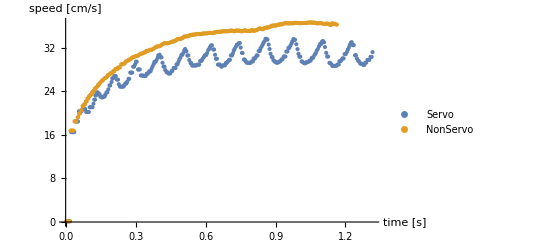

```mathematica
ListPlot[{{out01ᵀ⟦1⟧ 1*^-6,out01ᵀ⟦3⟧}ᵀ,{out02ᵀ⟦1⟧ 1*^-6,out02ᵀ⟦3⟧}ᵀ},PlotLegends->{"Servo","NonServo"},AxesLabel->{"time [s]","speed [cm/s]"}]
```

Servo isn’t worth it.

Fixed a small problem with the start time:

```mathematica
{pulseCount,errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} =servoSet8ᵀ;
ListPlot[{{timeStamp 1*^-6,speedInst}ᵀ,{timeStamp 1*^-6,speedAvg}ᵀ},PlotLegends->Automatic]
```

Set::shape: Lists TraditionalForm`{pulseCount, errSignal, motorPower, distTrav, timeStamp, speedInst, speedAvg} and TraditionalForm`( « 1 » ) are not the same shape.

Transpose::nmtx: The first two levels of TraditionalForm`{timeStamp/1000000, speedInst} cannot be transposed.

Transpose::nmtx: The first two levels of TraditionalForm`{timeStamp/1000000, speedAvg} cannot be transposed.

Transpose::nmtx: The first two levels of TraditionalForm`{1.×10^-6\ timeStamp, speedInst} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

-Graphics-

## Final Notes and Proposals

Step 1: Tune the speed of the wheels to insure mostly straight travel.
Step 2: Implement a simple line following servo to correct for deviation from straight.  N.B. There are only two sensors and they are reatively far apart.  This results in an insteresting stability issue when tracking a line.  The arduino had 5 sensors fairly closely spaced so the tracking could be better controlled.

## Accelerometer

### Data

```mathematica
(* Robot is on a level surface *)
accelData01 = {{{-28,-73,1023},{-1.6,-4.1,-159.0}},{{-26,-70,1022},{-1.5,-3.9,-159.6}},{{-31,-67,1025},{-1.7,-3.7,-155.2}},{{-25,-67,1021},{-1.4,-3.8,-159.5}},{{-28,-69,1023},{-1.6,-3.9,-157.9}},{{-27,-70,1020},{-1.5,-3.9,-158.9}},{{-25,-69,1027},{-1.4,-3.8,-160.1}},{{-29,-71,1022},{-1.6,-4.0,-157.8}},{{-25,-69,1024},{-1.4,-3.9,-160.1}},{{-27,-68,1023},{-1.5,-3.8,-158.3}},{{-29,-69,1019},{-1.6,-3.9,-157.2}},{{-26,-73,1023},{-1.5,-4.1,-160.4}},{{-27,-67,1025},{-1.5,-3.7,-158.1}},{{-24,-68,1022},{-1.3,-3.8,-160.6}},{{-25,-71,1024},{-1.4,-4.0,-160.6}},{{-25,-70,1023},{-1.4,-3.9,-160.3}},{{-31,-69,1028},{-1.7,-3.8,-155.8}},{{-28,-66,1020},{-1.6,-3.7,-157.0}},{{-26,-70,1020},{-1.5,-3.9,-159.6}},{{-28,-71,1021},{-1.6,-4.0,-158.5}},{{-27,-70,1024},{-1.5,-3.9,-158.9}},{{-27,-72,1024},{-1.5,-4.0,-159.4}},{{-27,-65,1024},{-1.5,-3.6,-157.4}},{{-29,-68,1023},{-1.6,-3.8,-156.9}},{{-26,-70,1021},{-1.5,-3.9,-159.6}},{{-30,-69,1024},{-1.7,-3.9,-156.5}},{{-25,-69,1021},{-1.4,-3.9,-160.1}},{{-32,-69,1026},{-1.8,-3.8,-155.1}},{{-26,-68,1023},{-1.5,-3.8,-159.1}},{{-29,-72,1016},{-1.6,-4.1,-158.1}},{{-25,-69,1024},{-1.4,-3.9,-160.1}},{{-29,-69,1023},{-1.6,-3.9,-157.2}},{{-29,-68,1020},{-1.6,-3.8,-156.9}},{{-28,-68,1023},{-1.6,-3.8,-157.6}},{{-29,-70,1019},{-1.6,-3.9,-157.5}},{{-30,-71,1019},{-1.7,-4.0,-157.1}},{{-29,-68,1022},{-1.6,-3.8,-156.9}},{{-28,-70,1020},{-1.6,-3.9,-158.2}},{{-28,-66,1018},{-1.6,-3.7,-157.0}},{{-27,-71,1023},{-1.5,-4.0,-159.2}},{{-29,-70,1023},{-1.6,-3.9,-157.5}},{{-31,-71,1020},{-1.7,-4.0,-156.4}},{{-31,-68,1024},{-1.7,-3.8,-155.5}},{{-26,-68,1020},{-1.5,-3.8,-159.1}},{{-26,-69,1023},{-1.5,-3.9,-159.4}},{{-29,-69,1020},{-1.6,-3.9,-157.2}},{{-30,-72,1021},{-1.7,-4.0,-157.4}},{{-27,-69,1024},{-1.5,-3.9,-158.6}},{{-27,-69,1025},{-1.5,-3.9,-158.6}}};
```

```mathematica
(* Robot is facing up a 45° slope *)
accelData02 = {{{708,-30,738},{43.8,-2.3,92.4}},{{708,-27,738},{43.8,-2.1,92.2}},{{707,-28,735},{43.9,-2.2,92.3}},{{708,-27,732},{44.0,-2.1,92.2}},{{708,-28,732},{44.0,-2.2,92.3}},{{707,-27,739},{43.7,-2.1,92.2}},{{709,-28,737},{43.9,-2.2,92.3}},{{710,-31,741},{43.8,-2.4,92.5}},{{706,-22,734},{43.9,-1.7,91.8}},{{711,-32,736},{44.0,-2.5,92.6}},{{706,-27,738},{43.7,-2.1,92.2}},{{709,-27,734},{44.0,-2.1,92.2}},{{705,-27,735},{43.8,-2.1,92.2}},{{709,-30,739},{43.8,-2.3,92.4}},{{710,-28,733},{44.1,-2.2,92.3}},{{708,-29,733},{44.0,-2.3,92.3}},{{711,-25,736},{44.0,-1.9,92.0}},{{706,-29,734},{43.9,-2.3,92.4}},{{707,-31,735},{43.9,-2.4,92.5}},{{708,-30,734},{44.0,-2.3,92.4}},{{712,-28,738},{44.0,-2.2,92.3}},{{709,-30,734},{44.0,-2.3,92.4}},{{709,-25,732},{44.1,-2.0,92.0}},{{708,-31,740},{43.7,-2.4,92.5}},{{710,-30,734},{44.0,-2.3,92.4}},{{711,-28,734},{44.1,-2.2,92.3}},{{710,-24,734},{44.0,-1.9,91.9}},{{710,-28,735},{44.0,-2.2,92.3}},{{710,-27,735},{44.0,-2.1,92.2}},{{709,-27,737},{43.9,-2.1,92.2}},{{713,-29,735},{44.1,-2.3,92.3}},{{712,-27,738},{44.0,-2.1,92.2}},{{707,-27,736},{43.8,-2.1,92.2}},{{715,-29,741},{44.0,-2.2,92.3}},{{708,-28,732},{44.0,-2.2,92.3}},{{710,-26,737},{43.9,-2.0,92.1}},{{710,-28,737},{43.9,-2.2,92.3}},{{707,-26,734},{43.9,-2.0,92.1}},{{712,-29,734},{44.1,-2.3,92.3}},{{706,-28,738},{43.7,-2.2,92.3}},{{706,-24,737},{43.8,-1.9,91.9}},{{709,-26,737},{43.9,-2.0,92.1}},{{710,-29,736},{44.0,-2.3,92.3}},{{708,-27,730},{44.1,-2.1,92.2}},{{714,-27,737},{44.1,-2.1,92.2}},{{712,-29,728},{44.4,-2.3,92.3}},{{709,-29,736},{43.9,-2.3,92.3}},{{707,-28,736},{43.8,-2.2,92.3}},{{708,-29,737},{43.9,-2.3,92.3}}};
```

### Analysis

```mathematica
angles[ d_ ]:= d⟦2⟧; accels[d_]:=d⟦1⟧;
```

Averages of robot

```mathematica
Mean[angles /@ accelData01]
```

{-1.55102,-3.87959,-158.224}

```mathematica
StandardDeviation[angles /@ accelData01]
```

{0.104328,0.107973,1.46579}

```mathematica
Mean[angles /@ accelData02]
```

{43.9408,-2.17551,92.2551}

```mathematica
StandardDeviation[angles /@ accelData02]
```

{0.133726,0.152111,0.155538}